Optimization utilities for use with Inverse.

Original opt_inverse is contained in $IGHOME/inverse.

Set working directory:
   Allways check that  working directory is set correctly!

```mathematica
(* Gradbena:
SetDirectory["E:/users/c3m/igor/enlub/work/SRT_identification_2006-01-20/StripReduction"]
*)

SetDirectory["c:/users/igor/doc/pr/enlub/work/SRT_identification_2006-01-20/StripReduction/"]
```

c:\users\igor\doc\pr\enlub\work\SRT_identification_2006-01-20\StripReduction

Running optimization from "Inverse"  - debugging mode

### Instructions: For debugging, run Inverse from debugger with the -linkcreate option, e.g. C:/users/igor/cz/invmath.exe optmath.cm -linkcreate A message box is launched stating the name of the link. You must insert this name in the cell below and evaluate it, then swithch to debugger and perform debugging (don't forget to set breakpoints).

### Important note: Correct directory paths before evaluation!

```mathematica
(* For debugging - insert the reported link name (copy from message box) first! *)
link=Install[LinkConnect["bmr_shm"]];
InvInterpret[]
```

{KONTROLA: InvInterpret - finished.}

## Run "Inverse" - test This will run "Inverse". (This is a test, otherwise Inverse is run by the command runinverse[]. )

You don't need to run this if you don't do optimization with Inverse.

### Checks for of runiverse[ ]

#### Important note: Correct directory paths before evaluation!

```mathematica
(*
SetDirectory["C:\\users\\igor\\c\\0exmath"];
link=Install["C:\users\igor\cz\invmath.exe invmath.cm"];
*)

(* Remark: command file default.cm must be in the current directory before evaluating this cell. The file can be empty.  *)
link=Install["invmath.exe default.cm"];

Print["Running ",InvGetVar["string","program",{}]," ",InvGetVar["scalar","version",{}],"."]

InvInterpret[]

runinverse[]
```

Running Inverse 3.12.

{KONTROLA: InvInterpret - finished.}

```mathematica
Directory[]
```

c:\users\igor\doc\pr\enlub\work\SRT_identification_2006-01-20\StripReduction

# Collection of supporting utilities

```mathematica
If[testmode≠0,testmode=0;];
If[debugmode≠0,debugmode=0;];
```

## Definition of test optimization problems (analysis functions)

In order to define optimisation problems in Mathematica for use with Inverse,  the problem must be defined in form of standard analysis function. This function is called in the following way:

results = analysisfunction[param, calcobj, calcconstr, calcgradobj, calcgradconstr, clientdata ];

Arguments of the function have the following meaning:
  param is vector of optimization parameters at which response functions and eventually their gradients must be evaluated. It must be a list of numbers.
  calcobj specifies whether the objective function should be evaluated. 0 means that it does not need to be evaluated, non-zero values mean that it should be evaluated. It must be an integer number (usually 0 or 1).
  calcconstr specifies whether constraint functions should be evaluated.
  calcgradobj specifies whether gradient of the objective function should be evaluated.
  calcgradconstr specifies whether gradients of constraint functions should be evaluated.
  clientdata can hold additional definition data that define how to evaluate the response or provide some other information for the analysis function. The structure of clientdata is not prescribed in general and is dependent on the analysis function. Some functions will not use this argument, so this will be a dummy argument defined just for sticking with the prescribed function form. There is however a standard agreement that clientdata should b a string, which can eventually be interpreted within the function by using the ToExpression function. This is convenient for calling analysis functions from a program that uses Mathlink.
  
Returned result must be of the form 
    {calcobj, obj, calcconstr, constr, calcgradobj, gradobj, calcgradconstr, gradconstr, ret}
  where
    calcobj, calcconstr, calcgradobj and calcgradconstr specify whether the objective function, constraint functions, gradient of teh objective function and gradients of the constraint functions were evaluated
    obj is the value of the objective function (numerical)
    constr is a list of constraint function values
    gradobj is objective function gradient (vector / list of numbers)
    gradconstr is a list of constraint function gradients (themselves being list of numbers)
    ret is error code (integer) - 0 if no error has been detected or usually a negative value if an error occured. 

Remarks - inequality constraints 
Agreement for constraint functions corresponding to inequality constraint is that constraints are defined as
  c_i (p)≤0

#### Remarks on use:

Such definitions of optimisation problems can be used in optimization algorithms called from Inverse by calling the function Smathanalyse{} in the commmand file. This function must be called in the analysis block of the command file, such as e.g. in optmath.cm, which is interpreted below. Inverse interpreter function Smathanalyse{} calls the appropriate analysis function in Mathematica (whose name and definition data are passed as arguments), gets results of evaluation and writes these results to the appropriate pre-defined variables. Optimisation algorithms implemented in Inverse pick the result from these pre-defined variables (which are implementation specifics of Inverse). 

	Once again, if we want to use problem definition for solution by optimisation procedures implemented in Inverse then Smathanalyse{} (which calls a particular analysis function defined in Mathematica) must be called within the analysis{} block of Inverse command file. Caller does not need to take care of other things because Smathanalyse automatically writes the results to appropriate places (pre-defined variables of Inverse) where the algorithms look for them. Also, Smath{} obtains the current optimization parameters (that are usually set by an optimisation algorithm) and passes them properly to the analysis function called in Mathematica.

Example: anfuncsimp[...], very simple unconstrained analysis function (quadratic objective, arbitrary number of parameters specified by definition data)

#### Problem description:

This particular function is set up for the problem
min f(x1,x1,...)=x1^2+x2^2+... . 
Solution is {1, 1, 1, ..., 1}
The number of parameters must be specified by the definition data (the last argument).

```mathematica
anfuncsimp[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
anfuncbassimp[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

anfuncbassimp[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,    obj=0,constr={},gradobj={},gradconstr={},ret=0,result},
(* $A Igor jan06; *)
If[debugmode!0,
Print["anfuncsimp : analysis at parameters ",p];
];

If[calcobj≠ 0,
obj=Sum[p[[i]]^2,{i,1,Length[p]}];
];

If[calcgradobj≠0,
gradobj=Table[2*p[[i]],{i,1,Length[p]}];
];

If[calcconstr≠0,
ret=-1;
retcalcconstr=0;
];

If[calcgradconstr≠0,
ret=-1;
retcalcgradconstr=0;
];

result={retcalcobj,obj,
retcalcconstr,constr,
retcalcgradobj,gradobj,
retcalcgradconstr,gradconstr,
ret};

(* Record results in analysis history, if recording is on: *)
appendanhistory["anfuncsimp",{p,result,{calcobj,calcconstr,calcgradobj,calcgradconstr,cd}}];

(* Return the result: *)
result
];
```

#### Checks (anfuncsimp):

```mathematica
If[testmode≠0,
anfuncsimp[{2,2,1,3},1,0,1,0,"4"]
,,]
```

```mathematica
If[testmode≠0,
testangrad[anfuncsimp,"3",{2,2,1},10^-5]
,,]
```

Example: anfuncsimpconstr[...], very simple constrained analysis function (quadratic objective, linear constraints (each parameter must be greater or equal to 1), arbitrary number of parameters specified by definition data)

#### Problem description:

This particular function is set up for the problem
min f(x1,x1,...)=x1^2+x2^2+...,

subject to x1>1, x2>1, ...
Constraint functions are therefore
g_1(x1,x2,...)=1-x1,
g_2(x1,x2,...)=1-x2,.
The solution is {x1,x2,x3,...}={1,1,1,...}.

The number of parameters must be specified by the definition data (the last argument).

```mathematica
anfuncsimpconstr[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
anfuncbassimpconstr[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

anfuncbassimpconstr[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,    obj=0,constr={},gradobj={},gradconstr={},ret=0,result,dim,i,j},
(* $A Igor jan06; *)

dim=Length[p];

If[calcobj≠ 0,
obj=Sum[p[[i]]^2,{i,1,dim}];
];

If[calcgradobj≠0,
gradobj=Table[2*p[[i]],{i,1,dim}];
];

If[calcconstr≠0,
constr=Table[(1+i/dim)*(1-p[[i]]),{i,1,dim}];
];

If[calcgradconstr≠0,
gradconstr=Table[Table[0,{j,1,dim}],{i,1,dim}];
For[i=1,i≤dim,i=i+1,
gradconstr[[i,i]]=(1+i/dim)*(-1);
];
];

result={retcalcobj,obj,
retcalcconstr,constr,
retcalcgradobj,gradobj,
retcalcgradconstr,gradconstr,
ret};

(* Record results in analysis history, if recording is on: *)
appendanhistory["anfuncsimpconstr",{p,result,{calcobj,calcconstr,calcgradobj,calcgradconstr,cd}}];

(* Return the result: *)
result
];
```

#### Checks:

```mathematica
If[testmode≠0,
anfuncsimpconstr[{2,2,1},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testangrad[anfuncsimpconstr,"3",{3,3,3},10^-5]
,,]
```

Test problem  (2 parameters, 2 constraints) -analysis function testanfunc (the same optimisation problem as in testanfunc() in optbas.c)

#### Problem description:

This particular function is set up for the problem
min f(x,y)=(sin(sqrt(A*(x-CX)^2+B*(y-CY)^2)))^2,
subject to x≥TX+y^2 and y≥TY,
where A=0.1, B=0.005, CX=0.2, CY=-1, TX=0.6, and TY=1.
Constraint functions are therefore
g_1(x,y)=TX+y*y-x,
g_2(x,y)=TY-y.
The solution is x=1.6,y=1.

```mathematica
testanfunc[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
testanfuncbas[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

testanfuncbas[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{A,B,CX,CY,TX,TY,x,y,f,g1,g2,obj=0,constr={},gradobj={},gradconstr={},ret=0},
(* $A Igor jan06; *)

A=0.1;
B=0.005;
CX=0.2;
CY=-1;
TX=0.6;
TY=1;

(* Functions that constitute problem definition: *)
f[{x_,y_}]:=( Sin[ Sqrt[ A*(x-CX)^2+B*(y-CY)^2 ] ] )^2;
g1[{x_,y_}]:=TX+y*y-x;
g2[{x_,y_}]:=TY-y;

(*
Print["Function testanfunc called.\n"];
*)

If[calcobj≠ 0,
obj=f[p];
(*
Print["Calculating objective function.\n"];
*)
];

If[calcgradobj≠0,
gradobj={
D[f[{x,y}],x]    , D[f[{x,y}],y] 
}    /. {x->p[[1]]   ,  y->p[[2]]  }   ;
(*
Print["Calculating gradient of the objective function.\n"];
*)
];

If[calcconstr≠0,
constr={g1[p],g2[p]};
(*
Print["Calculating constraint functions.\n"];
*)
];

If[calcgradconstr≠0,
gradconstr={
{  D[ g1[{x,y}], x],     D[ g1[{x,y}], y]  },
{  D[ g2[{x,y}], x ],     D[ g2[{x,y}], y]  }
}   /. {x->p[[1]]   ,  y->p[[2]]  }  ;
(*
Print["Calculating gradient of the constraint functions.\n"];
*)
];

(* Return the result: *)
{calcobj,obj,
calcconstr,constr,
calcgradobj,gradobj,
calcgradconstr,gradconstr,
ret}
]
```

#### Check (testanfunc):

```mathematica
If[testmode≠0,

f[{x_,y_}]:=( Sin[ Sqrt[ A*(x-CX)^2+B*(y-CY)^2 ] ] )^2;
g1[{x_,y_}]:=TX+y*y-x;
g2[{x_,y_}]:=TY-y;

Print["f[{x,y}]: ",f[{x,y}]];
Print["g1[{x,y}]: ",g1[{x,y}]];

Print["g2[{x,y}]: ",g2[{x,y}]];
Print["{ D[f[{x,y}],x],D[f[{x,y}],y]}: ",{ D[f[{x,y}],x],D[f[{x,y}],y]}];

Print["{
{ D[g1[{x,y}],x],D[g1[{x,y}],y]},
{ D[g2[{x,y}],x],D[g2[{x,y}],y]}
}: ",{
{ D[g1[{x,y}],x],D[g1[{x,y}],y]},
{ D[g2[{x,y}],x],D[g2[{x,y}],y]}
}];

Print["testanfuncbas[{x,y},1,1,1,1,cd]: ",testanfuncbas[{x,y},1,1,1,1,"cd"]];

Print["testanfuncbas[{x,y},1,1,1,1,cd]: ",testanfuncbas[{x,y},1,1,1,1,"cd"]];

Print["testanfuncbas[{x,y},1,1,1,1,"cd"]: ",testanfuncbas[{x,y},1,1,1,1,"cd"]];
,,]
```

Test problem 1 (2 parameters, 2 constraints) -analysis function testanfunc1 (the same optimisation problem as in testanfunc1() in optbas.c)

#### Problem description:

min f(x,y)=x^2+y^4, subject to y≥(x-3)^6   and   y≥17-x^2,
therefore 
f(x,y)=x^2+y^4,
g_1(x,y)=(x-3)^6-y,
g_2(x,y)=17-x^2-y.
Solution: Optimum: {4,1},  objective func.in optimum:17.

```mathematica
testanfunc1[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
testanfunc1bas[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

testanfunc1bas[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{x,y,f,g1,g2,obj=0,constr={},gradobj={},gradconstr={},ret=0},
(* $A Igor jan06; *)

(* Functions that constitute problem definition: *)
f[{x_,y_}]:=x^2+y^4;
g1[{x_,y_}]:=(x-3)^6-y;
g2[{x_,y_}]:=17-x^2-y;

(*
Print["Function testanfunc1 called.\n"];
*)

If[calcobj≠ 0,
obj=f[p];
(*
Print["Calculating objective function.\n"];
*)
];

If[calcgradobj≠0,
gradobj={
D[f[{x,y}],x]    , D[f[{x,y}],y] 
}    /. {x->p[[1]]   ,  y->p[[2]]  }   ;
(*
Print["Calculating gradient of the objective function.\n"];
*)
];

If[calcconstr≠0,
constr={g1[p],g2[p]};
(*
Print["Calculating constraint functions.\n"];
*)
];

If[calcgradconstr≠0,
gradconstr={
{  D[ g1[{x,y}], x],     D[ g1[{x,y}], y]  },
{  D[ g2[{x,y}], x ],     D[ g2[{x,y}], y]  }
}   /. {x->p[[1]]   ,  y->p[[2]]  }  ;
(*
Print["Calculating gradient of the constraint functions.\n"];
*)
];

(* Return the result: *)
{calcobj,obj,
calcconstr,constr,
calcgradobj,gradobj,
calcgradconstr,gradconstr,
ret}
]
```

#### Check (testanfunc1):

```mathematica
If[testmode≠0,
f[{x_,y_}]:=x^2+y^4;
g1[{x_,y_}]:=(x-3)^6-y;
g2[{x_,y_}]:=17-x^2-y;
,,]
```

```mathematica
If[testmode≠0,
testanfunc1bas[{x,y},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testanfunc1[{x,y},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testanfunc1[{1.1,1.2},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testangrad[testanfunc1,"cd",{1.1,1.2},10^-6];
,,];
```

Test problem  simple (2 param. quadratic function and two linear constraints): testanfuncsimp

#### Problem description:

min f(x,y)=(x/2)^2+(y/1)^2, subject to x+y≥2   and   y≥0.5,
therefore 
f(x,y)= (x/2)^2 + (y/1)^2 ,
g_1(x,y)=2-x-y ,
g_2(x,y)=0.5-y .
Solution: Optimum: {1.5,0.5},  objective func.in optimum: 1.5625.

```mathematica
testanfuncsimp[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
testanfuncsimpbas[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

testanfuncsimpbas[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{x,y,f,g1,g2,obj=0,constr={},gradobj={},gradconstr={},ret=0},
(* $A Igor jan06; *)

(* Functions that constitute problem definition: *)
f[{x_,y_}]:=(x/2)^2+(y/1)^2;
g1[{x_,y_}]:=2-x-y;
g2[{x_,y_}]:=0.5-y;

(*
Print["Function testanfunc1 called.\n"];
*)

If[calcobj≠ 0,
obj=f[p];
(*
Print["Calculating objective function.\n"];
*)
];

If[calcgradobj≠0,
gradobj={
D[f[{x,y}],x]    , D[f[{x,y}],y] 
}    /. {x->p[[1]]   ,  y->p[[2]]  }   ;
(*
Print["Calculating gradient of the objective function.\n"];
*)
];

If[calcconstr≠0,
constr={g1[p],g2[p]};
(*
Print["Calculating constraint functions.\n"];
*)
];

If[calcgradconstr≠0,
gradconstr={
{  D[ g1[{x,y}], x],     D[ g1[{x,y}], y]  },
{  D[ g2[{x,y}], x ],     D[ g2[{x,y}], y]  }
}   /. {x->p[[1]]   ,  y->p[[2]]  }  ;
(*
Print["Calculating gradient of the constraint functions.\n"];
*)
];

(* Return the result: *)
{calcobj,obj,
calcconstr,constr,
calcgradobj,gradobj,
calcgradconstr,gradconstr,
ret}
]
```

#### Checks (testanfuncsimp):

```mathematica
If[testmode≠0,
f[{x_,y_}]:=x^2+y^4;
g1[{x_,y_}]:=(x-3)^6-y;
g2[{x_,y_}]:=17-x^2-y;
,,]
```

```mathematica
If[testmode≠0,
testanfuncsimpbas[{x,y},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testanfuncsimp[{x,y},1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
testanfuncsimp[{1,2},1,1,1,1,"0"]
,,]
```

```mathematica
If[testmode≠0,
testanfuncsimp[{1.1,1.2},1,1,1,1,"cd"]
,,]
```

## Penalty function (with derivatives)

This section defines a penalty functioin that is assigned to the original constrained optimization problem. The function is written in the standard analysis form (with no constraints in results since they are replaced by penalty terms added to the objective function). Penaly parameters must be defined in the last argument cd.

### Definitions of penalty generating functions :

#### derpenfunc [ penfunc, c, param ] - calculates & returns the derivative of a penalty function derpenfunc with respect to c (constrint function) penfunc - penaltr function, must take the remaining arguments c and param. c - value of the constriant function that generates the penalty term (i.e. argument of the penalty function) param - additional parameters (definition data) for the penalty function. derpenfunc [ penfunc, c, p1, p2 ] - the same with two definition parameters, p1 and p2 derpenfunc [ penfunc, c, p1, p2 ] - the same with two definition parameters, p1 and p2 Penalty generating functions are provided in different forms: func [ c, p1, p2, ... ] - basic form, with all parameters being numbers func [ c, { p1, p2, ... } ] - definition data out in a single vector - form suited for use in higher level functions (such as penaltyanfunc) because the number of parameters is constant over all implemented penalty functions. There are also reduced forms with less parameters for some functions, i.e. in functions with 2 parameters these two are taken in some constant ratio to reduce to one parameter. Implemented penalty functions: penfuncsqr [ c, { d, h } ] - square-constant function. It is zero until -d, and has value h at 0. penfunccub, penfunc4 [ c, { d, h } ] - cubic-constant or 4-th-order-constant function. It is zero until -d, and has value h at 0. penfuncexp [ c, { d, h } ] -exponential function h*Exp[c/d]. It is non-zero everywkere and has value h at 0.d is characteristic length at which it growths by a factor e (base of natural logarithm) penfuncexpsqr [ c, { d, h } ] - exponential multiplied by a square-constant function to achieve zero values. It is zero until -d, and has value h at 0. penfuncexpcub, penfuncexp4 [ c, { d, h } ] - exponential multiplied by a cube-constant function or by fourth-order-constant function to achieve zero values. It is zero until -d, and has value h at 0. penfuncjump [ c, { h, k } ] - discontinuous jump function. It is zero until 0, jumps to value h at 0 and grows linearly with a factor k for positive c. penfunc0 [ c, { } ] - zero function (for testing purposes, e.g. to abolish constraints) These penalty generating functions have corresponding derivative functions defined, which take the same arguments, and have the name derived form the corresponding penalty generating function by adding a prefic der, e.g. derpenfuncjump [ c, { h, k } ] returns the derivative of penfuncjump with respect to c. These derivative functions are mainly intended for some testing purposes, but some have more practical intention of overcoming the discontinuity of th epenalty generating function.

```mathematica
(* General utilities: derivatives *)
derpenfunc[penfunc_,c_,param_]:=Module[{t},(  D[penfunc[t,param],t] /. t->c )  ];
derpenfunc[penfunc_,c_,p1_,p2_]:=derpenfunc[penfunc,c,{p1,p2}];
derpenfunc[penfunc_,c_,p1_,p2_,p3_]:=derpenfunc[penfunc,c,{p1,p2,p3}];
derpenfunc[penfunc_,c_,p1_,p2_,p3_,p4_]:=derpenfunc[penfunc,c,{p1,p2,p3,p4}];

(* Zero penalty generating function: *)
penfunc0[c_,d_,h_]:=0;
penfunc0[c_,h_]:=0;
penfunc0[c_,{d_,h_}]:=0;
penfunc0[c_,{h_}]:=0;
penfunc0[c_,{}]:=0;
penfunc0[c_]:=0;

derpenfunc0[c_,d_,h_]:=0;
derpenfunc0[c_,h_]:=0;
derpenfunc0[c_,{d_,h_}]:=0;
derpenfunc0[c_,{h_}]:=0;
derpenfunc0[c_,{}]:=0;
derpenfunc0[c_]:=0;

(* Square penalty generating function: *)
penfuncsqr[c_,d_,h_]:=If[c<=-d,0, h*((c+d)/d)^2];
penfuncsqr[c_,h_]:=penfuncsqr[c,h,h];
penfuncsqr[c_,{d_,h_}]:=penfuncsqr[c,d,h];
penfuncsqr[c_,{h_}]:=penfuncsqr[h];

derpenfuncsqr[c_,p_]:=derpenfunc[penfuncsqr,c,p];
derpenfuncsqr[c_,p1_,p2_]:=derpenfunc[penfuncsqr,c,p1,p2];
derpenfuncsqr[c_,p1_,p2_,p3_]:=derpenfunc[penfuncsqr,c,p1,p2,p3];

(* Cubic penalty generating function: *)
penfunccub[c_,d_,h_]:=If[c<=-d,0, h*((c+d)/d)^3];
penfunccub[c_,h_]:=penfunccub[c,h,h];
penfunccub[c_,{d_,h_}]:=penfunccub[c,d,h];
penfunccub[c_,{h_}]:=penfunccub[h];

derpenfunccub[c_,p_]:=derpenfunc[penfunccub,c,p];
derpenfunccub[c_,p1_,p2_]:=derpenfunc[penfunccub,c,p1,p2];
derpenfunccub[c_,p1_,p2_,p3_]:=derpenfunc[penfunccub,c,p1,p2,p3];

(* Fourth order penalty generating function: *)
penfunc4[c_,d_,h_]:=If[c<=-d,0, h*((c+d)/d)^4];
penfunc4[c_,h_]:=penfunc4[c,h,h];
penfunc4[c_,{d_,h_}]:=penfunc4[c,d,h];
penfunc4[c_,{h_}]:=penfunc4[h];

derpenfunc4[c_,p_]:=derpenfunc[penfunc4,c,p];
derpenfunc4[c_,p1_,p2_]:=derpenfunc[penfunc4,c,p1,p2];
derpenfunc4[c_,p1_,p2_,p3_]:=derpenfunc[penfunc4,c,p1,p2,p3];


(*  Exponential penalty generating function *)
penfuncexp[c_,d_,h_]:=h*Exp[c/d];
penfuncexp[c_,h_]:=penfuncexp[c,h,h];
penfuncexp[c_,{d_,h_}]:=penfuncexp[c,d,h];
penfuncexp[c_,{h_}]:=penfuncexp[h];

derpenfuncexp[c_,p_]:=derpenfunc[penfuncexp,c,p];
derpenfuncexp[c_,p1_,p2_]:=derpenfunc[penfuncexp,c,p1,p2];
derpenfuncexp[c_,p1_,p2_,p3_]:=derpenfunc[penfuncexp,c,p1,p2,p3];

(*  Exponential-quadratic penalty generating function *)
penfuncexpsqr[c_,d_,h_]:=penfuncexp[c,d,h]*penfuncsqr[c,d,h]/h;
penfuncexpsqr[c_,h_]:=penfuncexpsqr[c,h,h];
penfuncexpsqr[c_,{d_,h_}]:=penfuncexpsqr[c,d,h];
penfuncexpsqr[c_,{h_}]:=penfuncexpsqr[h];

derpenfuncexpsqr[c_,p_]:=derpenfunc[penfuncexpsqr,c,p];
derpenfuncexpsqr[c_,p1_,p2_]:=derpenfunc[penfuncexpsqr,c,p1,p2];
derpenfuncexpsqr[c_,p1_,p2_,p3_]:=derpenfunc[penfuncexpsqr,c,p1,p2,p3];

(*  Exponential-cubic penalty generating function *)
penfuncexpcub[c_,d_,h_]:=penfuncexp[c,d,h]*penfunccub[c,d,h]/h;
penfuncexpcub[c_,h_]:=penfuncexpcub[c,h,h];
penfuncexpcub[c_,{d_,h_}]:=penfuncexpcub[c,d,h];
penfuncexpcub[c_,{h_}]:=penfuncexpcub[h];

derpenfuncexpcub[c_,p_]:=derpenfunc[penfuncexpcub,c,p];
derpenfuncexpcub[c_,p1_,p2_]:=derpenfunc[penfuncexpcub,c,p1,p2];
derpenfuncexpcub[c_,p1_,p2_,p3_]:=derpenfunc[penfuncexpcub,c,p1,p2,p3];

(*  Exponential-4th order penalty generating function *)
penfuncexp4[c_,d_,h_]:=penfuncexp[c,d,h]*penfunc4[c,d,h]/h;
penfuncexp4[c_,h_]:=penfuncexp4[c,h,h];
penfuncexp4[c_,{d_,h_}]:=penfuncexp4[c,d,h];
penfuncexp4[c_,{h_}]:=penfuncexp4[h];

derpenfuncexp4[c_,p_]:=derpenfunc[penfuncexp4,c,p];
derpenfuncexp4[c_,p1_,p2_]:=derpenfunc[penfuncexp4,c,p1,p2];
derpenfuncexp4[c_,p1_,p2_,p3_]:=derpenfunc[penfuncexp4,c,p1,p2,p3];

(* Jump discontinuous penalty generating functions: *)
penfuncjump[c_,h_,k_]:=If[c<=-0,0, h+k*c
];
penfuncjump[c_,h_]:=penfuncjump[c,h,1];
penfuncjump[c_,{h_,k_}]:=penfuncjump[c,h,k];
penfuncjump[c_,{h_}]:=penfuncjump[c,h];

derpenfuncjump[c_,p1_,p2_,p3_]:=If[c≤0,0,derpenfunc[penfuncjump,c,p1,p2,p3]];
derpenfuncjump[c_,p1_,p2_]:=If[c≤0,0,derpenfunc[penfuncjump,c,p1,p2]];
derpenfuncjump[c_,p1_]:=If[c≤0,0,derpenfunc[penfuncjump,c,p1]];
```

### Penalty function - penaltyanfunc

#### penaltyanfunc [ p, calcobjpen, calcconstrpen, calcgradobjpen, calcgradconstrpen, cdpen ] - analysis function that adds penalty terms to the objective function of some original problem; constraint functions may or may not be kept. Standard parameters of the function are p - parameters, calcobjpen, calcconstrpen, calcgradobjpen and calcgradconstrpen - calculation request flags for the objective function, the constraint functions, and their gradients, respectively (the flags apply to this function, the penaltyanfunc, and not to the original function - it is inferred what is needed there). The definition data argument cd must be structured in the prescribed way (it can also be a string that represent the data structured in this way, in which case conversio nis performed first). cdpen = { anfuncorig, < ancdorig, penfunc, penparam, defderpenfunc, derpenfuncarg, keepconstraints > } anfuncorig - the analysis function of the original problem that is modified by addition of penalty terms (and eventually annihilation of constraints) ancdorig - definition data passed to the original analysis function anfuncorig. Optional (default: {}) penfunc [ c, { penparam } ] - penalty generating function. It must take arguments as stated here (c - independent parameter - value of the constrint function from which penalty term is generated, and { param } is a vector containing definition parameters for the penalty generating function) penparam - vector of definition parameters for penfunc. Default is {1,1} defderpenfunc - a falg for whether the derivative of penfunc is defined by the next element (derpenfuncarg) (0 - this function is not specified and will be calculated internally by symbolic differentiation of penfunc; non-zero number - defined) derpenfuncarg [ c, { penparam } ] - function that calculates the derivative of penfunc with respect to its argument c (the constraint function value). If defderpenfuncarg is 0 or not specified then this function is not used and does not need to be specified. keepconstraints - flag for keeping constriants (default is 0) - if 0 then constraints are not kept by penaltyanfunc and are reflected only in penalty terms added to the original objective function; otherwise constraints are kept. Important: it is generally agreed that all elements of cdpen are specified (otherwise, warnings are launched). penaltyanfuncconstr - always keeps the constraints of the original function (if they exist), regardless fo the corresponding parameter in cdpen penaltyanfuncbas [ p, calcobjpen, calcconstrpen, calcgradobjpen, calcgradconstrpen, cdpen[[1]], cdpen[[2]], ..., cdpen[[-1]] ] - performs calculation for penaltyanfunc.

```mathematica
(* Function where one can specify whether to keep constraints in the analysis function or not: *)
penaltyanfunc[p_,calcobjpen_,calcconstrpen_,calcgradobjpen_,calcgradconstrpen_,
cdpen_]:=penaltyanfunc0[p,calcobjpen,calcconstrpen,calcgradobjpen,calcgradconstrpen,
cdpen,2];

penaltyanfuncconstr[p_,calcobjpen_,calcconstrpen_,calcgradobjpen_,calcgradconstrpen_,
cdpen_]:=penaltyanfunc0[p,calcobjpen,calcconstrpen,calcgradobjpen,calcgradconstrpen,
cdpen,1];


penaltyanfunc0[p_,calcobjpen_,calcconstrpen_,calcgradobjpen_,calcgradconstrpen_,
cdpen_,constrswitch_]:=Module[
{cd,anfuncorig,ancdorig={},penfunc=penfuncexpsqr,penparam={1,1},defderpenfunc=0,derpenfuncarg ,keepconstraints=0},
(* $A Igor feb08; *)
(* Parameter constrswitch:
  0 - conatraints are not kept
1 - constraints are kept 
2 - constraints are kept in the analysis function according to definition data (default is 0)  *)

If[cdpen[[0]]==String,
cd=ToExpression[cdpen],
cd=cdpen,cd=cdpen;
];
(* Get the original analysis function: *)
If[Length[cd]≥1,  anfuncorig=cd[[1]],
Print["\n\nERROR in penaltyanfunc: the original analysis function is not defined.\n   Definition data: ",cd," \n\n"];
Return[];
 ];
(* Get the definition data for the original analysis function: *)
If[Length[cd]≥2,  ancdorig=cd[[2]],
Print["\nWarning: penaltyanfunc: analysis definition data is not defined, ",ancdorig," is taken.\n   Definition data: ",cd," \n"];
 ];
(* Get the penalty generating function: *)
If[Length[cd]≥3,  penfunc=cd[[3]],
Print["\n\nWarning: penaltyanfunc: penalty generating function is not defined, ",penfunc," is taken.\n   Definition data: ",cd," \n"];
 ];
(* Get the definition data for the penalty generating function: *)
If[Length[cd]≥4,  penparam=cd[[4]],
Print["\n\nWarning: penaltyanfunc: penalty generating function's definition data is not defined, ",penparam," is taken.\n   Definition data: ",cd," \n"];
 ];
(* Check whether the flag for defined derivative function is specified: *)
If[Length[cd]≥5,  defderpenfunc=cd[[5]]   ];
(* If the derivative function should be defined, try to extract it: *)
If[defderpenfunc≠0,
If[Length[cd]≥6,  derpenfuncarg=cd[[6]],
Print["\n\nWarning: penaltyanfunc: derivative of penalty generating function is not defined, symbolic differentiation is performed.\n   Definition data: ",cd," \n"];
derpenfuncarg[c_,penpar_]:=Module[{t},  (D[penfunc[t,penpar],t]   /. t->c  )  ];
 ];
];
(* Get the flag for keeping constraint function in the analysis: *)
If[Length[cd]≥7,  keepconstraints=cd[[7]],
If[   constrswitch≠0 && constrswitch≠1   ,
Print["\n\nWarning: penaltyanfunc: flag for keeping constraints is not defined, ",keepconstraints," is taken.\n   Definition data: ",cd," \n"];
 ];
];
If[constrswitch==0, keepconstraints=0];
If[constrswitch==1, keepconstraints=1];
Return[penaltyanfuncbas[p,calcobjpen,calcconstrpen,calcgradobjpen,calcgradconstrpen,     anfuncorig,ancdorig,    penfunc,penparam,     defderpenfunc,derpenfuncarg,   keepconstraints ]];
];



penaltyanfuncbas[p_,calcobjpen_,calcconstrpen_,calcgradobjpen_,calcgradconstrpen_,    anfuncorig_,ancdorig_,    penfunc_,penparam_,    defderpenfunc_,derpenfuncarg_,  keepconstraints_  ]:=Module[
{calcobj=0,calcconstr=0,calcgradobj=0,calcgradconstr=0,       reqcalcobj=0,reqcalcconstr=0,reqcalcgradobj=0,reqcalcgradconstr=0,         obj=0,constr={},gradobj={},gradconstr={},ret=0,     xx,i,cd0,      derpenfuncloc, fff},
(* $A Igor feb08; *)

(* Define derivative of the penalty function (there is a possibility to manually provide the derivative function - e.g. to handle discontinuity in a specific way): *)
If[defderpenfunc≠0 ,
derpenfuncloc:=derpenfuncarg,
derpenfuncloc[c_,penpar_]:=Module[{t},  (D[penfunc[t,penpar],t]   /. t->c  )  ],
derpenfuncloc[c_,penpar_]:=Module[{t},  (D[penfunc[t,penpar],t]   /. t->c  )  ]
];

If[debugmode≠0,
(* parameters (penalty deifnition data) arranged for output: *)
argtab:=Transpose[{{"anfuncorig","ancdorig","penfunc","penparam","defderpenfunc","derpenfuncarg","keepconstraints"},{anfuncorig, ancdorig,  penfunc, penparam,  defderpenfunc, derpenfuncarg, keepconstraints }}];
Print["\n\npenaltyanfuncbas: penalty definition data: \n", TableForm[argtab]   ];
];

(* Identify what needs to be calculated by the original analysis function: *)
If[calcobjpen≠0,
reqcalcobj=1;
reqcalcconstr=1;
];
If[calcgradobjpen≠0,
reqcalcgradobj=1;
reqcalcgradconstr=1;
];
If[calcconstrpen≠0 && keepconstraints≠0,
reqcalcconstr=1;
];
If[calcgradconstrpen≠0 && keepconstraints≠0,
reqcalcgradconstr=1;
];

(* Call the original analysis function: *)
{calcobj,obj,
calcconstr,constr,
calcgradobj,gradobj,
calcgradconstr,gradconstr,
ret}=anfuncorig[p,reqcalcobj,reqcalcconstr,reqcalcgradobj,reqcalcgradconstr,ancdorig];

If[calcobj==0 && reqcalcobj≠0,
Print["\n\nError in penaltyanfuncbas: Objective function could not be calculated by the original analysis.\n\n"];
];
If[calcconstr==0 && reqcalcconstr≠0,
Print["\n\nError in penaltyanfuncbas: Constraint functions could not be calculated by the original analysis.\n\n"];
];
If[calcgradobj==0 && reqcalcgradobj≠0,
Print["\n\nError in penaltyanfuncbas: Gradient of the objective function could not be calculated by the original analysis.\n\n"];
];
If[calcgradconstr==0 && reqcalcgradconstr≠0,
Print["\n\nError in penaltyanfuncbas: Gradients of constraint functions could not be calculated by the original analysis.\n\n"];
];

(* Add penalty terms to the objective functions: *)
If[calcobj≠0  && calcconstr≠0,
For[i=1,i≤Length[constr],i=i+1,
obj=obj+penfunc[ constr[[i]] ,penparam] ;
(*
Print["Penalty term ",penfunc1[ constr[[i]] , d,h]," for constraint ",i," added, new objective function: ",obj];
*)
];
];
(* Add gradients of penalty terms to the objective gradients: *)
If[calcgradobj≠0  && calcgradconstr≠0,
For[i=1,i≤Length[gradconstr],i=i+1,
gradobj=gradobj+gradconstr[[i]] * derpenfuncloc [constr[[i]],penparam] ;
If[debugmode≠0  && False ,
Print["Derivative of penalty gen. func at constr. ",i," : ",derpenfuncloc [constr[[i]],penparam] ] ;
];
(*
Print["Grad. of penalty term ",
gradconstr[[i]] *  D[penfunc1[xx , d,h],xx]  /.  xx->constr[[i]] 
  ," for constraint ",i," added, new objective function gradient: ",gradobj];
*)
];
];

If[keepconstraints==0,
(* Penalty updated analysis function does not have constraints: *)
calcconstr=0;
calcgradconstr=0;
If[ calcconstrpen ≠0,   ret=-56;  ];
If[ calcgradconstrpen ≠0,   ret=-57;  ];
];

(* Return the result: *)
Return[N[
{calcobj,obj,
calcconstr,constr,
calcgradobj,gradobj,
calcgradconstr,gradconstr,
ret}
]];
];
```

### Graphical representation of penalty generating functions:

#### Formulas

```mathematica
penfuncsqr[c,{d,h}]
```

If[c≤-d,0,h ((c+d)/d)^2]

```mathematica
derpenfuncsqr[c,{d,h}]
```

If[c≤-d,0,(2 (c+d) h)/(d d)]

```mathematica
penfunccub[c,{d,h}]
```

If[c≤-d,0,h ((c+d)/d)^3]

```mathematica
derpenfunccub[c,{d,h}]
```

If[c≤-d,0,(3 ((c+d)/d)^2 h)/d]

```mathematica
penfunc4[c,{d,h}]
```

If[c≤-d,0,h ((c+d)/d)^4]

```mathematica
derpenfunc4[c,{d,h}]
```

If[c≤-d,0,(4 ((c+d)/d)^3 h)/d]

```mathematica
penfuncexp[x,{d,h}]
```

ⅇ^(x/d) h

```mathematica
derpenfuncexp[x,{d,h}]
```

(ⅇ^(x/d) h)/d

```mathematica
penfuncexpsqr[c,{d,h}]
```

ⅇ^(c/d) If[c≤-d,0,h ((c+d)/d)^2]

```mathematica
derpenfuncexpsqr[c,{d,h}]
```

(ⅇ^(c/d) If[c≤-d,0,h ((c+d)/d)^2])/d+ⅇ^(c/d) If[c≤-d,0,(2 (c+d) h)/(d d)]

```mathematica
penfuncexpsqr[0,{d,h}]
```

If[0≤-d,0,h ((0+d)/d)^2]

```mathematica
penfuncsqr[0,{d,h}]
```

If[0≤-d,0,h ((0+d)/d)^2]

```mathematica
penfuncexpcub[x,{d,h}]
```

ⅇ^(x/d) If[x≤-d,0,h ((x+d)/d)^3]

```mathematica
derpenfuncexpcub[x,{d,h}]
```

(ⅇ^(x/d) If[x≤-d,0,h ((x+d)/d)^3])/d+ⅇ^(x/d) If[x≤-d,0,(3 ((x+d)/d)^2 h)/d]

```mathematica
penfuncexp4[x,{d,h}]
```

ⅇ^(x/d) If[x≤-d,0,h ((x+d)/d)^4]

```mathematica
derpenfuncexp4[x,{d,h}]
```

(ⅇ^(x/d) If[x≤-d,0,h ((x+d)/d)^4])/d+ⅇ^(x/d) If[x≤-d,0,(4 ((x+d)/d)^3 h)/d]

d = 4, h = 1, k = 1/4

Penalty function penfuncsqr:

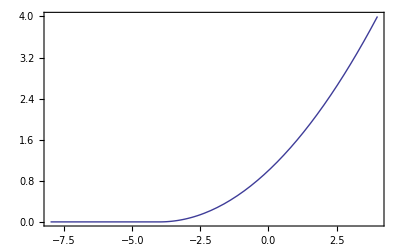

Derivative of penfuncsqr:

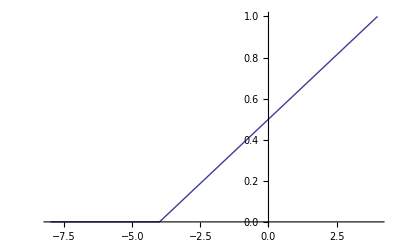

Exponential quadratic penalty function penfuncexpsqr:

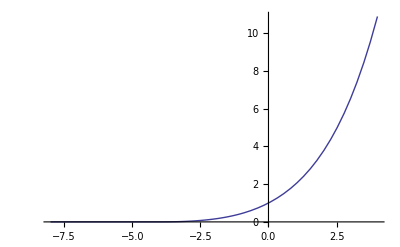

Derivative of penfuncexpsqr:

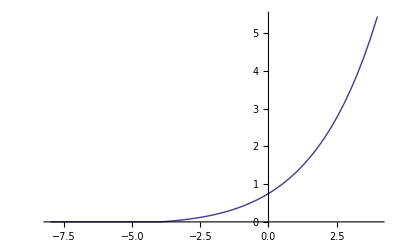

Penalty function with a jump - penfuncjump:

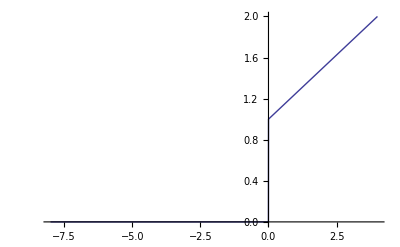

Derivative of penfuncjump:

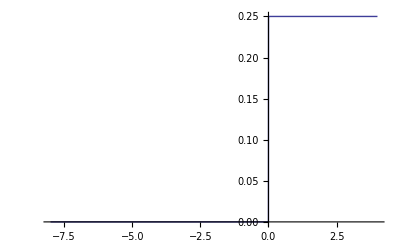

```mathematica
Module[{d=4,h=1,k,func=penfuncsqr,derfunc=derpenfuncsqr},
If[testmode≠0,
k:=h/d;
Print["d = ",d,", h = ",h,", k = ",k];
(* Square penalty function: *)
plpenfuncsqr=Plot[penfuncsqr [c,{d,h}],  {c,-2*d,d} , 
PlotRange->All,Frame->True];
plderpenfuncsqr=Plot[derpenfuncsqr [c,{d,h}],  {c,-2*d,d} , PlotRange->All];

(* Exponential-quadratic penalty function: *)
plpenfuncexpsqr=Plot[penfuncexpsqr [c,{d,h}],  {c,-2*d,d} , PlotRange->All];
plderpenfuncexpsqr=Plot[derpenfuncexpsqr [c,{d,h}],  {c,-2*d,d} , PlotRange->All];

(* Jump penalty function: *)
plpenfuncjump=Plot[penfuncjump [c,{h,k}],  {c,-2*d,d} , PlotRange->All];
plderpenfuncjump=Plot[derpenfuncjump [c,{h,k}],  {c,-2*d,d} , PlotRange->All];

];
];

(* Show the graphs: *)
If[testmode≠0,
Print["Penalty function penfuncsqr:"];
Show[   plpenfuncsqr   ]   ]
If[testmode≠0,
Print["Derivative of penfuncsqr:"];
Show[   plderpenfuncsqr   ]  ]

If[testmode≠0,
Print["Exponential quadratic penalty function penfuncexpsqr:"];
Show[   plpenfuncexpsqr   ]   ]
If[testmode≠0,
Print["Derivative of penfuncexpsqr:"];
Show[   plderpenfuncexpsqr   ]  ]

If[testmode≠0,
Print["Penalty function with a jump - penfuncjump:"];
Show[   plpenfuncjump   ]   ]
If[testmode≠0,
Print["Derivative of penfuncjump:"];
Show[   plderpenfuncjump   ]  ]
```

### Tests (penalty functions):

#### Test of penalty generating functions :

```mathematica
If[  testmode≠   0   ,
ccc=-0.001023;

penfunc=penfuncexp;
derpenfuncarg=derpenfuncexp;

penfunc=penfuncexpsqr;
derpenfuncarg=derpenfuncexpsqr;

Needs["NumericalCalculus`"];
Print[   derpenfuncarg[ccc,param]    ];
Print[   D[penfunc[x,param],x]  /. x->ccc    ];
Print[   ND[penfunc[x,param],x,ccc]    ];
]
```

2.99292

2.99292

2.99292

#### Tests with anfuncsimpconstr :

```mathematica
If   [   testmode≠0, 
(* Input data: *)
param={0,0,0};
param={1.1,1.1,1.1};
param={1.01,1.01,1.01};
param={1.01,1.01};
calcobj=calcconstr=calcgradobj=calcgradconstr=1;
anfuncorig=anfuncsimpconstr;
ancdorig={"an cd orig"};

(* Penalty generating function: *)

penfunc=penfuncexp;
derpenfuncarg=derpenfuncexp;

penfunc=penfuncexpsqr;
derpenfuncarg=derpenfuncexpsqr;

penparam={dd,hh}={0.1,1.00001};
defderpenfunc= 22563 ;  (* flag for whether penalty function is defined or not *)

keepconstraints=123;  (* flag for whether to keep constraints in the oeriginal function *)


(* parameters (penalty deifnition data) arranged for output: *)
argtab:=Transpose[{{"anfuncorig","ancdorig","penfunc","penparam","defderpenfunc","derpenfuncarg","keepconstraints"},{anfuncorig, ancdorig,  penfunc, penparam,  defderpenfunc, derpenfuncarg, keepconstraints }}];

(* Form definition data for penalty analysis function: *)
cdpen := {  anfuncorig, ancdorig,  penfunc, penparam,  defderpenfunc, derpenfuncarg, keepconstraints  };


anres=anfuncorig[param,1,1,1,1,ancdorig];
penres=penaltyanfunc[param,1,1,1,1,cdpen ];

(*   Extract objective & constraint functions values, calculate penalty terms   *)
tabconstr=anres[[4]];
tabgradconstr=anres[[8]];
objfunc=anres[[2]];
gradobjfunc=anres[[6]];
penobjfunc=penres[[2]];
pengradobjfunc=penres[[6]];

penterms=Table[
{
tabconstr[[i]],
penfunc[tabconstr[[i]],penparam],
tabgradconstr[[i]]  *  derpenfuncarg[tabconstr[[i]],penparam]
},  {i,1,Length[tabconstr]}
];
tabpenterms=Join[{{"constraint f.","penalty term","penalty term derivative"}},penterms];

(*    Calculate penalty addition (sum of penalty terms) and its gradient:    *)
penalty=Sum[penterms[[i,2]],{i,1,Length[penterms]}];
gradpenalty=Sum[penterms[[i,3]],{i,1,Length[penterms]}];

Print["\n\n\nDefinition data for penalty analysis function: \n", TableForm[argtab]   ];
Print["\nOriginal analysis results: \n  ",anres];
Print["\nPenalty analysis function results: \n  ",penres];

Print["\nPenalty terms: \n",TableForm[tabpenterms]];

Print["\nObjective function (original): ",objfunc];
Print["Penalty function (calculated by hand): ",objfunc+penalty];
Print["Penalty function (from pen. analysis): ",penobjfunc];

Print["\nGradient of objective function (original): ",gradobjfunc];
Print["Gradient of penalty function (calculated by hand): ",gradobjfunc+gradpenalty];
Print["Gradient of penalty function (from pen. analysis): ",pengradobjfunc];
]
```

Definition data for penalty analysis function: 
anfuncorig | anfuncsimpconstr
ancdorig | an cd orig
penfunc | penfuncexpsqr
penparam | 0.1
1.00001
defderpenfunc | 22563
derpenfuncarg | derpenfuncexpsqr
keepconstraints | 123

Original analysis results: 
  {1.,2.0402,1.,{-0.015,-0.02},1.,{2.02,2.02},1.,{{-1.5,0.},{0.,-2.}},0.}

Penalty analysis function results: 
  {1.,3.18606,1.,{-0.015,-0.02},1.,{-29.2563,-34.6595},1.,{{-1.5,0.},{0.,-2.}},0.}

Penalty terms: 
constraint f. | penalty term | penalty term derivative
-0.015 | 0.621868 | -31.2763
0.
-0.02 | 0.523993 | 0.
-36.6795

Objective function (original): 2.0402

Penalty function (calculated by hand): 3.18606

Penalty function (from pen. analysis): 3.18606

Gradient of objective function (original): {2.02,2.02}

Gradient of penalty function (calculated by hand): {-29.2563,-34.6595}

Gradient of penalty function (from pen. analysis): {-29.2563,-34.6595}

```mathematica
(* Test for changing composition of the definition data for the penalty function - change this   *)
If[testmode≠0,
cdpen := {  anfuncorig, ancdorig,  penfunc, penparam,  defderpenfunc, derpenfuncarg, keepconstraints  };

cdpen := {  anfuncorig, ancdorig,  penfunc, penparam  };

keepconstraints=0;
penfunc=penfuncexpsqr;
derpenfuncarg=derpenfuncexpsqr;

defderpenfunc=   1   ;

If[defderpenfunc==0,
derpenfuncarg=nofunc;
];

penaltyanfuncconstr[param,1,1,1,1,cdpen ]
]
```

{1.,3.18606,1.,{-0.015,-0.02},1.,{-29.2563,-34.6595},1.,{{-1.5,0.},{0.,-2.}},0.}

## Numerical gradients, gradient checks & analysis transforms

### Selsection of parameters

parindtonames [select, paramnamesall]
   - Creates a list of parameter names selected from paramnamesall (a list of all parameter names) that corresponds to parameter indices in selection list selsct. select can be arbitrarily nested list. 
getgradsel [grad, select]
    - Returns a reduced gradient according to reduced parameters select, where full gradient (with respect to all parameters) is grad.
setparamsel [p0, select, paramall] - returns a full parameter list if p0 is a reduced set of parameters, select is a list of indices of parameters in the full set corresponding to parameters from reduced set, and paramall is a list of default values for the full set of parameters.

Form of selection indices:
{p1, {p21, p22, p23}, p3, p4} means the following: 1st parameter from reduced set defines parameter with index p1 in the full set, 2nd parameter from the reduced set defines parameters p21, p22, p23 from the full set, 3rd parameter form the reduced set defines parameter p3 from the full set, and 4th parameter from the reduced set defines the parameter with index p4 in the full set. Other parameters in the full set have referential values defined in paramall.

```mathematica
parindtonames[select_,paramnamesall_]:=Module[{ret,cur,i},
(* Converts a parameter selection list containing indices to a list containing names: *)
If[Depth[select]==1,Return[paramnamesall[[select]]]];
(*
Table[paramnamesall[[select[[i]]]],{i,1,Length[select]}]
*)
Table[parindtonames[select[[i]],paramnamesall],{i,1,Length[select]}]
];

getgradsel[ grad_,select_]:=Module[{gradsel,val,depend,i,j},
(* Change gradient with respect to all parameters to gradient with respect to selected parameters: *)
gradsel={};
(*   Print["grad: " ,grad]   *)
For[i=1,i≤Length[select],i=i+1,
depend=select[[i]];
If[Depth[depend]<2,
depend={depend};    (* generic parameters that depend on a specific parameter *)
];
AppendTo[gradsel,
Sum[grad[[ depend[[j]] ]],{j,1,Length[depend]}]
];
(*  Print["i: ",i,", depend: ",depend,", gradsel: ",gradsel]  *)
];
gradsel
];


setparamsel[p0_,select_,paramall_]:=Module[{ret,cur,i,j,p,depend},
(* Sets generic parameters according to reduced parameters and selection list: *)
p=paramall;
For[i=1,i≤Length[select],i=i+1,
depend=select[[i]];
If[Depth[depend]<2,
depend={depend};    (* indices of generic parameters that depend on a specific parameter *)
];
For[j=1,j≤Length[depend],j=j+1,
p[[depend[[j]] ]]=p0[[i]];
];
];
p
];
```

### Numerical gradient analysis function anfuncnumgrad [..., {anfunc, ancd, step, <results>} ] ... are standard parameters of analysis functions, and definition data consists of the analysis function (anfunc, symbol), definition data passed to this function (ancd), and step size for numerical definition (step, can be vector or scalar - in this case teh same step is used for all parameters). ... = param, calcobj, calcconstr, calcgradobj, calcgradconstr Definition data can also contain results, in which case actual analysis does not need to be performed, but these results are used for unperturbed parameters. This can be used if results at unperturbed parameters have been calculated elsewhere.

```mathematica
anfuncnumgrad[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,ret=0,
calcobj1,calcconstr1,calcgradobj1,calcgradconstr1,ret1,
p2,
calcobj2,calcconstr2,calcgradobj2,calcgradconstr2,ret2,
obj1=0,constr1={},gradobj1={},gradconstr1={},obj2=0,constr2={},gradobj2={},gradconstr2={},
result, 
anfunc, ancd ,
i,j},
(* $A Igor feb06; *)

anfunc=cd[[1]];
ancd=cd[[2]];
step=cd[[3]];
If[Depth[step]<2,
step=Table[step,{i,1,Length[p]}];
];

If[Length[cd]>3,
(* Results at unperturbed parameters are already available, we just copy these results: *)
result={calcobj1,obj1,calcconstr1,constr1,calcgradobj1,gradobj1,calcgradconstr1,gradconstr1,ret1}=cd[[4]],
(* Results at unperturbed parameters are not available, perform calculation: *)
result={calcobj1,obj1,calcconstr1,constr1,calcgradobj1,gradobj1,calcgradconstr1,gradconstr1,ret1}= anfunc[p,1,1,1,1,ancd];
];

gradobj1=Table[0,{i,1,Length[p]}];
If[Length[constr1]>0,
gradconstr1=Table[Table[0,{j,1,Length[p]}],{i,1,Length[constr1]}];
];

(* Note in returned value if something could not be calcuated: *)
If[calcobj1==0,
retcalcobj=retcalcgradobj=0;
If[calcobj≠0 || calcgradobj≠0,ret=-1];
];
If[calcconstr1==0,
retcalcconstr=retcalcgradconstr=0;
If[calcconstr≠0 || calcgradconstr≠0,ret=-1];
];

If[debugmode≠0,
Print["Perturbed component ",0,", parameters: ",N[p],", Analysis result: \n  ",N[result],"\nObjective gradient: ",N[gradobj1]," Constraint gradients: ",N[gradconstr1]];
];

For[i=1,i≤Length[p],i=i+1,
(* analysis with parameter i perturbed: *)
p2=p;
p2[[i]]=p2[[i]]+step[[i]];
result={calcobj2,obj2,calcconstr2,constr2,calcgradobj2,gradobj2,calcgradconstr2,gradconstr2,ret2}= anfunc[p2,1,1,0,0,ancd];
(* Note in returned value if something could not be calcuated: *)
If[calcobj2==0,
retcalcobj=retcalcgradobj=0;
If[calcobj≠0 || calcgradobj≠0,ret=-1];
,
(* By the difference, calculate component of objective gradient: *)
gradobj1[[i]]=(obj2-obj1)/step[[i]];
];
If[calcconstr2==0,
retcalcconstr=retcalcgradconstr=0;
If[calcconstr≠0 || calcgradconstr≠0,ret=-1];
,
(* By the difference, calculate components of constraint gradients: *)
For [j=1,j≤Length[constr1],j=j+1,
gradconstr1[[j,i]]=(constr2[[j]]-constr1[[j]])/step[[i]];
];
];

If[debugmode≠0,
Print["Perturbed component ",i,", parameters: ",N[p2],", Analysis result: \n  ",N[result],"\nObjective gradient: ",N[gradobj1]," Constraint gradients: ",N[gradconstr1]];
];

];
Return[
{retcalcobj,obj1,
retcalcconstr,constr1,
retcalcgradobj,gradobj1,
retcalcgradconstr,gradconstr1,
ret}
];
];
```

### Test of analytical gradients returned by an analysis function: testangrad [anfunc, ancd, param, step] - compares analytical gradient of objective and constraint functions calculated by anfunc with numerical gradients. anfunc - analysis functios that is checked ancd - definition data for anfunc param - parameters at which check is performed step - step size for numerical differentiation; It can be a number (the same step used for all components) or a vector (different step sizes for different components)

```mathematica
testangrad[anfunc_,ancd_,param_,step_]:=Module[{
calcobj1,calcconstr1,calcgradobj1,calcgradconstr1,ret1,
calcobj2,calcconstr2,calcgradobj2,calcgradconstr2,ret2 },
(* $A Igor feb06; *)

{calcobj1,obj1,calcconstr1,constr1,calcgradobj1,gradobj1,calcgradconstr1,gradconstr1,ret1}= anfunc[param,1,1,1,1,ancd];

{calcobj2,obj2,calcconstr2,constr2,calcgradobj2,gradobj2,calcgradconstr2,gradconstr2,ret2}=anfuncnumgrad[param,1,1,1,1,{anfunc,ancd,step}];

If[calcobj1≠0,
Print["Objective function gradient:"];
Print["Analytical:\n  ",N[gradobj1]];
Print["Numerical:\n  ",N[gradobj2]];
Print["Difference:\n  ",N[gradobj1-gradobj2]];
Print["Relative difference:\n  ",N[(gradobj1-gradobj2)/gradobj1]];
];

If[calcconstr1≠0,
Print["\n\nConstraint functions gradients:"];
Print["Analytical:\n  ",N[gradconstr1]];
Print["Numerical:\n  ",N[gradconstr2]];
Print["Difference:\n  ",N[gradconstr1-gradconstr2]];
Print["Relative difference:\n  ",N[(gradconstr1-gradconstr2)/gradconstr1]];
];
];
```

#### Test of gradients for testanfunc1:

```mathematica
If[testmode≠0,
testangrad[anfuncsimpconstr,"3",{3,3,3},10^-5];
,,]
```

```mathematica
If[testmode≠0,
param={1,1};
testangrad[testanfunc1,"cd",param,10^-6]  ;
,,]
```

```mathematica
If[testmode≠0,
param
,,]
```

```mathematica
If[testmode≠0,
testanfunc1[param,1,1,1,1,"cd"]
,,]
```

```mathematica
If[testmode≠0,
anfuncnumgrad[param,1,1,1,1,{testanfunc1,"cd",10^-6}]
,,]
```

```mathematica
If[testmode≠0,
testanfunc1[param,1,1,1,1,"cd"]
,,]
```

## Manipulating tables of analysis resuts

Analysis and algorithm history
Note: for history records, choose another file than for other purposes, since this file is often deleted
algorithm history is usually reset by each algorithm, as opposed to analysis history, where analysis points are continuously appended to the current history.

### Initialization of global history variables:

```mathematica
recanhistory=1;   (* whether to record analysis history *)
recalghistory=1;   (* whether to record algorithm history *)
noteanhistory=0;   (* whether to print notifications when recording an. history *)
notealghistory=0;   (* whether to print notifications when recording alg. history *)
rewriteanhistory=1;  (* when writing to file, rewrite previous history *)
rewritealghistory=1;  (* when writing to file, rewrite previous history *)
anhistory={};      (* analysis histry (table of analysis points) *)
alghistory={};      (* algorithm histry (table of analysis points or their tables) *)
saveanhistory={};
savealghistory={};
fileanhistory="anhistory.out";  (* file where analysis history is recorded *)
filealghistory="alghistory.out";    (* file where algorithm history is recorded *)
```

### Functions for manipulating analysis and algorithm history:

```mathematica
(resetalghistory[]:=resetalghistory[recalghistory,filealghistory];) (resetalghistory[record_,filename_]:=Module[{},recalghistory=record;filealghistory=filename;alghistory={};savealghistory={};];) (resetanhistory[]:=resetanhistory[recanhistory,fileanhistory];) (resetanhistory[record_,filename_]:=Module[{},recanhistory=record;fileanhistory=filename;anhistory={};saveanhistory={};];) (resethistory[record_,filename_]:=Module[{},resetalghistory[record,filename];resetanhistory[record,filename];];) (resethistory[]:=Module[{},resetalghistory[];resetanhistory[];];) (storealghistory[functionname_,table_]:=Module[{},If[recalghistory||recalghistory≠0,If[notealghistory||notealghistory≠0,Print[functionname,": Algorithm progress stored to variable \"alghistory\"."];];alghistory=table;If[Head[filealghistory]==String,If[StringLength[filealghistory]>0,If[rewritealghistory||rewritealghistory≠0,Put["Algorithm hisrory file",DateList[],filealghistory];];PutAppend["Algorithm history, from "<>ToString[functionname]<>"; date:",DateList[],filealghistory];Save[filealghistory,alghistory];];];];];) (appendalghistory[functionname_,elemet_]:=Module[{},If[recalghistory||recalghistory≠0,If[notealghistory||notealghistory≠0,Print[functionname,": Algorithm history appended, variable \"alghistory\"."];];If[Depth[alghistory]<2,alghistory={};];AppendTo[alghistory,elemet];If[Head[filealghistory]==String,If[StringLength[filealghistory]>0,If[rewritealghistory||rewritealghistory≠0,Put["Algorithm hisrory file",DateList[],filealghistory];];PutAppend["Algorithm history, from "<>ToString[functionname]<>"; date:",DateList[],filealghistory];Save[filealghistory,alghistory];];];];];) (storeanhistory[functionname_,table_]:=Module[{},If[recanhistory||recanhistory≠0,If[noteanhistory||noteanhistory≠0,Print[functionname,": Table of analysis points stored to variable \"anhistory\"."];];anhistory=table;If[Head[fileanhistory]==String,If[StringLength[fileanhistory]>0,If[rewriteanhistory||rewriteanhistory≠0,Put["Analysis hisrory file",DateList[],fileanhistory];];PutAppend["Analysis history, from "<>ToString[functionname]<>"; date:",DateList[],fileanhistory];Save[fileanhistory,anhistory];];];];];) (appendanhistory[functionname_,elemet_]:=Module[{},If[recanhistory||recanhistory≠0,If[noteanhistory||noteanhistory≠0,Print[functionname,": Analysis history appended, variable \"anhistory\"."];];If[Depth[anhistory]<2,anhistory={};];AppendTo[anhistory,elemet];If[Head[fileanhistory]==String,If[StringLength[fileanhistory]>0,If[rewriteanhistory||rewriteanhistory≠0,Put["Analysis hisrory file",DateList[],fileanhistory];];PutAppend["Analysis history, from "<>ToString[functionname]<>"; date:",DateList[],fileanhistory];Save[fileanhistory,anhistory];];];];];)
```

Null^10

### Tests of functions for manipulating analysis and algorithm history:

```mathematica
If[testmode≠0,
(*
fileanhistory  =  filealghistory=  "test.out";
recanhistory=1;
recalghistory=1;
noteanhistory=1;
notealghistory=1;
*)
(* Empty contents of history files: *)
Put["Beginning of history file.",filealghistory];
,,]
```

#### Storing complete algorihm history:

```mathematica
If[testmode≠0,
storealghistory["testfunction",{"algel1","algel2"}];
Import[filealghistory,"Text"]
,,]
```

#### Appending data to algorihm history:

```mathematica
If[testmode≠0,
appendalghistory["testfunction","New element"];
Import[filealghistory,"Text"]
,,]
```

#### Storing complete analysis history:

```mathematica
If[testmode≠0,
storeanhistory["testanalysisfunction",{"analysis1","analysis2"}];
Import[fileanhistory,"Text"]
,,]
```

#### Appending data to analysis history:

```mathematica
If[testmode≠0,
appendanhistory["testanalysisfunction","New analysis"];
Import[filealghistory,"Text"]
,,]
```

Calculating factors and intervals for tables with geometrical growth of interval lengths:

#### Factors for tables with specified edge points:

```mathematica
tabexpfactors[numpt_,fact_]:=tabexpfactint[numpt,fact][[1]];

tabexpfactint[numptarg_,fact_]:=Module[{ret,numpt,sumint,intervals,factors},
(* $A Igor mar06; *)
numpt=Round[numptarg];
intervals=Table[0,{i,1,numpt-1}];
factors=Table[0,{i,1,numpt}];
inter=1;    (* current interval (non-normalized) *)
sumint=0;  (* sum of intervals - normalizing factor at the end *)
For[i=1,i<numpt,i=i+1,
intervals[[i]]=inter;
sumint=sumint+inter;
factors[[i+1]]=sumint;
inter=inter*fact;
];
intervals=intervals/sumint;
factors=factors/sumint;
N[ {factors,intervals} ]
];
```

#### Factors for tables with specified central and edge point:

```mathematica
tabexpfactorscent[numpt_,fact_]:=Module[{},
(* $A Igor mar06; *)
If[Mod[numpt,2]==0,
Return[tabexpfactorscent[numpt+1,fact]];
];
Join[
Reverse[
Drop[
-tabexpfactors[(numpt+1)/2,fact],
1]
],
tabexpfactors[(numpt+1)/2,fact]
]
];

tabexpfactintcent[numpt_,fact_]:=Module[{factors,i},
(* $A Igor mar06; *)
factors=tabexpfactorscent[numpt,fact];
Return[{factors,
Table[factors[[i+1]]-factors[[i]],{i,1,Length[factors]-1}]
}];
];
```

Function for calculating  analysis points and tables of analysis points:

```mathematica
testpoint=calcanpt[anfuncsimpconstr,{1.11,2.22},11,22,33,44,"1"]
```

calcanpt[anfuncsimpconstr,{1.11,2.22},11,22,33,44,1]

Analysis point is a list that consists at least of 3 parts:
    { param, res, args, ... }
where param is a vector of parameters, res is a vector of results, args are arguments {calcobj, calcconstr, calcgradobj and calcgradconstr, cd} passed to the analysis function. Further arguments are lists of indices and lists of factors, and there can be even further arguments, too.
  param = { p1, p2, ... }
  res = { calcobj, obj, calcconstr, { c1, c2, ... }, calcgradobj, { DoDp1, DobjDp2, ... }, calcgradconstr, { { Dc1Dp1, Dc1Dp2, Dc1Dp3, ... }, {  Dc2Dp1, Dc2Dp2, Dc2Dp3, ... }, ret  }
  args = { reqcalcobj, reqcalcconstr, reqcalcgradobj, reqcalcgradconstr, cd }
  calcobj, calcconstr, calcgradobj, calcgradconstr - calculation flags that tell whether the objective function, constraints, gradients of the objective function and gradients of constraints have been calculated (0 for no and non-zero for yes)
  reqcalcobj, reqcalcconstr, reqcalcgradobj, reqcalcgradconstr - request flags that request calculation of given quantities, as were passed to the analysis
  cd - definition data passed to the analysis function
  p1, p2, ... - values of optimization parameters at which analysis has been performed
  obj - value of the objective function
  c1, c2, c3 - values of the constraint functions
  DoDp1, DoDp2, DoDp3 - derivatives of the objective function with respect to individual parameters (components of objective function gradient)
  Dc1Dp1, Dc1Dp2, ..., Dc2Dp1, ... - derivatives of individual constraint functions with respect to optimization parameters (components of constraint gradients)
  ret - error code of analysis (0 for no error)
  
Example:
{ {1.11, 2.22}, { 1, 6.1605, 1, {-0.165, -2.44} , 1, {2.22, 4.44}, 1, { {-1.5, 0.}, {0., -2.} }, 0 }, { 1, 1, 1, 1, "3" }}

#### calcanpt [anfunc, p, calcobj, calcconstr, calcgradobj, calcgradconstr, cd] runs analysis defined by anfunc at parameters p and with specification arguments calcobj, calcconstr, calcgradobj, calcgradconstr, cd for the analysis

```mathematica
calcanpt[analysisfunction_,p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
(* $A Igor mar06; *)
{
p,
analysisfunction[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd],
{calcobj,calcconstr,calcgradobj,calcgradconstr,cd}
}
```

#### Functions that extract information from analysis points: anptparam, anptres, anptarg, anptind, anptfact, anptcalcobj, anptobj, ..., anptret, anptargcalcobj, ..., anptargspec

```mathematica
(* $A Igor mar06; *)

(* Parameters: *)
anptparam[pt_]:=If[Length[pt]≥1,
Return[pt[[1]]],
Print["Error in anptparam: Invalid structure of analysis point.\n"];
Return[{}];
];

(* Specific parameter: *)
anptparami[pt_,i_]:=Module[{param},
param=anptparam[pt];
If[Length[param]≥Abs[i],
Return[param[[i]]],
Print["Error in anptparami: index ",i," out of range ",Length[param]];
Return[0];
];
];

(* Results: *)
anptres[pt_]:=If[Length[pt]≥2,
Return[pt[[2]]],
Print["Error in anptres: Invalid structure of analysis point, less than 2 elements.\n"];
Return[{}];
];

(* Results - calculated flag for objective function: *)
anptcalcobj[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥1,
Return[res[[1]]],
Print["Error in anptcalcobj: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Results - objective function: *)
anptobj[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥2,
Return[res[[2]]],
Print["Error in anptobj: Invalid structure of analysis resuts: ",res];
Return[0];
];
];


(* Results - calculation flag for gradient of objective function: *)
anptcalcgradobj[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥5,
Return[res[[5]]],
Print["Error in anptcalcgradobj: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Results - gradient of objective function: *)
anptgradobj[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥6,
Return[res[[6]]],
Print["Error in anptgradobj: Invalid structure of analysis resuts: ",res];
Return[0];
];
];


(* Results - calculation flag for constraint functions: *)
anptcalcconstr[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥3,
Return[res[[3]]],
Print["Error in anptcalcconstr: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Results - constraint functions: *)
anptconstr[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥4,
Return[res[[4]]],
Print["Error in anptconstr: Invalid structure of analysis resuts: ",res];
Return[0];
];
];


(* Results - calculation flag for gradients of constraint functions: *)
anptcalcgradconstr[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥7,
Return[res[[7]]],
Print["Error in anptcalcgradconstr: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Results - gradients of constraint functions: *)
anptgradconstr[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥8,
Return[res[[8]]],
Print["Error in anptgradconstr: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Results - return value: *)
anptret[pt_]:=Module[{res},
res=anptres[pt];
If[Length[res]≥9,
Return[res[[9]]],
Print["Error in anptret: Invalid structure of analysis resuts: ",res];
Return[0];
];
];

(* Arguments to analysis function: *)
anptarg[pt_]:=If[Length[pt]≥3,
Return[pt[[3]]],
Print["Error in anptarg: Invalid structure of analysis point, less than 3 elements.\n"];
Return[{}];
];

(* Arguments to analysis function - calculation request for objective function: *)
anptargcalcobj[pt_]:=Module[{args},
args=anptargs[pt];
If[Length[args]≥1,
Return[args[[1]]],
Print["Error in anptargcalcobj: Invalid structure of analysis specification arguments (should be {calcobj, calcconstr, calcgradobj, calcgradconstr, cd}): ",args];
Return[0];
];
];

(* Arguments to analysis function - calculation request for constraint functions: *)
anptargcalcconstr[pt_]:=Module[{args},
args=anptargs[pt];
If[Length[args]≥2,
Return[args[[2]]],
Print["Error in anptargcalcconstr: Invalid structure of analysis specification arguments (should be {calcobj, calcconstr, calcgradobj, calcgradconstr, cd}): ",args];
Return[0];
];
];

(* Arguments to analysis function - calculation request for gradient of objective functions: *)
anptargcalcgradobj[pt_]:=Module[{args},
args=anptargs[pt];
If[Length[args]≥3,
Return[args[[3]]],
Print["Error in anptargcalcgradobj: Invalid structure of analysis specification arguments (should be {calcobj, calcconstr, calcgradobj, calcgradconstr, cd}): ",args];
Return[0];
];
];

(* Arguments to analysis function - calculation request for gradient of objective functions: *)
anptargcalcgradconstr[pt_]:=Module[{args},
args=anptargs[pt];
If[Length[args]≥4,
Return[args[[4]]],
Print["Error in anptargcalcgradconstr: Invalid structure of analysis specification arguments (should be {calcobj, calcconstr, calcgradobj, calcgradconstr, cd}): ",args];
Return[0];
];
];

(* Arguments to analysis function - specification argument: *)
anptargspec[pt_]:=Module[{args},
args=anptargs[pt];
If[Length[args]≥5,
Return[args[[5]]],
Print["Error in anptargspec: Invalid structure of analysis specification arguments (should be {calcobj, calcconstr, calcgradobj, calcgradconstr, cd}): ",args];
Return[0];
];
];

(* Table indices: *)
anptind[pt_]:=If[Length[pt]≥4,
Return[pt[[4]]],
Print["Error in anptind: Table indices are not available for this analysis point.\n"];
Return[{}];
];

(* Table factors: *)
anptfact[pt_]:=If[Length[pt]≥5,
Return[pt[[5]]],
Print["Error in anptfact: Table factors are not available for this analysis point.\n"];
Return[{}];
];
```

#### tabanptrand [num,anfunc, p1, p2, calcobj, calcconstr, calcgradobj, calcgradconstr, cd] num - number of analyses performed anfunc - analysis function p1 - lower limitd for parameters p2 - upper limits for parameters calcoj, calcconstr, calcgradobj, calcgradconstr - calculation flags for analysis cd - definition data for analysis Runs a set of analyses defined by anfunc in random points on the iterval specified by interval limits p1 and p2, with specification arguments calcobj, calcconstr, calcgradobj, calcgradconstr, cd for individual analyses. Function can have an additional argument, which instructs (if different than 0) to print intermediate results after calculation of each complete row of the table. Returns a list of analysis points with indices and factors appended to the standard analysis data. The form of results is { { {param_1}, {analysisresults_1}, {specargs_1}, {index_1}, {factor_1} }, { {param_2}, {analysisresults_2}, {specargs_2}, {index_2}, {factor_2} }, ..., } where param_i is vector of parameters at which the i-th analysis of the table is performed, analysisresults_i is a list of results of this analysis (in the standard form), specargs_i is the list of specification arguments at which the analysis was called, index_i is the index of a particular analysis (running from 1 to Length[factors]), and factor_i contains the list of random numbers used for calculation of parameters. tabanptrand - similar fut central value for parameters and interval lengths are specified as p1 and p0.

```mathematica
tabanptrand[num_,anfunc_,p1_,p2_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=tabanptrand[num,anfunc,p1,p2,calcobj,calcconstr,calcgradobj,calcgradconstr,cd,0];
tabanptrand[num_,anfunc_,p1_,p2_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_,printpartialresults_]:=Module[{i,j,k,tabk,ret,title,randfactors,randpar,t1,t2,t3,t4},Print["tabanptrand: lower lim.: ",p1,", upper lim.: ",p2];ret={};For[i=1,i≤num,i=i+1,t1=TimeUsed[];randfactors=Table[RandomReal[],{j,1,Length[p1]}];randpar=Table[p1⟦j⟧+randfactors⟦j⟧ (p2⟦j⟧-p1⟦j⟧),{j,1,Length[p1]}];t2=TimeUsed[];AppendTo[ret,Join[calcanpt[anfunc,randpar,calcobj,calcconstr,calcgradobj,calcgradconstr,cd],{{i}},{randfactors}]];t3=TimeUsed[];title="tabanptrand: partial results (up to el. "<>ToString[i]<>" of "<>ToString[num]<>"): ";If[printpartialresults≠0,Print[title,"\n",ret];];storealghistory[title,ret];];Return[ret];];
tabanptrandcent[num_,anfunc_,p0_,dp_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_,printpartialresults_]:=tabanptrand[num,anfunc,p0-0.5 dp,p0+0.5 dp,calcobj,calcconstr,calcgradobj,calcgradconstr,cd,printpartialresults];
tabanptrandcent[num_,anfunc_,p1_,p2_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=tabanptrandcent[num,anfunc,p1,p2,calcobj,calcconstr,calcgradobj,calcgradconstr,cd,0];
```

#### tabanpt1d [anfunc, p0, p1, factors, calcobj, calcconstr, calcgradobj, calcgradconstr, cd] Runs a table of analyses defined by anfunc on a line between p0 and p1, and with factors defining relative distances from p0 (expressed in ||p1-p0||), and specification arguments calcobj, calcconstr, calcgradobj, calcgradconstr, cd for individual analyses. Function can have an additional argument, which instructs (if different than 0) to print intermediate results after calculation of each complete row of the table. Returns an one dimensional list of analysis points with indices and factors appended to the standard analysis data. The form of results is { { {param_1}, {analysisresults_1}, {specargs_1}, {index_1}, {factor_1} }, { {param_2}, {analysisresults_2}, {specargs_2}, {index_2}, {factor_2} }, ..., } where param_i is vector of parameters at which th

```mathematica
tabanpt1d[anfunc_,p0_,p1_,factors_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=tabanpt1d[anfunc,p0,p1,factors,calcobj,calcconstr,calcgradobj,calcgradconstr,cd,0];

tabanpt1d[anfunc_,p0_,p1_,factors_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_,    printpartialresults_]:=
Module[{i,tabk,ret,title},
(* $A Igor mar06; *)
tabk=N[factors];
ret={};
For[i=1,i<=Length[tabk],i=i+1,
AppendTo[ret,
Join[
calcanpt[anfunc,p0+tabk[[i]]*(p1-p0),calcobj,calcconstr,calcgradobj,calcgradconstr,cd],
{{i}},{{tabk[[i]]}}
]
];

title=StringJoin["tabanpt1d: partial results (up to el. ",ToString[i]," of ",ToString[Length[tabk]],"): "];
If[printpartialresults≠0,
Print[title,"\n",ret];
];
(* Record progress of the table up to now, according to global control variables: *)
storealghistory[title,ret];

];

Return[ret];
];
```

#### tabanpt2d [anfunc, p0, p1, p2, factors1, factors2, calcobj, calcconstr, calcgradobj, calcgradconstr, cd] Runs a two dimensional table of analyses defined by anfunc on a plane defined by lines beteen (p0 and p1), and (p0 and p2), with factors defining relative distances from p0 (expressed in ||p1-p0|| and ||p1-p0||, respectively), and specification arguments calcobj, calcconstr, calcgradobj, calcgradconstr, cd for individual analyses. Otherwise the function works similar than tabanpt1d. Function can have an additional argument, which instructs (if different than 0) to print intermediate results after calculation of each complete row of the table. The returned analysis points are arranged in a 2 dimensional list, with the second index running faster. A two dimensional list of corresponding indices and a two dimensional list of corresponding factors are appended to each set of standard analysis point data. Function returns a two dimensional table of analysis points with lists of element indices and factors appended to standard analysis point data. The format of returned data is { {anpt_1_1, anpt_1_2, ...}, {anpt_2_1, anpt_2_2, ...}, ... } where the format of anpt_i_j is { {param_i_j}, {analysisresults_i_j}, {specargs_i}, {index_i_j}, {factor_i_j} } and {index_i_j} is a list of two indices and {factor_i_j} a list of two factors (along to the first and second direction, i.e. along (p1-p0) and (p2-p0)).

```mathematica
tabanpt2d[anfunc_,p0_,p1_,p2_,factors1_,factors2_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=tabanpt2d[anfunc,p0,p1,p2,factors1,factors2,calcobj,calcconstr,calcgradobj,calcgradconstr,cd,0];


tabanpt2d[anfunc_,p0_,p1_,p2_,factors1_,factors2_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_,    printpartialresults_]:=
Module[{i,j,tabk1,tabk2,ret},
(* $A Igor mar06; *)
tabk1=N[factors1];
tabk2=N[factors2];
ret={};
For[i=1,i≤Length[tabk1],i=i+1,
AppendTo[ret,
Table[
Join[
calcanpt[anfunc,p0+tabk1[[i]]*(p1-p0)+tabk2[[j]]*(p2-p0),calcobj,calcconstr,calcgradobj,calcgradconstr,cd],
{{i,j}},{{tabk1[[i]],tabk2[[j]]}}
],
{j,1,Length[tabk2]}
]
];

title=StringJoin["tabanpt2d: partial results (up to row ",ToString[i]," of ",ToString[Length[tabk1]],"): "];
If[printpartialresults≠0,
Print[title,"\n",ret];
];
(* Record progress of the table up to now, according to global control variables: *)
storealghistory[title,ret];

];  (* For *)
Return[ret];
];
```

#### flattentabanpt [ tab ] Returns a flattened table of analysis points tab in such a way that the returned table is a simple list of all analysis points contained in tab. If tab is a single analysis point (not a list of them) then {tab} is returned. If tab is a list of lists of analysis points then Flatten[tab] is returned, and so on recursively until the returned value is a simple 1D list of analysis points. Criteria for application of flattening is checking depth of res[[1,1]], which must be at the final stage vector of parameters of the first analysis point (with depth 1).

```mathematica
flattentabanpt[tab_]:=Module[{res},
(* $A Igor apr06; *)
If[Depth[tab[[1]] ]<2,
(* tab is not even a single analysis point, we return an empty table: *)
Print["\nError in flattentabanpt: Argument does not represent an analysis point or a table of analysis points:\n  ",tab,"\n"];
Return[{}];
];
If[Depth[tab[[1]] ] == 2,
(* tab is a single analysis point, we enclose it in a list to make a table: *)
Return[{tab}];
];
res=tab;
While[ Depth[res[[1,1]] ] >2,
res=Flatten[res,1];
];
Return[res];
];
```

#### convtabanpt1dpar [tab, whichpar] Converts a 1d table of analysis points tab in such a way that table factors (the 4th elements of analysis points in tables) are replaced by the value of a specific parameter whose index is specified by whichpar. The replaced table factors are put on the 6th position in tha analysis point structures contained in tab. This function is in useful for plotting of tables of analysis results when one wants to show a particular parameter on the x axis instead of a distance factor with respect to two edge points.

```mathematica
(* $A Igor apr06; *)


converttabanpt1dpar:=convtabanpt1dpar;
convvertbacktab1dpar:=convbacktab1dpar;

convtabanpt1dpar[tab_,whichpar_]:=Table[
{
tab[[i,1]],
tab[[i,2]],
tab[[i,3]],
tab[[i,4]],
{tab[[i,1,whichpar]]},
tab[[i,5]]
},
{i,1,Length[tab]}
];

convbacktab1dpar[tab_]:=Table[
{
tab[[i,1]],
tab[[i,2]],
tab[[i,3]],
tab[[i,4]],
tab[[i,6]]
},
{i,1,Length[tab]}
];
```

#### convtabanpt2dpar [tab, whichpar1, whichpar2] Converts a 2d table of analysis points tab in such a way that table factors (the 4th elements of analysis points in tables) are replaced by a pair of valus of two specific parameters whose indices are specified by whichpar1 and whichpar2. The replaced table factors are put on the 6th position in the analysis point structures contained in tab. This function is useful for plotting of tables of analysis results when one wants to show particular parameters on the x and y axes instead of a distance factor with respect to two edge points.

```mathematica
(* $A Igor apr06; *)

converttabanpt2dpar:=convtabanpt2dpar;
convvertbacktab2dpar:=convbacktab2dpar;

convtabanpt2dpar[tab_,whichpar1_,whichpar2_]:=
Table[
Table[
{
tab[[i,j,1]],
tab[[i,j,2]],
tab[[i,j,3]],
tab[[i,j,4]],
{ tab[[i,j,1,whichpar1]],tab[[i,j,1,whichpar2]] },
tab[[i,j,5]]
},   
{j,1,Length[tab[[i]] ]  }     ],
{i,1,Length[tab]}   ];

convbacktab2dpar[tab_]:=Table[
Table[
{
tab[[i,j,1]],
tab[[i,j,2]],
tab[[i,j,3]],
tab[[i,j,4]],
tab[[i,j,6]]
},   {j,1,Length[Tab[[i]]]  }  
],
{i,1,Length[tab]}
];
```

Functions for plotting tables of analysis results (including convergence history):

### Plotting 1D analysis tables:

#### plottabanpt1d [taban, plotpoints, plotlines, pointsize, linethickness, showplots] plots 1D tables of analysis points. taban - table of analysis points, ponts must be at the first level plotponts : if 0 or False then points are not plotted. plotlines : if 0 or False then lines are not plotted. pointsize : size of points on graphs linehickness: thickness of lines on graph showplots: if 0 or False then plots are not shown (but the returned table of plots can be shown later). Function called without this argument will show the plots. Function can also be called with last 2 or last 4 arguments omitted. In this case, default values are plotpoints=1, plotlines=1, pointsize=0.02, linethickness=0. Function returns a table of 4 plots: objective function plotted against table factors, constraint functions plotted agaainst table factors, objetive function plotted with respect to table indices, and constraint functions plotted with respect to table indices. These individual plots can be shown by Show[...,DisplayFunction->$DisplayFunction] when showing results is not requested at function call (i.e. th eartument showplots is 0 or False).

```mathematica
(plottabanpt1d[taban_,plotpoints_,plotlines_]:=plottabanpt1d[taban,plotpoints,plotlines,0.02,0];) (plottabanpt1d[taban_]:=plottabanpt1d[taban,1,1];) (plottabanpt1d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_]:=plottabanpt1d[taban,plotpoints,plotlines,pointsize,linethickness,1];) (plottabanpt1d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_,showplots_]:=Module[{i,j,dim,nconstr,npoints,parmin,parmax,tabparam,tabobj,tabconstr,tabind,tabfact,tabplotobjfact,tabplotconstrfact,tabplotobjind,tabplotconstrind,joined1,joined2},joined1=False;joined2=True;If[plotpoints==0||!plotpoints,joined1=True;];If[plotlines==0||!plotlines,joined2=False;];If[debugmode≠0,Print["plottabanpt1d: check 1"]];tabparam=Table[anptparam[taban⟦i⟧],{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 2"]];tabobj=Table[anptobj[taban⟦i⟧],{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 3"]];tabconstr=Table[anptconstr[taban⟦i⟧],{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 4"]];tabind=Table[anptind[taban⟦i⟧]⟦1⟧,{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 5"]];tabfact=Table[anptfact[taban⟦i⟧]⟦1⟧,{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 6"]];dim=Length[tabparam⟦1⟧];nconstr=Length[tabconstr⟦1⟧];npoints=Length[taban];If[debugmode≠0,Print["dim = ",dim,", nconstr = ",nconstr,", npoints = ",npoints]];If[debugmode≠0,Print["plottabanpt1d: check 7"]];tabplotobjind={{ListPlot[tabobj,PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[tabobj,PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]}};If[debugmode≠0,Print["plottabanpt1d: check 8"]];tabplotconstrind=Table[{ListPlot[Table[tabconstr⟦j,i⟧,{j,1,npoints}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[Table[tabconstr⟦j,i⟧,{j,1,npoints}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]},{i,1,nconstr}];If[debugmode≠0,Print["plottabanpt1d: check 9"]];tabplotobjfact={{ListPlot[Transpose[{tabfact,tabobj}],PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[Transpose[{tabfact,tabobj}],PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]}};If[debugmode≠0,Print["plottabanpt1d: check 10"]];tabplotconstrfact=Table[{ListPlot[Transpose[{tabfact,Table[tabconstr⟦j,i⟧,{j,1,npoints}]}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[Transpose[{tabfact,Table[tabconstr⟦j,i⟧,{j,1,npoints}]}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]},{i,1,nconstr}];If[debugmode≠0,Print["plottabanpt1d: check 11"]];If[showplots||showplots≠0,Print["\n\ntabplotobjfact (result[[1,1]]):\nValues of the objective function plotted against line factors:"] Show[tabplotobjfact,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 12"]];Print["\n\ntabplotconstrfact (result[[1,2]])\nValues of constraint functions plotted against line factors; color order for constraints is like green->cyan->blue->red:"] Show[tabplotconstrfact,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 13"]];Print["\n\ntabplotobjind (result[[2,1]])\nValues of the objective function plotted against analysis sequential numbers:"] Show[tabplotobjind,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 14"]];Print["\n\ntabplotconstrind (result[[2,2]])\nValues of constraint functions plotted against analysis sequential numbers; color order for constraints is like green->cyan->blue->red:"] Show[tabplotconstrind,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 15"]];];Print["Returned: {
{tabplotobjfact, tabplotconstrfact},
{tabplotobjind, tabplotconstrind},
{tabfact,tabobj,tabconstr}
}"];If[debugmode≠0,Print["plottabanpt1d: check 16"]];Return[{{tabplotobjfact,tabplotconstrfact},{tabplotobjind,tabplotconstrind},{tabfact,tabobj,tabconstr}}];If[debugmode≠0,Print["plottabanpt1d: check 17"]];];)
```

Null^4

### Plotting 2D analysis tables:

#### tabanpt2dgraph [ taban, linethickness, linecolor, pointsize, pointcolor, plotsolid, solidcolor, showplots ] grid of points in 2 or 3 dimensions. taban - 2D table of analysis points linethickness - line thickness, if greater than 0 then a grid of lines is plotted, otherwise it is not. linecolor - specification of line color (standard or accepted by handlecolor); if 0 then each row of points is connected by lines of different colors pointsize - size of points, if greater than 0 then points are plotted, otherwise they are not. pointcolor - specification of point color, similar effect as linecolor. plotsolid - if different than 0 then polygons (quadrilaterals) bound by points are plotted. solidcolor - color for solid polygons. showplots: if 0 or False then plots are not shown (but the returned table of plots can be shown later). Function called without this argument will show the plots. tabanpt2dgraph [ taban, size ] - plots points and lines, rows of points in different colors. tabanpt2dgraph [ taban, linethickness, linecolor ] - plots onlly line grid tabanpt2dgraph [ taban, linethickness, linecolor, pointsize, pointcolor ] - without solid polygons plottabanpt2d [taban, plotpoints, plotlines, pointsize, linethickness, showplots] plots 2d tables of analysis points. taban - 2D table of analysis points plotponts : if 0 or False then points are not plotted. plotlines : if 0 or False then lines are not plotted. pointsize : size of points on graphs linehickness: thickness of lines on graph showplots: if 0 or False then plots are not shown (but the returned table of plots can be shown later). Function called without this argument will show the plots. Function can also be called with last 2 or last 4 arguments omitted. In this case, default values are plotpoints=1, plotlines=1, pointsize=0.02, linethickness=0. Function returns a table of 4 plots: objective function plotted against table factors, constraint functions plotted agaainst table factors, objetive function plotted with respect to table indices, and constraint functions plotted with respect to table indices. These individual plots can be shown by Show[...,DisplayFunction->$DisplayFunction] when showing results is not requested at function call (i.e. th eartument showplots is 0 or False).

```mathematica
plottabanpt2d[taban_,plotpoints_,plotlines_]:=plottabanpt2d[taban,plotpoints,plotlines,0.02,0];
plottabanpt2d[taban_]:=plottabanpt1d[taban,1,1];
plottabanpt2d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_]:=plottabanpt2d[taban,plotpoints,plotlines,pointsize,linethickness,1];
plottabanpt2d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_,showplots_]:=plottabanpt2d[taban,plotpoints,plotlines,pointsize,linethickness,1,showplots];
plottabanpt2d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_,plotsolids_,showplots_]:=tabanpt2dgraph[taban,If[plotlines==0,0,linethickness],0,If[plotpoints==0,0,pointsize],0,1,0,showplots];
tabanpt2dgraph[taban_,size_]:=tabanpt2dgraph[taban,size,0,size 20,0,0,0];
tabanpt2dgraph[taban_]:=tabanpt2dgraph[0.0008];
tabanpt2dgraph[taban_,linethickness_,linecolor_]:=tabanpt2dgraph[taban,linethickness,linecolor,0,0,0,0];
tabanpt2dgraph[taban_,linethickness_,linecolor_,pointsize_,pointcolor_]:=tabanpt2dgraph[taban,linethickness,linecolor,pointsize,pointcolor,0,0];
tabanpt2dgraph[taban_,linethickness_,linecolor_,pointsize_,pointcolor_,plotsolid_,solidcolor_]:=tabanpt2dgraph[taban,linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor,1];
tabanpt2dgraph[taban_,linethickness_,linecolor_,pointsize_,pointcolor_,plotsolid_,solidcolor_,showplots_]:=Module[{i,j,k,dim,nconstr,npoints,npoints1,npoints2,parmin,parmax,tabparam,tabobj,tabconstr,tabind,tabfact,tabplotobjfact,tabplotconstrfact,tabplotobjind,tabplotconstrind,joined1,joined2},joined1=False;joined2=True;If[plotpoints==0||!plotpoints,joined1=True;];If[plotlines==0||!plotlines,joined2=False;];tabparam=Table[Table[anptparam[taban⟦i,j⟧],{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}];tabobj=Table[Table[anptobj[taban⟦i,j⟧],{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}];tabconstr=Table[Table[anptconstr[taban⟦i,j⟧],{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}];tabind=Table[Table[anptind[taban⟦i,j⟧],{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}];tabfact=Table[Table[anptfact[taban⟦i,j⟧],{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}];dim=Length[tabparam⟦1,1⟧];nconstr=Length[tabconstr⟦1,1⟧];npoints1=Length[tabtest];npoints2=Length[tabtest⟦1⟧];npoints=npoints1 npoints2;tabplotobjfact=gridgraph[Table[Table[{tabfact⟦i,j,1⟧,tabfact⟦i,j,2⟧,tabobj⟦i,j⟧},{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}],linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor];tabplotobjind=gridgraph[Table[Table[{tabind⟦i,j,1⟧,tabind⟦i,j,2⟧,tabobj⟦i,j⟧},{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}],linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor];tabplotconstrfact=Table[gridgraph[Table[Table[{tabfact⟦i,j,1⟧,tabfact⟦i,j,2⟧,tabconstr⟦i,j,k⟧},{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}],linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor],{k,1,nconstr}];tabplotconstrind=Table[gridgraph[Table[Table[{tabind⟦i,j,1⟧,tabind⟦i,j,2⟧,tabconstr⟦i,j,k⟧},{j,1,Length[taban⟦i⟧]}],{i,1,Length[taban]}],linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor],{k,1,nconstr}];If[showplots||showplots≠0,Print["\n\ntabplotobjfact ([[1,1]]):\nValues of the objective function plotted against line factors:"] Show[tabplotobjfact,DisplayFunction->$DisplayFunction,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"lf1","lf2","f   "}];Print["\n\ntabplotconstrfact ([[1,2]]\nValues of constraint functions plotted against line factors; color order for constraints is like green->cyan->blue->red:"] Show[tabplotconstrfact,DisplayFunction->$DisplayFunction,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"lf1","lf2","c_i   "}];Print["\n\ntabplotobjind ([[2,1]])\nValues of the objective function plotted against analysis sequential numbers:"] Show[tabplotobjind,DisplayFunction->$DisplayFunction,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"i1","i2","f   "}];Print["\n\ntabplotconstrind ([[2,2]])\nValues of constraint functions plotted against analysis sequential numbers; color order for constraints is like green->cyan->blue->red:"] Show[tabplotconstrind,DisplayFunction->$DisplayFunction,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"i1","i2","c_i   "}]];Print["Returned: {
{tabplotobjfact, tabplotconstrfact},
{tabplotobjind, tabplotconstrind}
}"];Return[{{tabplotobjfact,tabplotconstrfact},{tabplotobjind,tabplotconstrind}}];];
```

### Test of functions for manipulating tables of analyses:

#### Test: Function for calculating factors and intervals of a table with geometrically grown interval lengths:

```mathematica
If[testmode≠0,
numintervals=50;
intervalfactor=1.4;
tableofintervalsandfactors=tabexpfactint[numintervals,intervalfactor];

{"{last factor,first interval, last interval} = ",
{
tabexpfactint[numintervals,intervalfactor] [[1,-1]],
tabexpfactint[numintervals,intervalfactor] [[2,1]],
tabexpfactint[numintervals,intervalfactor] [[2,-1]]
}
}
,,]
```

```mathematica
If[testmode≠0,
numintervals=5;
intervalfactor=1.2;
tableofintervalsandfactors=tabexpfactint[numintervals,intervalfactor];

{"{factors, intervals, sum of intervals:} = ",
tableofintervalsandfactors[[1]],
tableofintervalsandfactors[[2]],
Sum[tableofintervalsandfactors[[2,i]],{i,1,Length[tableofintervalsandfactors[[2]]]}]
}
,,]
```

```mathematica
If[testmode≠0,
tabexpfactors[2.6,1.2]
,,]
```

```mathematica
If[testmode≠0,
tabexpfactorscent[4.01,1.2]
,,]
```

```mathematica
If[testmode≠0,
tabexpfactintcent[4.01,1.2]
,,]
```

#### Test of calculation of analysis points and tables of analysis points:

```mathematica
If[testmode≠0,
anfuncsimpconstr[{1.11,2.22},11,22,33,44,"1"]
,,]
```

```mathematica
If[testmode≠0,
testpoint=calcanpt[anfuncsimpconstr,{1.11,2.22},11,22,33,44,"1"]
,,]
```

```mathematica
If[testmode≠0,
(* Point expanded with table indices and factors *)
testpointexpanded=Join[testpoint,{{5,6}},{{0.5,0.6}}]
,,]
```

```mathematica
If[testmode≠0,
{anptparam[testpointexpanded],anptres[testpointexpanded],anptarg[testpointexpanded],anptind[testpointexpanded],anptfact[testpointexpanded]}  == testpointexpanded
,,]
```

```mathematica
If[testmode≠0,
{
anptparam[testpointexpanded],
anptparami[testpointexpanded,2]
}
,,]
```

```mathematica
If[testmode≠0,
{anptcalcobj[testpointexpanded],anptobj[testpointexpanded],anptcalcconstr[testpointexpanded],anptconstr[testpointexpanded],anptcalcgradobj[testpointexpanded],anptgradobj[testpointexpanded],anptcalcgradconstr[testpointexpanded],anptgradconstr[testpointexpanded],
anptret[testpointexpanded]}
,,]
```

```mathematica
If[testmode≠0,
anptres[testpointexpanded]
,,]
```

```mathematica
If[testmode≠0,
{anptargcalcobj[testpointexpanded],anptargcalcconstr[testpointexpanded],anptcalcgradobj[testpointexpanded],anptcalcgradconstr[testpointexpanded],anptargspec[testpointexpanded]}
,,]
```

```mathematica
If[testmode≠0,
anptarg[testpointexpanded]
,,]
```

```mathematica
If[testmode≠0,
anptparam[testpoint]
,,]
```

```mathematica
If[testmode≠0,
anptparami[testpoint,3]
,,]
```

```mathematica
If[testmode≠0,
anptres[testpoint]
,,]
```

```mathematica
If[testmode≠0,
anptobj[testpoint]
,,]
```

```mathematica
If[testmode≠0,
tabanpt1d[anfuncsimpconstr,{0,0,0},{1,2,3},{0,0.5,1},1,1,1,0,"1"]
,,]
```

```mathematica
If[testmode≠0,
convtabanpt1dpar[
tabanpt1d[anfuncsimpconstr,{0,0,0},{1,2,3},{0,0.5,1},1,1,1,0,"1"],
3
]
,,]
```

```mathematica
If[testmode≠0,
tabanpt1d[anfuncsimpconstr,{0,0,0},{1,1,1},{0,0.5,1},1,0,1,0,"1", 1]
,,]
```

```mathematica
If[testmode≠0,
tabanpt1d[anfuncsimpconstr,{0,0,0},{1,1,1},{0,0.5,1},1,0,1,0,"1"]
,,]
```

```mathematica
If[testmode≠0,
tabanpt2d[anfuncsimpconstr,{0,0,0},{1,0,0},{0,1,0},
{0,1},{0,0.5,1},1,0,1,0,"1"  ,0 (* additional argument to print partial results *) ]
,,]
```

#### Test of tabanptrand:

```mathematica
If[testmode≠0,

(* random table arguments: *) 
testnuman=4;
testp1={-1,-2};
testp2={2,0.5};

t1=TimeUsed[];

(* range specification arguments for centered table: *) 
testp0={0,0};
testdp={1.5,2};

If[0≠0,
testtabanpt=tabanptrand[testnuman,anfuncsimp,testp1,testp2,
1,0,1,0, (* calc. objective and its gradients *) "1" (* fine analysis *), 0 (* print intermesiate results *)] ;
];


If[0≠1,
Print["tabanptrandcent: "];
testtabanpt=tabanptrandcent[testnuman,anfuncsimp,testp0,testdp,
1,0,1,0, (* calc. objective and its gradients *) "1" (* fine analysis *), 0 (* print intermesiate results *)] ;
];

t2=TimeUsed[];
Print["Random table finished in ",t2-t1," s (CPU)."];

,,]
```

```mathematica
If[testmode≠0,
{testp0,testdp}
,,]
```

Graphs & data:

```mathematica
If[testmode≠0,
Length[testtabanpt]
,,]
```

```mathematica
If[testmode≠0,
testtabanpt[[1]]
,,]
```

```mathematica
If[testmode≠0,
testtabsamp=Table[testtabanpt[[i,1]],{i,1,Length[testtabanpt]}];
,,]
```

```mathematica
If[testmode≠0,
testtabval=Table[testtabanpt[[i,2,2]],{i,1,Length[testtabanpt]}];
,,]
```

```mathematica
If[testmode≠0,
testtabanpt[[1]]
,,]
```

```mathematica
If[testmode≠0,
testtabpoints=Table[
Join[testtabanpt[[i,1]],{testtabanpt[[i,2,2]]}],{i,1,Length[testtabanpt]}];
,,]
```

```mathematica
If[testmode≠0,
testplotsamp=Show[pointsgraph[testtabsamp,0.02,0.00001,1],Frame->True,PlotRange->All]
,,]
```

```mathematica
If[testmode≠0,
(*  Plot points with function values: 
plotpoints=Show[pointsgraph[testtabpoints,0.02,0.000,1],BoxRatios->{1,1,1}];
*)
,,]
```

#### Test of plotting tables of analyses:

```mathematica
plottabanpt1d
```

plottabanpt1d

#### Plotting 1D tables

```mathematica
If[testmode≠0,
numpoints=10;  (* Number of points in the table *)
intfactor=1.4;    (* Factor of interval growth *)
sizefactor=1;    (* Shrinkage/expansion of tabulated interval *)
(* Interval edge points: *)
p0={0,0,0};
p1={2,2,2};

tabtest=tabanpt1d[anfuncsimpconstr,p0,p1,
sizefactor*tabexpfactors[numpoints,intfactor],
1,1,1,1, "1"  (* cd *), 0 (* print intermesiate results *)];
,,]
```

```mathematica
If[testmode≠0,
tabtest;
,,]
```

```mathematica
If[testmode≠0,
Show [
plottabanpt1d[tabtest,1,1,0.02,0.007,0 (* show returned plots *) ]  [[1,2]]
,DisplayFunction->$DisplayFunction
]
,,]
```

```mathematica
If[testmode≠0,
plotres=plottabanpt1d[tabtest,1,1,0.02,0.007,1(* show returned plots *) ]  ;
,,]
```

```mathematica
If[testmode≠0,
plotres[[3,1]];
,,]
```

```mathematica
If[testmode≠0,
(* 3. constraint plotted against line factors: *)
Show[plotres[[1,2,3]],DisplayFunction->$DisplayFunction,
Frame->True,Axes->False
(*
,PlotStyle->{Thickness[0.1]}
*)
]
,,]
```

#### Plotting 2D tables:

Instruction:
  uncomment (0→1) before running the tests. Commet back when finished!

```mathematica
If[testmode≠0,
numpoints=5;  (* Number of points in the table *)
intfactor=2.2;    (* Factor of interval growth *)
sizefactor=1;    (* Shrinkage/expansion of tabulated interval *)
(* Interval edge points: *)
p0={5,5,5};
p1={10,5,5};
p2={5,10,5};

tabtest=tabanpt2d[anfuncsimpconstr,p0,p1,p2,
sizefactor*tabexpfactors[numpoints-1,intfactor],
sizefactor*tabexpfactors[numpoints,intfactor],
1,1,1,1, "1"  (* cd *), 0 (* print intermesiate results *)]   ;

testgraphs=plottabanpt2d[tabtest  (* taban - analysis table *) ,1 (* plotpoints *), 1 (* plotlines *) ,0.02 (* pointsize *), 0.01 (* linethickness *) ,1 (* showplots *) ]
,,];
```

Extract ndividual graphs:

```mathematica
If[testmode≠0,
Show[testgraphs[[1,1]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
]
,,]
```

```mathematica
If[testmode≠0,
Show[testgraphs[[1,2]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
]
,,]
```

```mathematica
If[testmode≠0,
{
Show[testgraphs[[1,2,1]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
],
Show[testgraphs[[1,2,2]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
],
Show[testgraphs[[1,2,3]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
]
}
,,]
```

```mathematica
If[testmode≠0,
{
Show[testgraphs[[2,2,1]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
],
Show[testgraphs[[2,2,2]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
],
Show[testgraphs[[2,2,3]],DisplayFunction->$DisplayFunction,
PlotRange->All,
BoxRatios->{ 1,1,1}, 
Axes->True,  
AxesLabel->{"lf1","lf2","f   "}
]
}
,,]
```

## Extension of interface with Inverse + Inv. utilities

Basic interface utilities

### runinverse - runs Inverse if not yet running

#### runinverse [ executable, commandfile, interp ] runinverse [ commandfile, interp ] - interp is a number, interpretation is performed if interp!=0. runinverse [ executable, commandfile ] - commandfile is a stirng, interpretation is not performed. runinverse [ commandfile ] - runinverse [ "", commandfile ] runinverse [ ] - runinverse [ "", "" ] runs Inverse with a given command file. executable - Name of executable (may can include absolute path) to be run. If executable=="" then "invmath" is run. commandfie - Command file to be loaded. Ir commandfile=="" then the file $IGHOME/inverse/default.cm is loaded (this file just writes a welcome notice to the standard output) interp - if non-zero then the specified command file is interpreted automatically otherwise it is not. If Inverse as already been run and is active, it does not run it again. If everything is OK, it returns a list containing program name (normally "Inverse"), version and specification of version type (i.e. "demo","test", etc.). inverseversion [ ] - returns Inverse version or 0 if Inverse is not running (can be used to check presence of Inverse) runinversesafe [] - the same as runinverse, but it does nothing if Inverse is already running.

```mathematica
inverseinfo[]:=Module[{progname="",progversion=0,progspec=""},
Catch[
progname=InvGetVar["string","program",{}];
progversion=InvGetVar["scalar","version",{}];
progspec=InvGetVar["string","versionspec",{}];
];
If[progname=="Inverse" || progname=="inverse",Return[{progname,progversion,progspec}]];
Return [{}];
];
inverseversion[]:=Module[{info={},ret},
Catch[
info=inverseinfo[];
];
If[Length[info]≥2,ret=info[[2]]];
If[ret>0,Return [ret]];
Return [0];
];

runinversesafe[]:=If[inverseversion[]<=0,  runinverse[] ];
runinversesafe[commandfile_]:=If[inverseversion[]<=0,  runinverse[commandfile] ];
runinversesafe[arg1_,arg2_]:=If[inverseversion[]<=0,  runinverse[arg1,arg2] ];
runinversesafe[executablearg_,commandfilearg_,interp_]:=If[inverseversion[]<=0,  runinverse[executablearg,commandfilearg,interp] ];

runinverse[]:=runinverse["",""];

runinverse[commandfile_]:=runinverse["invmath",commandfile];

runinverse[arg1_,arg2_]:=If[arg2[[0]]==String,
runinverse[arg1,arg2,0],
runinverse["",arg1,arg2],
runinverse["",arg1,arg2]
];

runinverse[executablearg_,commandfilearg_,interp_]:=Module[{executable,commandfile,progname="",progversion=0,progspec="",wasrunhere=0,link={} ,nonexistent=0 },
(* $A Igor jan06 feb06; *)

If[StringLength[executablearg]>0,
executable=executablearg,
executable="invmath"
];
If[StringLength[commandfilearg]>0,
commandfile=commandfilearg,
If[$SystemID=="Windows",
commandfile=StringJoin[Environment["IGHOME"],"\\inverse\\default.cm"],
commandfile=StringJoin[Environment["IGHOME"],"/inverse/default.cm"],
commandfile=StringJoin[Environment["IGHOME"],"/inverse/default.cm"]
];
];
If[FileType[commandfile]==File,
,
Print["\n\nERROR: Inverse command file does not exist: ",commandfile,"\n\n"];
nonexistent=1,
Print["\n\nERROR: Inverse command file does not exist (existence can not be determined): ",commandfile,"\n\n"];
nonexistent=1;
];
progname=Catch[
InvGetVar["string","program",{}]
];
If[progname=="Inverse",
If[  True ||  debugmode≠0||StringLength[commandfilearg]>0,Print["\nruninverse: Inverse is already running. \nKill the program first if you want to re-run it!\n"];
]
,
wasrunhere=1;
,
wasrunhere=1;
];
If[nonexistent≠0,
wasrunhere=0;
];
If[wasrunhere≠0,
Print["\nRunning Inverse..."];
link=Install[StringJoin[executable," ",commandfile]];
If[interp≠0,  InvInterpret[] ];
Print["...Done.\n"];
];
Catch[
progname=InvGetVar["string","program",{}];
progversion=InvGetVar["scalar","version",{}];
progspec=InvGetVar["string","versionspec",{}];
];
If [wasrunhere≠0,
If[progname=="Inverse",

,
wasrunhere=0; 
,
wasrunhere=0;
];
If[wasrunhere==0,
Print["\nruninverse: ERROR: Inverse could not be run here.\n"];
];
];
Return[{progname,progversion,progspec}];
];
```

### killinverse - terminates Inverse

#### killinverse [ <exitcode> ] - terminates Inverse. If exitcode is specified then this is the return code of the program on exit.

```mathematica
(* $A Igor feb06; *)

killinverse[]:=invintrun["terminate"];
killinverse[exitcode_]:=invintrun["terminate",{{"scalar",exitcode}}];
```

### invgetvar - generalization of InvGetVar, can extract whole tables of Inverse variable elements.

#### invgetvar [ name ] invgetvar [name, ind] invgetvar [type, name, ind] Generalization of InvGetVar. Beside a single element, the function can return a whole table of variable elements. name - variable name ind - indices that define table of variable elements (or a single element) to be returntd type - variable type specification (string). The result is correct only if the type corresponds to actual type. Type specification must be in long form (e.g. "scalar", not just "scal"). If ind=={0} then variable dimensions are returned. If ind=={-1} then variable type is returned (string, long form). If type is specified and is longer than 0, then the result is only returned if variable actual type corresponds to this specification.

```mathematica
invgetvar[name_]:=invgetvar["",name,{}];

invgetvar[name_,ind_]:=invgetvar["",name,ind];

invgetvar[type0_,name_,ind_]:=Module[{type,dim,i},
(* $A Igor jan06 feb06; *)

If[¬StringQ[type0],
Print["invgetvar: Error: type specification is not a string: ",type0];
];
If[¬StringQ[name],
Print["invgetvar: Error: variable name is not a string: ",name];
];
If[Depth[ind]<2,
Print["invgetvar: Error: Indices are not a list of numbers: ",ind];
];
(* Get variable dimension and type if not specified by the variable: *)
type=InvGetVar["",name,{-1}];
dim=InvGetVar["",name,{0}];
If[StringLength[type0]>0,
(* If requested type is specified then check if the actual type matched the requested one: *) 
If[type0≠type,
Print["invgetvar: Error: variable ",name," is of type ",type," rather than ",type0];
Return[Null];
]; 
];

If[Depth[dim]<2,
Print["invgetvar: Error: variable ",name," does not exist. "];
Return[NULL];
];

(* Variable type or diymensions are requested rather than element values: *)
If[Length[ind]>0 ,
If[ind[[1]]≤0,
Return[InvGetVar["",name,ind]];
] ];

If[Length[ind]≥ Length[dim],
(* ind specifies a single element of a variable: *)
Return[InvGetVar[type,name,ind]];
];
(* ind specifies a table of elements, create a list recursively: *)
Return[Table[
invgetvar["",name,Join[ind,{i}]],
{i,1,dim[[ 1+Length[ind] ]]}
]];
];
```

#### Tests of invgetvar:

In order to perfom these tests, set the variable testmode to 1 in the cell below! Inverse must be runnning in order to perform these tests!

```mathematica
If[testmode≠0,
 runinverse[]
,,]
```

```mathematica
If[testmode≠0,
InvNewVar["scalar","scl",{2,3}];
,,]

If[testmode≠0,
InvSetVar["scalar","scl",{1,1},1.1];
InvSetVar["scalar","scl",{1,2},1.2];
InvSetVar["scalar","scl",{1,3},1.3];
InvSetVar["scalar","scl",{2,1},2.1];
InvSetVar["scalar","scl",{2,2},2.2];
InvSetVar["scalar","scl",{2,3},2.3];
,,]
```

```mathematica
If[testmode≠0,
InvGetVar["","scl",{-1}]
,,]
```

```mathematica
If[testmode≠0,
(* type and dimensions of the variable: *)
{ "Type: ",invgetvar["","scl",{-1}]," Dimensions: ", invgetvar["","scl",{0}] }
,,]
```

```mathematica
If[testmode≠0,
(* Single elemet: *)
invgetvar["","scl",{2,1}] 
,,]
```

```mathematica
If[testmode≠0,
(* indices out of range: *)
invgetvar["","scl",{4,2,2}] 
,,]
```

```mathematica
If[testmode≠0,
(* Table of elemets: *)
invgetvar["","scl",{2}]
,,]
```

```mathematica
If[testmode≠0,
(* All elemets of the variable: *)
invgetvar["","scl",{}]
,,]
```

```mathematica
If[testmode≠0,
(* type specified, table of elements: *)
invgetvar["scalar","scl",{2}]
,,]
```

```mathematica
If[testmode≠0,
(* type specified incorrectly: *)
invgetvar["vector","scl",{2}]
,,]
```

### invreadfiletomatrix - reads a matrix from a file.

#### invreadfiletomatrix [ filename ] - reads a matrix from the file named filename and returns it. The file must contain numbers (in C format) arranged in lines, which are filled to matrix rows. Non-numeric strings can be between the numbers.

```mathematica
invreadfiletomatrix[filename_]:=Module[{matvarname},
matvarname="tmpmatrixfromfile07849274920843";
runinverse[];
InvNewVar["matrix",matvarname,{}];
invintrun["readfiletomatrix",{
{"string",filename},
{matvarname,{}}
}];
invgetvar[matvarname]
]
```

Composition of commands for Inverse

#### Basic (auxiliary) functions for arguments composition

```mathematica
(* $A Igor jan06; *)

(* counter argument: *)
invcountarg[x_]:=StringJoin[" ",
ToString[CForm[Round[x]]], " "  ];

(* scalar argument: *)
invscalarg[x_]:=StringJoin[" ",
ToString[CForm[N[x]]], " "  ];

(* string argument: *)
invstrarg[x_]:=StringJoin[" \"",ToString[x],"\" "];

(* Auxiliary function for vector argument, composes only brackets: *)
invvecargaux0[x_]:= If [Length[x]==0,
" {} ",
StringJoin[
" { ",
Table[
StringJoin[invscalarg[x[[i]]],", "],{i,1,Length[x]-1}
],
invscalarg[   x[[ Length[x] ]]   ],
"} "
]
];

(* vector argument: *)
invvecarg[x_]:=If[ Length[x]≤0," {} ",
StringJoin[invcountarg[Length[x]],invvecargaux0[x]]
];


(* Auxiliary function for vector argument, composes only brackets: *)
invmatargaux0[x_]:=invvecargaux0[Flatten[x]];

invmatargaux01[x_]:= If [Length[x]==0,
" {{}} ",
StringJoin[
" { ",
Table[
StringJoin[ToString[i],": ",invvecargaux0[x[[i]]],", "],{i,1,Length[x]-1}
],
ToString[Length[x]],": ",
invvecargaux0[   x[[ Length[x] ]]   ],
"} "
]
];

(* matrix argument: *)
invmatarg[x_]:= If[Length[x]≤0 || Depth[x]<3, " {{}} ",
StringJoin[invcountarg[Length[x]],invcountarg[Length[x[[1]]],invmatargaux0[x] ]
]
];

invmatarg[x_]:= 
StringJoin[invcountarg[Length[x]], invcountarg[   Length[ x[[1]] ]   ] ,  invmatargaux0[x] ]  ;

(* variable and variable part specification: *)
invvarspecargaux0[varname_,ind_]:= If[StringTake[varname,1]=="#",
invvarspecargaux0[StringTake[varname,{2,-1}],ind],
StringJoin[varname,"[",
Table[StringJoin[ToString[Round[  ind[[i]]  ]], ", "],{i,1,Length[ind]-1}],
If[Length[ind]>0,
ToString[Round[  ind[[Length[ind]]]  ]],
""
],
"]"]
];

(* Variable, variable element or table of elements specification: *)
invvarspecarg[varname_,ind_]:=StringJoin[" ",invvarspecargaux0[varname,ind]," "];
invvarspecarg0[varname_]:=StringJoin[" ",
If[StringTake[varname,1]=="#",StringTake[varname,{2,-1}],varname]
," "];
invvarspecarg[varname_]:=If[ Depth[varname]<=1,
invvarspecarg0[varname],
If[Length[varname]==1,
invvarspecarg0[varname[[1]] ],
invvarspecarg[varname[[1]],varname[[2]] ]  
]
];

(* Variable element value specification (with # prepended:) *)
invvarelspecarg[varname_,ind_]:=StringJoin[" #",invvarspecargaux0[varname,ind]," "];
invvarelspecarg[varname_]:=If[ Depth[varname]<=1,
invvarelspecarg[varname,{}],
If[Length[varname]==1,
invvarelspecarg[varname[[1]] ],
invvarelspecarg[varname[[1]],varname[[2]] ]  
]
];
```

#### Tests (auxiliary functions for inv. args):

Variable, variable table or element & variable element value specifications:

```mathematica
invvarspecarg["var",{44}]
```

var[44]

```mathematica
invvarspecarg["#var",{3,2,5}]
```

var[3, 2, 5]

```mathematica
invvarspecarg["#var",{}]
```

var[]

```mathematica
invvarspecarg["#var"]
```

var

```mathematica
invvarspecarg["var"]
```

var

```mathematica
invvarspecarg[{"v"}]
```

v

```mathematica
invvarspecarg[{"v",{3,1}}]
```

v[3, 1]

```mathematica
invvarelspecarg["var",{44}]
```

#var[44]

```mathematica
invvarelspecarg["#var",{3,2,5}]
```

#var[3, 2, 5]

```mathematica
invvarelspecarg["#var",{}]
```

#var[]

```mathematica
invvarelspecarg["#var"]
```

#var[]

```mathematica
invvarelspecarg["var"]
```

#var[]

```mathematica
If[testmode≠0,
argstr=invcountarg[61.15];
FullForm[argstr]
,,]
```

```mathematica
If[testmode≠0,
argstr=invscalarg[6*10^-15];
FullForm[argstr]
,,]
```

```mathematica
If[testmode≠0,
argstr=invstrarg[1+2];
{  argstr,  FullForm[argstr]  }
,,]
```

```mathematica
If[testmode≠0,
argstr=invvecarg[1+2];
{  argstr,  FullForm[argstr]  }
,,]
```

```mathematica
If[testmode≠0,
argstr=invvecarg[{1.1, 1.2, 1.3 , 1.4, 1/3+55}];
{  argstr,  FullForm[argstr]  }
,,]
```

```mathematica
If[testmode≠0,
argstr=invmatarg[{{1.1,1.2},{2.1,2.2},{3.1,3.2}}];
{  argstr,  FullForm[argstr]  }
,,]
```

#### invarg [argspec] Returns a sttring representation of argumet of inverse interpreter functinon specified by argspec. argspec can ba a plain argument of one of basic types - string, integer, real number, vector or matrix. The value is in this case directly converted argspec = {"typespec", value } : typespec can be str or string, plainstr or plainstring for string without quotes and additional blank characters, count or counter, scal or scalar, vec or vector, mat or matrix, var or varspec (variable or variable element table specification), varel or varelspec (variable element value specification) If typespec is not one of the listed specifications then this kind of specificatin is considered either as variable or variable element table specification or variable element value specification (when the first elemet begins with #): argspec = {"varname", { indspec } } Examples: invarg[{1, 3.2, 4}] returns a string representation of a vector argument undesstood by Inverse interpreter functions, i.e. " 3 {1, 3.2, 4} " invarg[ 6.2*10^12 ] returns " 6.2e12 " invarg[ {"scalar", 6.2*10^12 } ] also returns" 6.2e12 ". invarg[ {"v1", {2, 5} } ] returns specification of variable sub-table " v1[2, 5] " because "v1" is not a name of recognized basic type such as "scalar" or "vector". To be sure, the same can be obtained by invarg[ {"varspec", {"v1", {2, 5} } } ] . invarg[ {"#v1", {2, 5} } ] returns specification of (reference to) variable element value, " #v1[2, 5] ", because variable name begins with the hash sign #. To be sure, this can also be obtained in longer form including type specification: invarg[ {"varelspec", {"v1", {2, 5} } } ] . Note that this is the same as invarg[ {"varelspec", {"#v1", {2, 5} } } ] : If it is specifically specified that variable element value specification (reference) is requested, then variable name can be written with or without the prefix hash sign #. In variable, variable sub-table or variable element value specification in longer form, element (or sub-table) indices may be omitted. In this case, behavior is different in the case of variable element value specification and variable or variable element table specification (in the latter case square brackets are omitted): invarg[{"varspec", {"x"}} ] yields " x " while invarg[{"varelspec", {"x"}} ] yields " #x[] " . invarg[{"varspec", {"x", {} }} ] yields " x[] ", which is in the case of variable sub-table specification identical to just " x ". The same is achieved by invarg[{{"x", {} } ] , which is just a shorter form of the former. However, if we want to get rid of the suare brackets, we must use the longer form because the shorter one does not enable this possibility: invarg[{"varspec", {"x"}} ] returns just "x" because indices are not specified (with type specification "varelspec" the situation is different - here square brackets are always added even if no indicas are specified). This can not be done in the short way because invarg[ {"x"} ] does not have any meaning and returns an erroneous result (it attemps to treat its argument as a vector).

```mathematica
invarg[argspec_]:=Module[{ret={},typespec},
(* $A Igor jan06 feb06; *)

If[  Depth[argspec]≥2   &&   Length[argspec]≥2   ,
typespec= argspec[[1]];

If[Head[ typespec  ] == String ,
(* Argument specification consists of type specification and value, or is variable element specification: *)

If[typespec=="string" || typespec=="str",
Return[invstrarg[argspec [[2]] ]];
];

If[typespec=="plainstring" || typespec=="plainstr",
Return[ToString [argspec [[2]] ]];
];

If[typespec=="counter" || typespec=="count",
(* check the form of counter arg. *)
If[Not[IntegerQ[argspec[[2]]]],  Print["invarg: Error: missformed counter (integer) argument: ",argspec[[2]]]];
Return[invcountarg[argspec [[2]] ]];
];

If[typespec=="scalar" || typespec=="scal",
(* check the form of scalar arg. *)
If[Not[NumberQ[argspec[[2]]]],  Print["invarg: Error: missformed scalar (number) argument: ",argspec[[2]]]];
Return[invscalarg[argspec [[2]] ]];
];

If[typespec=="vector" || typespec=="vec",
(* check the form of vector arg.: *)
If[Not[VectorQ[argspec[[2]],NumberQ]],  Print["invarg: Error: missformed vector argument: ",argspec[[2]]]];
Return[invvecarg[argspec [[2]] ]];
];

If[typespec=="matrix" || typespec=="mat",
(* check the form of matrix arg: *)
If[Not[MatrixQ[argspec[[2]],NumberQ]],  Print["invarg: Error: missformed matrix argument: ",argspec[[2]]]];
Return[invmatarg[argspec [[2]] ]];
];

If[typespec=="var" ||  typespec=="varspec",
Return[invvarspecarg[argspec [[2]] ]];
];

If[typespec=="varel" || typespec=="varelspec"  ,
Return[invvarelspecarg[argspec [[2]] ]];
];

(* Not returned anything, unknown type specification doed not represent a standard type and should represent a variable, variable sub-table (or elemet) or variable element value: *)

If [ VectorQ[ argspec[[2]], IntegerQ ],
If[ StringTake[argspec[[1]],1]=="#", 
Return[invvarelspecarg[ argspec[[1]], argspec[[2]]]] ,
Return[invvarspecarg[ argspec[[1]], argspec[[2]]]];
];
];

(* Could not interpret the meaning of argument of form {"spec" vals} *)
Print["invarg: Error: Unknown argument type specification; could not interpret argument ",argspec,"." ];
];
];

(* Argument specification is simply the value thes should be converted to interpreter argument, we must guess the type for conversion from type of the argument: *)

If[Depth[argspec]==1,
If[Head[argspec]==String,  Return[invstrarg[argspec]]];
If[Head[argspec]==Integer, Return[invcountarg[argspec]]];
If[Head[argspec]==Real, Return[invscalarg[argspec]]];
];

(* vector value argument: *)
If[Depth[argspec]==2,
If[Not[VectorQ[argspec,NumberQ]],  (* check the form of vector arg. *)
Print["invarg: Error: missformed vector argument: ",argspec]];
Return[invvecarg[argspec]]];

(* matrix value argument: *)
If[Depth[argspec]==3,
If[Not[MatrixQ[argspec,NumberQ]],  (* check the form of vector arg. *)
Print["invarg: Error: missformed matrix argument: ",argspec]];
Return[invmatarg[argspec]]];

(* Nothing has been return, could not figure out the type of the argument: *)
Print["invarg: Could not determine the type of argument specified by",argspec];
];
```

#### Tests for invarg:

#### Varaiable element table, element or element value specifications:

```mathematica
If[testmode≠0,
FullForm[  invarg[   {"var", {"v2"} }    ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[  invarg[   {"var", {"v2",{}} }    ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[  invarg[   {"varel", {"v2",{1,2}} }    ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[  invarg[   {"v1", {}}    ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[  invarg[   {"v1", {2,3}}    ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[  invarg[   {"#v1", {4,2}}    ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[  invarg[   {"#v1", {}}    ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[  invarg[   {"#v1", {}}    ]]
,,]
```

#### Arguments without type specification (automatic):

```mathematica
If[testmode≠0,
FullForm[  invarg[   "text string"    ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[  invarg[  22   ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[  invarg[  5.66   ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[invarg[  {1.1,1.2,1.3}   ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[invarg[  {{1.1, 1.2},{2.1, 2.2},{3.1, 3.2}}  ]]
,,]
```

#### Arguments with type specification:

```mathematica
If[testmode≠0,
FullForm[invarg[  {"str","This is a text string."}  ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[invarg[  {"string","This is a text string."}  ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[invarg[  {"scalar",1.2}  ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[invarg[  {"counter",12}  ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[invarg[  {"vector",{1.1, 2.2, 3.3}}  ]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[invarg[  {"matrix",{{1.1, 1.2},{ 2.2, 3.3}} }  ]]
,,]
```

#### invintcom [ funcname, args ] Composes an Inverse interpreter command where funcname is commad name and args is a list of argument specifications, which are converted to appropriate interpreter argument forms by invarg[ ] (see definition of that function). Other forms: invintcom [ funcname ] - command without arguments invintcom [ {funcname, arg1, arg2, ...} ] is equivalent to invintcom [ funcname, {arg1, arg2, ...} ] Examples: invintcom[ "setmatrix", { {"m1" , {3} } , {{1.1, 1.2}, {2.1, 2.2}} } ] composes returns command " setmatrix { m1[3], 2 2 {1.1, 1.2, 2.1, 2.2} } " . With respect to different possible argument specifications for invarg, an equivalent command in longer form is invintcom[ "setmatrix", { {"varspec", {"m1" , {3} } } , {"matrix", {{1.1, 1.2}, {2.1, 2.2}} } } ] Remark: If glabal variable debugmode is defined and is not 0 then the composed command is printed for check.

```mathematica
invintcom[funcname_,args_]:=Module[{com},
(* $A Igor jan06; *)

If[Head[funcname]==String,
,
Print["invintcom: Error: function name is not a string: ",funcname],
Print["invintcom: Error: function name is not a string: ",funcname]
];
If[Depth[args]==1,Return[invintcom[funcname,{args}]]];
com=invintcom0[funcname,args];

StringJoin["\n  ",com,"\n"]
];

invintcom0[funcname_,args_]:=StringJoin[" ",ToString[funcname]," { ",
If[Length[args]>1,
StringJoin[
Table[StringJoin[invarg[args[[i]] ],", "] ,{i,1,Length[args]-1}] ],
" "
 ],
If[ Length[args]>0,
invarg[args[[Length[args] ]] ],
""
],
" }  " 
];

invintcom[args_]:=If[Depth[args]==1,
invintcom[args,{}],
invintcom[args[[1]],Table[args[[i]],{i,2,Length[args]}]]
];
```

#### Tests of invintcom:

```mathematica
If[testmode≠0,
invintcom["invintfunc1",{} ]
,,]
```

```mathematica
If[testmode≠0,
invintcom["invintfunc2"  ]
,,]
```

```mathematica
If[testmode≠0,
invintcom[{"invintfunc2",1,5.2*10^15,54}]
,,]
```

```mathematica
If[testmode≠0,
invintcom[ "setmatrix", {  {"m1" , {3} } , {{1.1, 1.2}, {2.1, 2.2}} }  ] 
,,]
```

```mathematica
If[testmode≠0,
 invintcom[ "setmatrix", {  {"varspec", {"m1" , {3} } } , {"matrix",  {{1.1, 1.2}, {2.1, 2.2}}  }  }  ] 
,,]
```

#### invintrun [ funcname, args ] Composes Inverse interpreter command named funcname, with arguments specified by args (translated by function invarg[]), and runs it.

```mathematica
invintrun[funcname_,args_]:=Module[{com},
(* $A Igor jan06 feb06; *)

com=invintcom[funcname,args];
If[debugmode≠0,
Print["invintrun: command =\n  \"",com,"\""];
];
InvExecute[com]
];
invintrun[args_]:=Module[{com},
com=invintcom[args];
If[debugmode≠0,
Print["invintrun: command = \n\"",com,"\""];
];
InvExecute[com]
];
```

#### Test of invintrun:

```mathematica
If[testmode≠0,
invintrun["setmatrix",{
{"m1",{}},
{{1.1, 1.2},{2.1,2.2}}
} ];
invintrun["printmatrix",{
{"var",{"m1",{}} }
}]
,,]
```

Optimization run from Inverse:

### Analysis function defined in Inverse invanfunc [p, calcobj, calcconstr, calcgradobj, calcgradconstr, cd] - runs a direct analysis defined in Inverse (standard analysis form) invanres [ calcobj, calcconstr, calcgradobj, calcgradconstr, retarg ] - returns analysis results as set in Inverse, where calculation flags specify what is expected to be calculated, and retarg indicates the eventual error if the sole structure of analysis in Inverse results is correct (consistent with calculation flags). retarg will normally be 0 (except e.g. in functions using invanres, such as in invanfunc when the argument retarg is used to pass the errors taht may have happened before invanres is called to extract results stored in Inverse). invanres [calcobj, calcconstr, calcgradobj, calcgradconstr] - invanres[calcobj, calcconstr, calcgradobj, calcgradconstr, 0] invanres [ ] - invanres[1, 1, 1, 1,0];

If you want to check running analysis function defined in Inverse by a function in Mathematica then run invsetanfunc [anfunc, ancd] first!

```mathematica
invanfunc:=invanfuncMath0;
invanfuncMath0[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,    obj=0,constr={},gradobj={},gradconstr={},ret=0,result,dim},
(* $A Igor feb06; *)

dim=Length[p];
InvSetVar["vector","parammom",{},N[p]];

(* Set calculation options according to function arguments: *)
If[calcobj≠0,
InvSetVar["counter","calcobj",{},1],
InvSetVar["counter","calcobj",{},0]
];
If[calcconstr≠0,
InvSetVar["counter","calcconstr",{},1],
InvSetVar["counter","calcconstr",{},0]
];
If[calcgradobj≠0,
InvSetVar["counter","calcgradobj",{},1],
InvSetVar["counter","calcgradobj",{},0]
];
If[calcgradconstr≠0,
InvSetVar["counter","calcgradconstr",{},1],
InvSetVar["counter","calcgradconstr",{},0]
];

(* Run direct analysis at given parameters: *)
InvSetVar["vector","parammom",{},p];
invintrun["analyse"];

(* Gather results: *)
(*
If[calcobj≠0,
retcalcobj=invgetvar["calcobj",{}];
If[retcalcobj≠0,
obj=invgetvar["scalar","objectivemom",{}]; , 
ret=-1;
];
];
If[calcconstr≠0,
retcalcconstr=invgetvar["calcconstr",{}];
If[retcalcconstr≠0,
constr=invgetvar["scalar","constraintmom",{}]; , 
ret=-2;
];
];

If[calcgradobj≠0,
retcalcgradobj=invgetvar["calcgradobj",{}];
If[retcalcgradobj≠0,
gradobj=invgetvar["vector","gradobjectivemom",{}];  , 
ret=-3;
];
];
If[calcgradconstr≠0,
retcalcgradconstr=invgetvar["calcgradconstr",{}];
If[retcalcgradconstr≠0,
gradconstr=invgetvar["vector","gradconstraintmom",{}];, 
ret=-4;
];
];

result={retcalcobj,obj,
retcalcconstr,constr,
retcalcgradobj,gradobj,
retcalcgradconstr,gradconstr,
ret};
*)

result=invanres[calcobj,calcconstr,calcgradobj,calcgradconstr,ret];

(*
Print["invanfunc: ret = ",ret]
Print["invanfunc: Result = \n  ",result,"\n"];
*)

(* Record results in analysis history, if recording is on: *)
appendanhistory["invanfunc",{p,result,{calcobj,calcconstr,calcgradobj,calcgradconstr,cd}}];

(* Return the result: *)
Return[   result   ];
];

invanres[]:=invanres[1,1,1,1];
invanres[calcobj_,calcconstr_,calcgradobj_,calcgradconstr_]:=invanres[calcobj,calcconstr,calcgradobj,calcgradconstr,0];

invanres[calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,retarg_]:=Module[{ret=retarg,retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,    obj=0,constr={},gradobj={},gradconstr={},result,dim},
(* $A Igor feb08; *)
(* This function returns analysis results as currently set in Inverse, according to the calculation flags that define what is expected to be calculated. *)

dim=Length[p];
InvSetVar["vector","parammom",{},N[p]];

(* Gather results: *)
If[calcobj≠0,
retcalcobj=invgetvar["calcobj",{}];
If[retcalcobj≠0,
obj=invgetvar["scalar","objectivemom",{}]; , 
ret=-1;
];
];
If[calcconstr≠0,
retcalcconstr=invgetvar["calcconstr",{}];
If[retcalcconstr≠0,
constr=invgetvar["scalar","constraintmom",{}]; , 
ret=-2;
];
];

If[calcgradobj≠0,
retcalcgradobj=invgetvar["calcgradobj",{}];
If[retcalcgradobj≠0,
gradobj=invgetvar["vector","gradobjectivemom",{}];  , 
ret=-3;
];
];
If[calcgradconstr≠0,
retcalcgradconstr=invgetvar["calcgradconstr",{}];
If[retcalcgradconstr≠0,
gradconstr=invgetvar["vector","gradconstraintmom",{}];, 
ret=-4;
];
];

result={retcalcobj,obj,
retcalcconstr,constr,
retcalcgradobj,gradobj,
retcalcgradconstr,gradconstr,
ret};

(* Return the result: *)
Return[   result   ];
];
```

#### invanalyse [param] - Runs a direct analysis defined in Inverse at patemeters param, and prints results.

```mathematica
invanalyse[param_]:=Module[{res,calcobj1=0,obj1,calcconstr1=0,constr1,calcgradobj1=0,gradobj1,calcgradconstr1=0,gradconstr1,ret1},
(* $A Igor feb06; *)

res={calcobj1,obj1,calcconstr1,constr1,calcgradobj1,gradobj1,calcgradconstr1,gradconstr1,ret1}= invanfuncMath0[param,1,1,1,1,""];

Print["Analysis defined in Inverse:\n Parameters: ",param];
If[calcobj1≠0,
Print["Value of the objective function: ",obj1];
];
If[calcgradobj1≠0,
Print["Gradient of the objective function: ",gradobj1];
];
If[calcconstr1≠0,
Print["Values of constraint functions: ",constr1];
];
If[calcgradconstr1≠0,
Print["Values of constraint gradients: ",gradconstr1];
];
Return [res];
];


invanalyse0[param_]:=Module[{obj,gradobj,constr,gradconstr},
InvSetVar["vector","parammom",{},param];
invintrun["analyse"];

obj=InvGetVar["scalar","objectivemom",{}];
gradobj=InvGetVar["vector","gradobjectivemom",{}];
constr=invgetvar["scalar","constraintmom",{}];
Print["\nAnalysis at parameters: ",param];
Print["Calculated objective function: ",obj];
Print["Calculated objective function gradient: ",gradobj];
Print["Calculated constraint functions: ",constr];

{obj,gradobj}
];
```

#### invsetanfunc [ funcname, cd, printlevel ] - Sets the analysis function in Inverse such that it calls analysis function defined in Mathematica named funcname, with definition data cd. printlevel defines how much information is printed on standard output when analysis is run: 0 - no output (default) 1 - Only a dot is printed every time the analysis is performed. 2 - A notification string and current parameters are printed every time analysis is performed. funcname and cd are converted to strings before the interpreter command is formed. invsetanfunc [ funcname, cd ] = invsetanfunc [ funcname, cd, 1 ]

```mathematica
invsetanfunc[funcname_,cd_]:= invsetanfunc[funcname,cd,1];

invsetanfunc[funcname0_,cd0_,printlevel_]:=Module[{funcname,cd,command,wasrun=0,adcom,pl},
(* $A Igor feb06; *)

funcname=ToString[funcname0];
cd=ToString[cd0];
runinverse[];  (* This runs Inverse if not yet running *)

pl=printlevel;
If[debugmode≠0 && pl==1,
pl=2;
];
adcom="";
If[pl==1,
adcom=" write { . } ";
];
(*
invintrun["analysis",
{
{"plainstring",
StringJoin[
adcom,
invintcom["Smathanalyse",{
{"string",ToString[funcname]},
{"string",ToString[cd]}
}]
]
}
} ];

*)
(* Compose Inverse command that will set the analysis function: *)
command=StringJoin["\n\nanalysis  { \n\n  Smathanalyse { ",
"\"",funcname,"\" , \"",cd,"\" ",
"} \n\n}\n\n"];

InvExecute[command];
If[debugmode≠0,
Print["Command executed: \"",command,"\"."];
];

command=StringJoin["write { \"\n\nAnalysis function will run ",funcname," from Mathematica, with definition data: ",cd,".\n\n\" }  "];
InvExecute[command];
If[debugmode≠0,
Print["Command executed: \"",InputForm[command],"\"."];
];

Print["Analysis function set to \"",funcname,"\", definition data: \"",cd,"\"\n"];
];
```

#### Test: How to make Inverse write newlines

```mathematica
If[testmode≠0,
str="\n\n\n"
,,]
```

```mathematica
If[testmode≠0,
InvSetVar["scalar","objectivemom",{},5.55]
,,]
```

```mathematica
If[testmode≠0,
InvExecute["printscalar{objectivemom}"]
,,]
```

```mathematica
If[testmode≠0,
InvSetVar["string","s",{},str]
,,]
```

#### invoptfsqp [ numconstr_, eps_,maxit_, initial_, lowbound_, upbound_] , invoptfsqp [ numnonineq_, numlinineq_, numnoneq_, numlineq_, eps_, epseqn_, \ maxit_, grad_, initial_, lowbound_, upbound_ ] - optimization by FSQP. numconstr - number of constraints eps - tolerance maxit - maximal number of iterations initial - starting guess (vector) lowbound - vector of lower bounds on parameters upbound - vector of upper bounds on parameters numnonineq - number of nonlinear inequality constraints, numlinineq - number of linear inequality constraints, numnoneq - number of nonlinear equality constraints, numlineq - number of linear equality constraints, epseqn - tolerance for equality constraint satisfaction, grad - if 1 then gradients are calculated analytically.

```mathematica
(* ?(VectorQ[#, NumberQ]  ||NumberQ [#]&) *)

invoptfsqp[ numconstr_?IntegerQ, eps_?NumberQ,maxit_?IntegerQ, initial_?(VectorQ[#, NumberQ] &), lowbound_?(VectorQ[#, NumberQ] &), upbound_?(VectorQ[#, NumberQ] &)]:=Module[{
numnonineq=numconstr,
 numlinineq=0, numnoneq=0, numlineq=0,
epseqn=0,
grad=1   },
(* $A Igor feb06; *)

invoptfsqp [ numnonineq, numlinineq, numnoneq, numlineq, eps, epseqn, maxit, grad, initial, lowbound, upbound]
];

invoptfsqp [ numnonineq_, numlinineq_, numnoneq_, numlineq_, eps_, epseqn_, maxit_, grad_, initial_, lowbound_, upbound_ ] :=Module[{},
(* $A Igor feb06; *)

(* Launch Inverse if it is not yet running: *)
runinverse[];
invintrun[ "optfsqp",
{
{"count",1},   (* number of objective functions *)
{"count",numnonineq},   (* number of nonlinear inequality constraints *)
{"count",numlinineq},   (* number linear inequality constraints *)
{"count",numnoneq},   (* number of nonlinear equality constraints *)
{"count",numlineq},   (* number of linear equality constraints *)

{"scal",eps},   (* tolerance for norm of final Newton direction *)
{"scal",epseqn},   (* number of objective functions *)

{"count",maxit},   (* number of objective functions *)
{"count",grad},   (* number of objective functions *)

{"vec",initial},   (* initial guess *)
{"vec",lowbound},   (* lower bound on parameters *)
{"vec",upbound}   (* upper bound on parameters *)
}
];

Return[InvGetVar["vector","paramopt",{}]];
];


(* Old version: *)

invoptfsqp1[ numconstr_, eps_,maxit_, initial_, lowbound_, upbound_]:=Module[{
numnonineq=numconstr,
 numlinineq=0, numnoneq=0, numlineq=0,
epseqn=0,
grad=1   },
(* $A Igor feb06; *)

invoptfsqp1 [ numnonineq, numlinineq, numnoneq, numlineq, eps, epseqn, maxit, grad, initial, lowbound, upbound]
];

invoptfsqp1 [ numnonineq_, numlinineq_, numnoneq_, numlineq_, eps_, epseqn_, maxit_, grad_, initial_, lowbound_, upbound_ ] :=Module[{},
(* $A Igor feb06; *)

(* Launch Inverse if it is not yet running: *)
runinverse[];
invintrun[ "optfsqp1",
{
{"count",1},   (* number of objective functions *)
{"count",numnonineq},   (* number of nonlinear inequality constraints *)
{"count",numlinineq},   (* number linear inequality constraints *)
{"count",numnoneq},   (* number of nonlinear equality constraints *)
{"count",numlineq},   (* number of linear equality constraints *)

{"scal",eps},   (* tolerance for norm of final Newton direction *)
{"scal",epseqn},   (* number of objective functions *)

{"count",maxit},   (* number of objective functions *)
{"count",grad},   (* number of objective functions *)

{"vec",initial},   (* initial guess *)
{"vec",lowbound},   (* lower bound on parameters *)
{"vec",upbound}   (* upper bound on parameters *)
}
];

Return[InvGetVar["vector","paramopt",{}]];
];
```

#### invoptsimplex [ tol, maxit, start, step ] invoptsimplex [ tol, maxit, initial ] - performs optimization by the Nelder-Mead simplex method. Obsolete - use invminsimp[ ... ] instead!

```mathematica
invoptsimplex[tol_,maxit_,start_,step_]:=Module[{initial={},aux,step0,i},
(* $A Igor feb06; *)

(* Launch Inverse if it is not yet running: *)
runinverse[];
step0=step;
If[Length[step]==0,
step0=Table[step,{i,1,Length[start]}];  
];
initial={start};
For[i=1,i≤Length[start],i=i+1,
aux=start;
aux[[i]]=aux[[i]]+step0[[i]];
AppendTo[initial,aux];
];
Return[invoptsimplex[tol,maxit,initial]];
];

invoptsimplex[tol_,maxit_,initial_]:=Module[{},
invintrun[ "optsimplex",{
{"scalar",tol},  {"counter",maxit},  {"matrix",initial}
}];
Return[ InvGetVar["vector","paramopt",{}] ];
];
```

#### invminsimp [ tolx, tolf, maxit, printlevel, initial, step ] - unconstrained minimization by minsimp. tolx - tolerances for components of optimal parameters (vector argument; if dimension is less than the space dimension then the first component is tken for the missing components) tolf - tolerance in function value maxit - maximal allowed number of iterations printlevel - level of output in the terminal window initial - initial guess (starting parameters) step - components of initial steps for creation of the initial simplex.

```mathematica
invminsimp [ tolx_,tolf_,maxit_,printlevel_,initial_ ,step_] :=Module[{},
(* $A Igor aug06; *)

(* Launch Inverse if it is not yet running: *)
runinverse[];

If[! TestargSinvminsimp[ tolx,tolf,maxit,printlevel,initial,step ] ,
Print["\n  invminsimp: Wrong argument type.\n"];
Return[{}];
];

invintrun[ "nlpsimp",
{
{"vec",tolx},   (* tolerances for components of optimal parameters *)
{"scal",tolf},   (* tolerance for objective function *)
{"count",maxit},   (* maximal number of iterations *)
{"count",printlevel},   (* level of output in the terminal vindow *)
{"vec",initial},   (* initial guess *)
{"vec",step}   (* step sizes for creation of the initial simplex *)
}
];
Return[InvGetVar["vector","paramopt",{}]];
];

TestargSinvminsimp[ tolx0_,tolf_,maxit_,printlevel_,initial_ ,step_ ] := Module[{},
(* $A Igor feb08; *)
If[!((VectorQ[#, NumberQ]  ||NumberQ [#]&)[tolx0]),
Print["\nERROR in invnlpsimpbound: argument is not of correct type: tolx0 = ",tolx0,"\n"];   Return[False];
];
If[!(NumberQ[tolf]),
Print["\nERROR in invnlpsimpbound: argument is not of correct type: tolf = ",tolf,"\n"];   Return[False];
];
If[!(IntegerQ)[maxit],
Print["ERROR in invnlpsimpbound: argument is not of correct type: maxit = ",maxit,"\n"];   Return[False];
];
If[!IntegerQ[printlevel],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: printlevel = ",printlevel,"\n"];   Return[False];
];
If[!(VectorQ[#, NumberQ] &)[initial],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: initial = ",initial,"\n"];   Return[False];
];
If[!(VectorQ[#, NumberQ] &)[step],
Print["ERROR in invnlpsimpbound: argument is not of correct type: step = ",step,"\n"];   Return[False];
];
Return [True];
];
```

#### invnlpsimp [ numconstr, tolx, tolf, tolconstr, maxit, printlevel, initial, step ] - optimization by nlpsimp. numconstr - number of constraints tolx - tolerances for components of optimal parameters (vector argument; if dimension is less than the space dimension then the first component is tken for the missing components) tolf - tolerance in function value tolconstr - tolerance for sum of constraint residuums; for inequality constraints, residuum equals the value of the constraint function if it is larger than 0 and is 0 otherwise; for inequality constraints, residuum equals absolute value of the constraint function. maxit - maximal allowed number of iterations printlevel - level of output in the terminal window initial - initial guess (starting parameters) step - components of initial steps for creation of the initial simplex. Variants: invnlpsimps [ numconstr, tolx, tolf, tolconstr, maxit, printlevel, initial, step ] - comp. sum of constraint residuals

```mathematica
invnlpsimp:=invnlpsimps;

invnlpsimps [ numconstr_,tolx0_,tolf_,tolconstr_,maxit_,printlevel_,initial_ ,step_] :=Module[{error=0,i,dim,tolx},
(* $A Igor aug06; *)

If[!TestargSinvnlpsimps [ numconstr,tolx0,tolf,tolconstr,maxit,printlevel,initial,step,lowbounds,upbounds, bignum,kpen, kconstr,numviolations, maxresid ] ,
Print["\n  invnlpsimps: Wrong argument type.\n"];
Return[{}];
];

dim=Length[initial];
If[dim≤0,
Print["\n\nERROR: Dimension could not be obtained form initial step: ",initial,"\n"];
Return[{}];
];

tolx=tolx0;
If[NumberQ[tolx0],
tolx=Table[tolx0,{i,1,dim}];
Print["Tolerance for parameters converted to a vector: ",tolx];
];

invintrun[ "nlpsimp",
{
{"count",numconstr},   (* number of constraint functions *)
{"vec",tolx},   (* tolerances for components of optimal parameters *)
{"scal",tolf},   (* tolerance for objective function *)
{"scal",tolconstr},   (* for maximal constraint residual *)
{"count",maxit},   (* maximal number of iterations *)
{"count",printlevel},   (* level of output in the terminal vindow *)
{"vec",initial},   (* initial guess *)
{"vec",step}   (* step sizes for creation of the initial simplex *)
}
];
Return[InvGetVar["vector","paramopt",{}]];
];

TestargSinvnlpsimps[ numconstr_,tolx0_,tolf_,tolconstr_,maxit_,printlevel_,initial_ ,step_ ] := Module[{},
(* $A Igor feb08; *)
If[!IntegerQ[numconstr],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: numconstr = ",numconstr,"\n"];   Return[False];
];
If[!((VectorQ[#, NumberQ]  ||NumberQ [#]&)[tolx0]),
Print["\nERROR in invnlpsimpbound: argument is not of correct type: tolx0 = ",tolx0,"\n"];   Return[False];
];
If[!(NumberQ[tolf]),
Print["\nERROR in invnlpsimpbound: argument is not of correct type: tolf = ",tolf,"\n"];   Return[False];
];
If[!(NumberQ[tolconstr]),
Print["\nERROR in invnlpsimpbound: argument is not of correct type: tolconstr = ",tolconstr,"\n"];   Return[False];
];
If[!(IntegerQ)[maxit],
Print["ERROR in invnlpsimpbound: argument is not of correct type: maxit = ",maxit,"\n"];   Return[False];
];
If[!IntegerQ[printlevel],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: printlevel = ",printlevel,"\n"];   Return[False];
];
If[!(VectorQ[#, NumberQ] &)[initial],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: initial = ",initial,"\n"];   Return[False];
];
If[!(VectorQ[#, NumberQ] &)[step],
Print["ERROR in invnlpsimpbound: argument is not of correct type: step = ",step,"\n"];   Return[False];
];
Return [True];
];
```

#### invnlpsimpbound [ numconstr, tolx, tolf, tolconstr, maxit, printlevel, initial, step lowbounds, upbounds, bignum, kpen, kconstr, numviolated, maxresid ] invnlpsimpbound [ numconstr, tolx, tolf, tolconstr, maxit, printlevel, initial, step lowbounds, upbounds, bignum, kpen, kconstr ] invnlpsimpbound [ numconstr, tolx, tolf, tolconstr, maxit, printlevel, initial, step lowbounds, upbounds, bignum, kpen ] - optimization by nlpsimp. When called with less parameters, default values are taken for the missing ones. numconstr - number of constraints tolx - tolerances on components of optimal parameters (vector argument; if dimension is less than the space dimension then the first component is tken for the missing components) tolf - tolerance on function value in optimum tolconstr - tolerance for sum of constraint residuums; for inequality constraints, residuum equals the value of the constraint function if it is larger than 0 and is 0 otherwise; for inequality constraints, residuum equals absolute value of the constraint function. maxit - maximal allowed number of iterations printlevel - level of output in the terminal window initial - initial guess (starting parameters) step - components of initial steps for creation of the initial simplex lowbounds - vector of lower bounds upbounds - vector of upper bounds bignum - large number for bound constraints - if the absolute value of a particular bound constraint is larger than this number then that bound constraint is not active. kpen - factor for penalty generating function, default 1; must be non-negative; if non-zero then parameter bounds are handled by simultaneous parameter transformation (such that bound constraints are always satisfied in all points in which the original analysis function is called) and addition of penalty terms according to bound violations of untransformed parameters (scalar value parameter) kconstr - factor for constraint generating function, default 0; must be non-negative; if non-zero then parameter bounds are converted to normal constraints that are added to problem definition (scalar value parameter) numviolated - if non-zero then number of violated constraints is used (instead the sum of residua) when ranging analysis results maxresid - if nonzero then the maximal residuum is also taken ino account (beside the sum of residua) when ranging analysis results

```mathematica
invnlpsimpbound [ numconstr_,tolx0_,tolf_,tolconstr_,maxit_,printlevel_,initial_ ,step_,lowbounds_,upbounds_, bignum_ ]  :=  invnlpsimpbound [ numconstr,tolx0,tolf,tolconstr,maxit,printlevel,initial,step,lowbounds,upbounds, bignum,1, 0, 0, 0  ];

invnlpsimpbound [ numconstr_,tolx0_,tolf_,tolconstr_,maxit_,printlevel_,initial_ ,step_,lowbounds_,upbounds_, bignum_,kpen_, kconstr_ ]  :=  invnlpsimpbound [ numconstr,tolx0,tolf,tolconstr,maxit,printlevel,initial,step,lowbounds,upbounds, bignum,kpen, kconstr,0, 0  ];

invnlpsimpbound [ numconstr_,tolx0_,tolf_,tolconstr_,maxit_,printlevel_,initial_ ,step_,lowbounds_,upbounds_, bignum_,kpen_, kconstr_,numviolations_, maxresid_ ] := Module[{error=0,i,dim,tolx},
(* $A Igor feb08; *)

If[!TestargSinvnlpsimpbound [ numconstr,tolx0,tolf,tolconstr,maxit,printlevel,initial,step,lowbounds,upbounds, bignum,kpen, kconstr,numviolations, maxresid ] ,
Print["\n  invnlpsimpbound: Wrong argument type.\n"];
Return[{}];
];

dim=Length[initial];
If[dim≤0,
Print["\n\nERROR: Dimension could not be obtained form initial step: ",initial,"\n"];
Return[{}];
];

If[!IntegerQ[numviolations],
Print["\n\nWarning: Flag for taking into account number of constraint violations in ranging of resuts should be an integer: ",numviolations,"\n"];
];
If[!IntegerQ[maxresid],
Print["\n\nWarning: Flag for taking into account the maximal residuum in ranging of resuts should be an integer: ",maxresid,"\n"];
];

tolx=tolx0;
If[NumberQ[tolx0],
tolx=Table[tolx0,{i,1,dim}];
Print["Tolerance for parameters converted to a vector: ",tolx];
];

invintrun[ "nlpsimp",
{
{"count",numconstr},   (* number of constraint functions *)
{"vec",tolx},   (* tolerances for components of optimal parameters *)
{"scal",tolf},   (* tolerance for objective function *)
{"scal",tolconstr},   (* for maximal constraint residual *)
{"count",maxit},   (* maximal number of iterations *)
{"count",printlevel},   (* level of output in the terminal vindow *)
{"vec",initial},   (* initial guess *)
{"vec",step},   (* step sizes for creation of the initial simplex *)

{"vec",lowbounds},   (* lower bounds *)
{"vec",upbounds},   (* upper bounds *)
{"scal",bignum},   (* large number (limit for bound constraint activation) *)
{"scal",kpen},   (* factor for penalty generating function *)
{"scal",kconstr},   (* factor for constraint generating function *)
{"count",numviolations},   (* flag for ranging results according to number of constraint violations *)
{"count",maxresid}   (* flag for ranging results according to maximal residuum *)

}
];
Return[InvGetVar["vector","paramopt",{}]];
];

TestargSinvnlpsimpbound [ numconstr_,tolx0_,tolf_,tolconstr_,maxit_,printlevel_,initial_ ,step_,lowbounds_,upbounds_, bignum_,kpen_, kconstr_,numviolations_, maxresid_
] := Module[{},
(* $A Igor feb08; *)
If[!IntegerQ[numconstr],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: numconstr = ",numconstr,"\n"];   Return[False];
];
If[!((VectorQ[#, NumberQ]  ||NumberQ [#]&)[tolx0]),
Print["\nERROR in invnlpsimpbound: argument is not of correct type: tolx0 = ",tolx0,"\n"];   Return[False];
];
If[!(NumberQ[tolf]),
Print["\nERROR in invnlpsimpbound: argument is not of correct type: tolf = ",tolf,"\n"];   Return[False];
];
If[!(NumberQ[tolconstr]),
Print["\nERROR in invnlpsimpbound: argument is not of correct type: tolconstr = ",tolconstr,"\n"];   Return[False];
];
If[!(IntegerQ)[maxit],
Print["ERROR in invnlpsimpbound: argument is not of correct type: maxit = ",maxit,"\n"];   Return[False];
];
If[!IntegerQ[printlevel],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: printlevel = ",printlevel,"\n"];   Return[False];
];
If[!(VectorQ[#, NumberQ] &)[initial],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: initial = ",initial,"\n"];   Return[False];
];
If[!(VectorQ[#, NumberQ] &)[step],
Print["ERROR in invnlpsimpbound: argument is not of correct type: step = ",step,"\n"];   Return[False];
];
If[!(VectorQ[#, NumberQ] &)[lowbounds],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: lowbounds = ",lowbounds,"\n"];   Return[False];
];
If[!(VectorQ[#, NumberQ] &)[upbounds],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: upbounds = ",upbounds,"\n"];   Return[False];
];
If[!NumberQ[bignum],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: bignum = ",bignum,"\n"];   Return[False];
];
If[!NumberQ[kpen],
Print["ERROR in invnlpsimpbound: argument is not of correct type: kpen = ",kpen,"\n"];   Return[False];
];
If[!NumberQ[kconstr],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: kconstr = ",kconstr,"\n"];   Return[False];
];
If[!NumberQ[numviolations],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: numviolations = ",numviolations,"\n"];   Return[False];
];
If[!IntegerQ[numviolations],
Print["\nWarning in invnlpsimpbound: argument is not of correct type: numviolations = ",numviolations,"\n"];   Return[False];
];

If[!NumberQ[maxresid],
Print["\nERROR in invnlpsimpbound: argument is not of correct type: maxresid = ",maxresid,"\n"];   Return[False];
];
If[!IntegerQ[maxresid],
Print["\nWarning in invnlpsimpbound: argument is not of correct type: maxresid = ",maxresid,"\n"];   Return[False];
];
Return [True];
];
```

#### invsolvopt [ numconstr, numconstreq, tolx, tolf, tolconstr, maxit, lowgradstep, initial ] - optimization by SolvOpt. numconstr - number of constraints numconstreq - number of equality constraints tolx - relative tolerance for optimal parameters (infinity norm) tolf - relative tolerance in function value tolconstr - tolerance for maximal constraint residuum; for inequality constraints, residuum equals the value of the constraint function if it is larger than 0 and is 0 otherwise; for inequality constraints, residuum equals absolute value of the constraint function. maxit - maximal allowed number of iterations lowgradstep - smallest allowed gradient step. If it is different than 0 then the algorithm will perform numerical differentiation of the objective and constraint functions. If it is different than 0 then it is expected that the analysis function will provide gradients. initial - initial guess (starting parameters)

```mathematica
invsolvopt [ numconstr_,numconstreq_,tolx_,tolf_,tolconstr_,maxit_,lowgradstep_,initial_ ] :=Module[{},
(* $A Igor aug06; *)

(* Launch Inverse if it is not yet running: *)
runinverse[];

invintrun[ "solvopt",
{
{"count",numconstr},   (* number of constraint functions *)
{"count",numconstreq},   (* number of equality constraint functions *)
{"scal",tolx},   (* relative tolerance for optimal parameters *)
{"scal",tolf},   (* relative tolerance for objective function *)
{"scal",tolconstr},   (* tolerance for maximal constraint residual *)
{"count",maxit},   (* maximal number of iterations *)
{"scal",lowgradstep},   (* tolerance for maximal constraint residual *)
{"vec",initial}   (* initial guess *)
}
];

Return[InvGetVar["vector","paramopt",{}]];
];
```

### Tests (analysis & optimization via Inverse)

#### General Remark :

When testing of optimization routines run from C3M, it may be useful to direct output from these routines in a file where it can be checked more confortably (there is always outpurt in a terminal window, but this is not so comfortable to browse; also make sure that you increase the buffer of your terminal window enough).In order to have all the output in a file : Run Inverse with
    runinverse[commandfile, 1]
where commandfile is the name of the Inverse command file (1 means that the file is interpreted at the initialization stage).In the command file, write a command
    setfile {"outfile", outfilename}
where outfilename is the name of the output file where Inverse will output results; for example,
    setfile {"outfile", "invout.ct"}

#### Test of optimization with FSQP: (change condition before running)

```mathematica
If[testmode≠0,
testanalysisfunction00="anfuncsimpconstr";
testancd00="3";
numconstr=3;
tol=0.0001/3;
maxit=40;
initial={1/3,20,40};
lowbound={-1/3,-100,-100};
upbound={200,200,200};
runinverse[];

Print["Setting analysis function to ",testanalysisfunction00," and analysis data to ",testancd00];
invsetanfunc[testanalysisfunction00,testancd00];

Print["Control - direct analysis at initial parameters: ",invanalyse[initial]];

(*
*)
invoptfsqp[numconstr,tol,maxit,initial,lowbound,upbound]
]
```

If[testmode≠0,testanalysisfunction00=anfuncsimpconstr;testancd00=3;numconstr=3;tol=0.0001/3;maxit=40;initial={1/3,20,40};lowbound={-1/3,-100,-100};upbound={200,200,200};runinverse[];Print[Setting analysis function to ,testanalysisfunction00, and analysis data to ,testancd00];invsetanfunc[testanalysisfunction00,testancd00];Print[Control - direct analysis at initial parameters: ,invanalyse[initial]];invoptfsqp[numconstr,tol,maxit,initial,lowbound,upbound]]

#### Test of optimization with modified Nelder-Mead simplex method: (change condition before running)

```mathematica
If[testmode≠0,
debugmode=0;
testanalysisfunction00="anfuncsimp";
testancd00="3";
numconstr=0;
tol=0.01/3;
maxit=1000;
initial={1/3,20,40};
step={2/3,0.4,0.4};
lowbound={-100,-100,-100};
upbound={200,200,200};

runinverse[];
Print["Setting analysis function to ",teatanfunc," and analysis data to ",testancd00];
invsetanfunc[testanalysisfunction00,testancd00];

(*
invanalyse[initial];
*)
invoptsimplex[tol,maxit,initial,step]
,,]
```

#### Test of optimization with NLPSimp: (change condition or set testmode to 1 before running)

```mathematica
If[testmode≠0,
testanalysisfunction00=anfuncsimpconstr;
printlevel=5;
dim=3;
testancd00=dim; (* ToString[dim]; *)
numconstr=3;
numconstreq=0;
tol=0.001/3;
tolx={tol};
tolf=tol;
tolconstr=tol;
maxit=100;
initial={10,20,30};
step={1,1,1};
lowbound={-1/3,-100,-100};
upbound={200,200,200};
runinverse[];

Print["Setting analysis function to ",testanalysisfunction00," and analysis data to ",testancd00];
invsetanfunc[testanalysisfunction00,testancd00, 1];

Print["Control - direct analysis at initial parameters: ",invanalyse[initial]];

(* Test of arguments: *)
Print["\n\nTest of function arguments: ",
TestargSinvnlpsimps[numconstr,tolx,tolf,tolconstr,maxit,printlevel,initial,step ],
"\n\n"];


(* Perform optimization: 
Print[ "\n\nOptimization result: \n  ",
invnlpsimp [ numconstr,tolx,tolf,tolconstr,maxit,printlevel,initial,step ] ,
"\n\n"
];
*)


]
```

If[testmode≠0,testanalysisfunction00=anfuncsimpconstr;printlevel=5;dim=3;testancd00=dim;numconstr=3;numconstreq=0;tol=0.001/3;tolx={tol};tolf=tol;tolconstr=tol;maxit=100;initial={10,20,30};step={1,1,1};lowbound={-1/3,-100,-100};upbound={200,200,200};runinverse[];Print[Setting analysis function to ,testanalysisfunction00, and analysis data to ,testancd00];invsetanfunc[testanalysisfunction00,testancd00,1];Print[Control - direct analysis at initial parameters: ,invanalyse[initial]];Print[

Test of function arguments: ,TestargSinvnlpsimps[numconstr,tolx,tolf,tolconstr,maxit,printlevel,initial,step],

];]

#### Test of optimization with NLPSimpbound:

```mathematica
(* Change condition or set testmode to 1 before running! *)
If[testmode≠0,
testanalysisfunction00="anfuncsimpconstr";
printlevel=5;
dim=3;
testancd00=ToString[dim];
numconstr=3;
numconstreq=0;
tol=0.1/3;
tolx={tol};
tolf=tol;
tolconstr=tol;
maxit=100;
initial={10,20,30};
step={1,1,1};
lowbound={2,1,1};
upbound={200,200,200};
bignum=10^10;
kpen=1.0;
kconstr=0.0;
numviolated=0;
maxresid=0;


runinverse[];

Print["Setting analysis function to ",testanalysisfunction00," and analysis data to ",testancd00];
invsetanfunc[testanalysisfunction00,testancd00, 1];

Print["Control - direct analysis at initial parameters: ",invanalyse[initial]];


(* Test of arguments: *)
Print["\n\nTest of function arguments: ",
TestargSinvnlpsimpbound[numconstr,tolx,tolf,tolconstr,maxit,printlevel,initial,step,lowbound,upbound,bignum,kpen,kconstr,numviolated,maxresid],"\n\n"];

(* Opjtimization by invnlpsimp (no bound constraints):
invnlpsimp [ numconstr,tolx,tolf,tolconstr,maxit,printlevel,initial,step ] 
*)

(* Perform optimization: 
*)
Print[ "\n\nOptimization result: \n  ",
invnlpsimpbound[numconstr,tolx,tolf,tolconstr,maxit,printlevel,initial,step,lowbound,upbound,bignum,kpen,kconstr,numviolated,maxresid ],
"\n\n"
];

]
```

If[testmode≠0,testanalysisfunction00=anfuncsimpconstr;printlevel=5;dim=3;testancd00=ToString[dim];numconstr=3;numconstreq=0;tol=0.1/3;tolx={tol};tolf=tol;tolconstr=tol;maxit=100;initial={10,20,30};step={1,1,1};lowbound={2,1,1};upbound={200,200,200};bignum=10^10;kpen=1.;kconstr=0.;numviolated=0;maxresid=0;runinverse[];Print[Setting analysis function to ,testanalysisfunction00, and analysis data to ,testancd00];invsetanfunc[testanalysisfunction00,testancd00,1];Print[Control - direct analysis at initial parameters: ,invanalyse[initial]];Print[

Test of function arguments: ,TestargSinvnlpsimpbound[numconstr,tolx,tolf,tolconstr,maxit,printlevel,initial,step,lowbound,upbound,bignum,kpen,kconstr,numviolated,maxresid],

];Print[

Optimization result: 
  ,invnlpsimpbound[numconstr,tolx,tolf,tolconstr,maxit,printlevel,initial,step,lowbound,upbound,bignum,kpen,kconstr,numviolated,maxresid],

];]

#### Test of optimization with SolvOpt: (change condition or set testmode to 1 before running)

```mathematica
If[testmode≠0,
testanalysisfunction00="anfuncsimpconstr";
testancd00="3";
numconstr=3;
numconstreq=0;
tol=0.1/3;
tolx=tol;
tolf=tol;
tolconstr=tol;
maxit=10;
lowgradstep=0;  (* analytical gradients *)
initial={1/3,20,40};
lowbound={-1/3,-100,-100};
upbound={200,200,200};
runinverse[];

Print["Setting analysis function to ",testanalysisfunction00," and analysis data to ",testancd00];
invsetanfunc[testanalysisfunction00,testancd00, 1];

Print["Control - direct analysis at initial parameters: ",invanalyse[initial]];

invsolvopt [ numconstr,numconstreq,tolx,tolf,tolconstr,maxit,lowgradstep,initial ] 

]
```

If[testmode≠0,testanalysisfunction00=anfuncsimpconstr;testancd00=3;numconstr=3;numconstreq=0;tol=0.1/3;tolx=tol;tolf=tol;tolconstr=tol;maxit=10;lowgradstep=0;initial={1/3,20,40};lowbound={-1/3,-100,-100};upbound={200,200,200};runinverse[];Print[Setting analysis function to ,testanalysisfunction00, and analysis data to ,testancd00];invsetanfunc[testanalysisfunction00,testancd00,1];Print[Control - direct analysis at initial parameters: ,invanalyse[initial]];invsolvopt[numconstr,numconstreq,tolx,tolf,tolconstr,maxit,lowgradstep,initial]]

#### Test of invsetanfunc, invanalyse, and indirectly (through invanalyse) invanfunc: (change condition before running) running analysis as defined by Inverse (definition runs in turn an analysis function defined in Mathematica):

```mathematica
If[testmode≠0,
testanalysisfunction00=anfuncsimpconstr;
testancd00="3";
param={1.1,1.2,1.3};
runinverse[];
invsetanfunc[testanalysisfunction00,testancd00];
Print["\n\nRunning analysis function defined in Mathematica directly - results: ",testanalysisfunction00[param,1,1,1,1,ancd],"\n\n"];

res=invanalyse[param];

Print["\n\nRunning analysis function defined in Mathematica via Inverse - results: ",res];

(*
invoptsimplex[0.01,200,param,0.1*param];
*)
,,]
```

## Smoothing procedure

### Measurements smoothing function

#### Calculation of smoothed measurements: smoothmeasurements [ meas, rweightrel, resdiv, numit ] returns a table of smoothed measurements. meas - original measurements (with noise), matrix of the form {{t1,m1}, {t2,m2}, {t3,m3}, ...} rweightrel - relative size of effective influence radius of a sample with respect to whole interval [t1, tn] resdiv - number of sampling points in returned smoothed data numit - number of iterations for reducing outlier influence (not yet implemeted)

```mathematica
(* remote version: *)
smoothmeasurements[meas_,rweightrel_,resdiv_,numit_,linkname_]:=remotefuncsafe[linkname,smoothmeasurements,{meas,rweightrel,resdiv,numit}];

(* local version: *)
smoothmeasurements[meas_,rweightrel_,resdiv_,numit_]:=smoothmeasurements0[meas,rweightrel,resdiv,numit];

(* local version: *)
smoothmeasurements0[meas_,rweightrel_,resdiv_,numit_]:=Module[{command,
measname="meas05737892746",
rweightrelname="rweightrel05737892746",
resdivname="resdiv05737892746",
numitname="numit05737892746",
resname="res05737892746",
res
},
(* $A Igor mar06; *)

runinverse[];
If[ InvGetVar["string","program",{}]=="Inverse",
If[ InvGetVar["scalar","version",{}]<3.12,
Print["smoothmeasurements: Measurement smoothing may not work in version ",InvGetVar["scalar","version",{}],". Inverse 3.12 or later should be used."];
],
Print["Inverse is not initialized, can not smooth measurements."];
Return[{{}}],
];

InvSetVar["matrix",measname,{},meas];
InvSetVar["scalar",rweightrelname,{},rweightrel];
InvSetVar["counter",resdivname,{},resdiv];
InvSetVar["counter",numitname,{},numit];
InvSetVar["matrix",resname,{},{{2}}];

command=StringJoin[
"smoothmeas {  #", measname, ", #",  rweightrelname , ", #", resdivname,  ", #", numitname ,", ", resname,  " [] }  "
];
(*
Print["Command: \n",command];
*)
InvExecute[command];
(*
InvExecute[  StringJoin[ "printmatrix { ",resname," } " ]  ];
*)
res=InvGetVar["matrix",resname,{}];
Return[res];
];

(* smoothmeasurements implemeted without intermediate variables (i.e. by composing commant that contains argumets by value): *)
smoothmeasurements1[meas_,rweightrel_,resdiv_,numit_]:=Module[{command,
resname="res05737892746", res },
If[ InvGetVar["string","program",{}]=="Inverse",
If[ InvGetVar["scalar","version",{}]<3.12,
Print["smoothmeasurements1: Measurement smoothing may not work in version ",InvGetVar["scalar","version",{}],". Inverse 3.12 or later should be used."];
],
Print["Inverse is not initialized, can not smooth measurements."];
Return[{{}}],
];
command=StringJoin[
"smoothmeas { \n ", invmatarg[meas]," , \n  ",invscalarg[rweightrel],", ",invcountarg[resdiv],", ",invcountarg[numit],", \n ", resname , " [] \n} "];
(*
Print["Command: \n",command];
*)
InvExecute[command];
res=InvGetVar["matrix",resname,{}];
Return[res];
];
```

### Test of smoothing procedure

#### Initialization of test data

```mathematica
If[testmode≠0,jump=-4;measexact[x_]:=Sin[4 x]+0.5 ⅇ^(x/2);measexact[x_]:=Sin[4 x]+0.5 ⅇ^(x/2)+If[x>4.7,jump,0];xmin=0;xmax=6;noiselevel=0.2;outlierfactor=1;rportion=0.02;nummeas=100;numsamp=200;meas=N[Table[{((xmax-xmin) (i-1))/(nummeas-1),measexact[((xmax-xmin) (i-1))/(nummeas-1)]+2 noiselevel (RandomReal[]-0.5)},{i,1,nummeas}]];exactmeas=N[Table[{((xmax-xmin) (i-1))/(numsamp-1),measexact[((xmax-xmin) (i-1))/(numsamp-1)]},{i,1,numsamp}]];,Null,Null]
```

Visualization of test data:

```mathematica
If[testmode≠0,
Print["Measurement function:"]
Plot[measexact[x],{x,xmin,xmax}]
,,]
```

```mathematica
If[testmode≠0,Print["Measurements (with noise):"] ListPlot[meas,PlotStyle->{Hue[0.3],PointSize[0.006]},PlotRange->All,Joined->True],Null,Null]
```

```mathematica
If[testmode≠0,Print["Exact measurements (connected):"] ListPlot[exactmeas,PlotStyle->{Hue[0.3],PointSize[0.006]},PlotRange->All,Joined->True],Null,Null]
```

#### Calculate Smoothed Measurements:

```mathematica
If[testmode≠0,
smoothmeas=smoothmeasurements[meas,rportion,numsamp,1];
Length[smoothmeas]
,,]
```

#### Plots of original & smoothed data:

```mathematica
If[testmode≠0,grmeas=ListPlot[meas,PlotStyle->{Hue[0.3],PointSize[0.006]},PlotRange->All,DisplayFunction->Identity];grmeas1=ListPlot[meas,Joined->True,PlotStyle->{Hue[0.3],Thickness[0.003]},PlotRange->All,DisplayFunction->Identity];ListPlot[meas,Joined->True,PlotStyle->{Hue[0.3],Thickness[0.]},PlotRange->All,DisplayFunction->Identity];grexact=ListPlot[exactmeas,Joined->True,PlotStyle->{Hue[0.],Thickness[0.003]},PlotRange->All,DisplayFunction->Identity];grsmoothed=ListPlot[smoothmeas,Joined->True,PlotStyle->{Hue[0.6],Thickness[0.003]},PlotRange->All,DisplayFunction->Identity];Print["\nMeasurement range: ",{xmin,xmax},", nummeas = ",nummeas,", rel. effect. rad.: ",rportion,", effect. radius: ",rportion (xmax-xmin)];Print[rportion nummeas," measurements falls within effective radius."];Print[numsamp," samples calculated."];Print["exact measurements in red."];Show[grmeas,grexact,grsmoothed,PlotRange->{All,All},DisplayFunction->$DisplayFunction];Print["smoothmeas: length = ",Length[smoothmeas]];,Null,Null]
```

```mathematica
If[testmode≠0,
(* Show[grmeas,grexact,DisplayFunction->$DisplayFunction]  *)
,,]
```

### Smooth approximations (MLS), - with analysis of approximated response

#### setsmoothapproxan [ name, type, taban, rweight, gradstep ] Installs a smooth approximation of respnose (objective and constraint) functions on basis of sampled response contained in taban. name - identification string (nust consist of aphanumerical characters) type - type of weighting functions (if >0 then this specifies power of decay, if 0 then Gaussian function is used). taban - sampled response, a table of analysis points (standard form). rweight - effective radii of sample influence gradstep - the step that will be used for numerical differentiation (unless explicitly specified) - 0 means approximate analytical setsmoothapproxan [ name, type, samples, rweight ] = setsmoothapproxan [ name, type, samples, rweight, 0 ] anfuncsmoothapprox [ param, calcobj, calcconstr, calcgradobj, calcgradconstr, name ] - analysis function (standard analysis form) that returns the approximated resonse. Approximation data is identified by name and must be set by setsmoothapproxan before the function is called. Returned result is of the form {calcobj, obj, calcconstr, constr, calcgradobj, gradobj, calcgradconstr, gradconstr, ret}.

```mathematica
setsmoothapproxan[name_,type_,taban_,rweight_]:=setsmoothapproxan[name,type,taban,rweight,0];

setsmoothapproxan[name_,type_,taban_,rweight_,gradstep_]:=Module[{samples,anpt,numsamp,numparam=0,numobj=0,numconstr=0,i,j},
(* $A Igor apr06; *)

(* Get dimensions of the problem: *)
anpt=taban[[1]];
numparam=Length[anptparam[anpt]];
numobj=1;
numconstr=Length[anptconstr[anpt]];
numsamp=Length[taban];

If[ debugmode≠0,
Print["Setting up approximation of analysis response, name: ",name];
Print["Number of samples: ",numsamp,", number of obj func.: ",numobj,", number of constraint functions: ",numconstr];
If[gradstep==0,
Print["Gradients will be calculated analytically (approximate formula)."]; ,
Print["Step size for numerical differentiation: ",gradstep];
];
];

samples=Table[
Join[ 
anptparam[taban[[i]]  ] ,
{anptobj[taban[[i]] ]},
anptconstr[taban[[i]] ]
], {i,1,numsamp}
];
setsmoothapprox[name,type,samples,rweight,gradstep];
setsmoothapproxnumobj[name,numobj];
setsmoothapproxnumconstr[name,numconstr];
];
```

```mathematica
anfuncsmoothapprox[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{name,retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,    obj=0,constr={},gradobj={},gradconstr={},ret=0,result,dim,i,j, numobj,numconstr, val, grad },
(* $A Igor apr06; *)

(* name that identifies smooth approximation: *)
name=ToString[cd];

numobj=getsmoothapproxnumobj[name];
numconstr=getsmoothapproxnumconstr[name];
dim=Length[p];

If[numobj>0,
If[calcgradobj≠0,
(* Calculate objective function and its gradient: *)
{val,grad}=smoothapproxgrad[name,p,1 (* which *) ]; 
If[calcobj≠0,
obj=val;
];
gradobj=grad;
,
(* Gradient calculation is not necessary: *)
If[calcobj≠0,
obj=smoothapprox[name,p,1];
];
];
,
(* If there are no objective functions defined: *)
If[calcgradobj≠0<1,
retcalcgradobj=0;
ret=-1;
];
If[calcobj≠0,
retcalcobj=0;
ret=-1;
];
];

If[numconstr>0,
If[calcgradconstr≠0,
For[i=1,i≤numconstr,i=i+1,
{val,grad}=smoothapproxgrad[name,p,numobj+i  (* which *) ]; 
If[calcconstr≠0,
AppendTo[constr,val];
];
AppendTo[gradconstr,grad];
];
 ,
If[calcconstr≠0,
(* Gradients of constraints are not requested, only values: *)
For[i=1,i≤numconstr,i=i+1,
val=smoothapprox[name,p,numobj+i  (* which *) ]; 
AppendTo[constr,val];
];
];
];
,
(* If there are no constraint functions defined: *)
If[calcgradconstr≠0,
retcalcgradconstr=0;
ret=-1;
];
If[calcconstr≠0,
retcalcconstr=0;
ret=-1;
];
];

result={retcalcobj,obj,
retcalcconstr,constr,
retcalcgradobj,gradobj,
retcalcgradconstr,gradconstr,
ret};

(* Record results in analysis history, if recording is on: *)
If[0≠0,
appendanhistory["anfuncsimpconstr",{p,result,{calcobj,calcconstr,calcgradobj,calcgradconstr,cd}}];
];

(* Return the result: *)
result
];
```

#### setsmoothapprox [ name, type, samples, rweight, gradstep ] Installs a new smooth approximation. name - identification string (nust consist of aphanumerical characters) type - type of weighting functions (if >0 then this specifies power of decay, if 0 then Gaussian function is used). samples - approximated samples. It must be a matrix whose rows represent samples - parameters followed by value(s). rweight - effective radii of sample influence gradstep - the step that will be used for numerical differentiation (unless explicitly specified) - 0 means approximate analytical smoothapprox [ name, param, which ] Evaluates approximation in a specified point. name - identification string (for data access) param - parameters at which approximation is evaluated (evaluation point) which - specifies which value is evaluated. Returns the calculated approximated value. smoothapproxgrad [ name, param, which, gradstep ] Similar to smoothapprox, but it also calculates the gradient of approximation. gradstep - step size (scalar) for gradient calculation; If 0 then approximate analytical gradient is returned (which is more precise when rweight is large). Returns { val {grad} } (value and gradient of the approximation.) smoothapproxgrad [ name, param, which ] - gradstep is taken from the stored value Retrieving basic information about approximation: getsmoothapproxnumparam [ name ] - number of parameters getsmoothapproxnumsamp [ name ] - number of samples getsmoothapproxnumcol [ name ] - number of columns in sample matrix (i.e num. of parameters + approximated functions) getsmoothapproxnumval [ name ] - number of approximated functions getsmoothapproxnumobj [ name ] - number of columns in sample matrix (i.e num. of parameters + approximated functions) getsmoothapproxnumconstr [ name ] - number of approximated functions clearsmoothapprox [ name ] - Removes the definition of approximation identified by name (removes all variables in Inverse that are related to approximation)

```mathematica
setsmoothapprox[name_,type_,samples_,rweight_]:=setsmoothapprox[name,type,samples,rweight,0];

clearsmoothapproxan:=clearsmoothapprox;

setsmoothapprox[name_,type_,samples_,rweight_,gradstep_]:=Module[{},
(* $A Igor apr06; *)

runinverse[];
setsmoothapproxtype[name,type];
setsmoothapproxsamp[name,samples];
setsmoothapproxrw[name,rweight];
setsmoothapproxgradstep[name,gradstep];
(* Store informative data: *)
setsmoothapproxnumparam[name,Length[rweight]];
setsmoothapproxnumval[name,num];

];

setsmoothapproxtype[name_,type_]:=InvSetVar["counter",smoothapproxnametype[name],{},type];

setsmoothapproxsamp[name_,samples_]:=Module[{},
(* $A Igor apr06; *)

(* Store matrix of samples to a specific variable: *)
InvSetVar["matrix",smoothapproxnamesamp[name],{},N[samples]];
(* Store informative data about number of samples, etc. *)
setsmoothapproxnumsamp[name,Length[samples]];
setsmoothapproxnumcol[name,Length[samples[[1]] ] ];
(* Create a variables for storing the value and gradient of the approximation: *)
InvNewVar["scalar",smoothapproxnameval[name],{}];
InvNewVar["vector",smoothapproxnamegrad[name],{}];
];

setsmoothapproxrw[name_,rw_]:=Module[{},
InvSetVar["vector",smoothapproxnamerw[name],{},N[rw]];
setsmoothapproxnumparam[name,Length[rw]];
];

(* step size for numerical differentiation: *)
setsmoothapproxgradstep[name_,step_]:=InvSetVar["scalar",smoothapproxnamegradstep[name],{},N[step]];


getsmoothapproxsamp[name_]:=InvGetVar["matrix",smoothapproxnamesamp[name],{}];
getsmoothapproxrw[name_]:=InvGetVar["vector",smoothapproxnamerw[name],{}];
getsmoothapproxgradstep[name_]:=InvGetVar["scalar",smoothapproxnamegradstep[name],{}];

(* Functions for extracting informstion about approximation: *)
getsmoothapproxtype[name_]:=InvGetVar["counter",smoothapproxnametype[name],{}];
getsmoothapproxnumparam[name_]:=InvGetVar["counter",smoothapproxnamenumparam[name],{}];
getsmoothapproxnumsamp[name_]:=InvGetVar["counter",smoothapproxnamenumsamp[name],{}];
(* number of columns in sample matrix (num. of parameters + values): *)
getsmoothapproxnumcol[name_]:=InvGetVar["counter",smoothapproxnamenumcol[name],{}];
getsmoothapproxnumval[name_]:=getsmoothapproxnumcol[name]-getsmoothapproxnumparam[name];
(* data related to approximation of aalysis response: *)
getsmoothapproxnumobj[name_]:=InvGetVar["counter",smoothapproxnamenumobj[name],{}];
getsmoothapproxnumconstr[name_]:=InvGetVar["counter",smoothapproxnamenumconstr[name],{}];

(* Functions for storing informative data: *)
setsmoothapproxnumparam[name_,num_]:=InvSetVar["counter",smoothapproxnamenumparam[name],{},num];
setsmoothapproxnumsamp[name_,num_]:=InvSetVar["counter",smoothapproxnamenumsamp[name],{},num];
(* number of columns in sample matrix (num. of parameters + values): *)
setsmoothapproxnumcol[name_,num_]:=InvSetVar["counter",smoothapproxnamenumcol[name],{},num];
(* data for approximation of aalysis response: *)
setsmoothapproxnumobj[name_,num_]:=InvSetVar["counter",smoothapproxnamenumobj[name],{},num];
setsmoothapproxnumconstr[name_,num_]:=InvSetVar["counter",smoothapproxnamenumconstr[name],{},num];

(* Functions for creating names of storage variables for approximation data: *)
smoothapproxnametype[name_]:=StringJoin["smoothapproxtype964363686578823",name];
smoothapproxnamesamp[name_]:=StringJoin["smoothapproxsamp964363686578823",name];
smoothapproxnamerw[name_]:=StringJoin["smoothapproxrw964363686578823",name];
smoothapproxnameval[name_]:=StringJoin["smoothapproxval964363686578823",name];
smoothapproxnamegrad[name_]:=StringJoin["smoothapproxgrad964363686578823",name];
smoothapproxnamegradstep[name_]:=StringJoin["smoothapproxgradstep964363686578823",name];

smoothapproxnamenumparam[name_]:=StringJoin["smoothapproxnumparam964363686578823",name];
smoothapproxnamenumsamp[name_]:=StringJoin["smoothapproxnumsamp964363686578823",name];
smoothapproxnamenumcol[name_]:=StringJoin["smoothapproxnumcol964363686578823",name];
smoothapproxnamenumobj[name_]:=StringJoin["smoothapproxnumobj964363686578823",name];
smoothapproxnamenumconstr[name_]:=StringJoin["smoothapproxnumconstr964363686578823",name];

clearsmoothapprox[name_]:=Module[{},
InvDelVar[smoothapproxnametype[name]];
InvDelVar[smoothapproxnamesamp[name]];
InvDelVar[smoothapproxnamerw[name]];
InvDelVar[smoothapproxnameval[name]];
InvDelVar[smoothapproxnamegrad[name]];
InvDelVar[smoothapproxnamegradstep[name]];
InvDelVar[smoothapproxnamenumparam[name]];
InvDelVar[smoothapproxnamenumsamp[name]];
InvDelVar[smoothapproxnamenumcol[name]];
InvDelVar[smoothapproxnamenumobj[name]];
InvDelVar[smoothapproxnamenumconstr[name]];
];
```

```mathematica
(* Calculation of smooth approximation by name (using data stored Inverse variables): *)

smoothapprox[name_,param_,which_]:=Module[{val,grad},
invintrun["smoothapproxsimpbas",
{
{"varelspec",{smoothapproxnametype[name],{}}},
{"varelspec",{smoothapproxnamesamp[name],{}}},
{"varelspec",{smoothapproxnamerw[name],{}}},
{"vector",param},
{"counter",which},
{"varspec",{smoothapproxnameval[name],{}}}
}
];
val=invgetvar[smoothapproxnameval[name]];
Return[val];
];


smoothapproxgrad[name_,param_,which_]:=Module[{val,grad},
(* $A Igor apr06; *)

invintrun["smoothapproxsimpbas",
{
{"varelspec",{smoothapproxnametype[name],{}}},
{"varelspec",{smoothapproxnamesamp[name],{}}},
{"varelspec",{smoothapproxnamerw[name],{}}},
{"vector",param},
{"counter",which},
{"varspec",{smoothapproxnameval[name],{}}},
{"varspec",{smoothapproxnamegrad[name],{}}},
{"varelspec",{smoothapproxnamegradstep[name],{}}}
}
];
val=invgetvar[smoothapproxnameval[name]];
grad=invgetvar[smoothapproxnamegrad[name]];
Return[{val,grad}];
];

smoothapproxgrad[name_,param_,which_,step_]:=Module[{val,grad,ret,gradstep},
(* $A Igor apr06; *)

(* Temporarily store the global gradient step used for this approximation: *)
gradstep=getsmoothapproxgradstep[name];
ret=smoothapproxgrad[name,param,which];
(* restore the gradient step for this approximation: *)
setsmoothapproxgradstep[name,gradstep];
Return[ret];

(*
invintrun["smoothapproxsimpbas",
{
{"varelspec",{smoothapproxnametype[name],{}}},
{"varelspec",{smoothapproxnamesamp[name],{}}},
{"varelspec",{smoothapproxnamerw[name],{}}},
{"vector",param},
{"counter",which},
{"varspec",{smoothapproxnameval[name],{}}},
{"varspec",{smoothapproxnamegrad[name],{}}},
{"scalar",step}
}
];
val=invgetvar[smoothapproxnameval[name]];
grad=invgetvar[smoothapproxnamegrad[name]];
Return[{val,grad}];
*)
];


(* Approximation with explicit specification of all data: *)

smoothapprox[type_,samples_,rweight_,param_,which_]:=Module[{name="defaultapprox"},
(* $A Igor apr06; *)

setsmoothapprox[name,type,samples,rweight];
Return[smoothapprox[name,param,which]];
];

smoothapproxgrad[type_,samples_,rweight_,param_,which_,gradstep_]:=smoothapproxgrad[type,samples,rweight,param,which,0];

smoothapproxgrad[type_,samples_,rweight_,param_,which_,gradstep_]:=Module[{name="defaultapprox"},
(* $A Igor apr06; *)

setsmoothapprox[name,type,samples,rweight];
Return[smoothapproxgrad[name,param,which,gradstep]];
];
```

## Interprocess communication

#### This defines a simple protocol for communication and services between different Mathematica sessions connected via MathLink.

#### remoteclean [ link ]: cleans the link (picks all the data from the link, if any). Returns a list of data that were found on the link. linkclean=remoteclean

```mathematica
linkclean:=remoteclean;
remoteclean[link_]:=Module[{ret,val},
(* $A Igor apr06; *)

ret={};
If[debugmode≠0 && 0≠0,
Print["remoteclean: all pending remote requests and data will be ignored for ",link];
];
While[LinkReadyQ[link],

If[debugmode≠0 && 0≠0,
Print["remoteclean: While loop: ret = ",ret,", link: ",link];
];

AppendTo[ret,
LinkRead[link]
];
];
Return[ret];
];
```

### Blocking requests

#### remoteset [ link, varname, expt ] : sends a command for assigning value of expr to the variable named varname over link. Attention varname must be a string. expr is evaluated by receiving process where ReleaseHold is called on expr at assignment. In this way, Hold can be applied at the call in order to prevent evaluation of parts of ecpression representing val on the server side. Function returns the value that has been assigned. remoteget [ link, varname ]: sends a request for the value of the variable varname over link and returns the value (as received by server). remoteeval [ link, expr ]: sends a command for remote evaluation of expression expr over link. Function returns the value of the expression (sent back from the server on the other side of the link). remoteevaluate = remoteeval remotefunc [link, func, args ] : sends a command for evaluation of a function func with arguments args over link. ReleaseHold is called once on args beforre function is applied to them by Apply. This enables embedding arguments or parts of them in Hold in order to prevent evaluation by the calling process. Function returns the result of evaluation. remoteget [ link, varname ] : sends a request for the value of a variable named varname over the link. Returns the value of the variable in the Mathematica process on the other side of the link. remotestop [ link ]: sends a requests over link for request server to stop. link must be a valid link object referring to an open link. In otder to succeed, a setver must run on the other side of the link that can understand the sent commands.

```mathematica
remoteset[link_,varname_,expr_]:=Module[{value},
(* $A Igor apr06; *)

remoteclean[link];
LinkWrite[link,"SetVar"];   (* SetVar tag *)
LinkWrite[link,ToString[varname]];
LinkWrite[link,expr];
value=LinkRead[link];
If[debugmode≠0 && 0≠0,
Print["Variable ",varname," remotely set to: ",value]
];
Return [value];
];
```

```mathematica
remoteeval:=remoteevaluate;
remoteevaluate[link_,expr_]:=Module[{value},
(* $A Igor apr06; *)

remoteclean[link];
LinkWrite[link,"Evaluate"];   (* Evaluate tag *)
LinkWrite[link,expr];
value=LinkRead[link];
If[debugmode≠0  && 0≠0 ,
Print["Value of remotely evaluated expression: ",value]
];
Return [value];
];

remotefunction:=remotefunc;
remotefunc[link_,func_,args_]:=Module[{value},
(* $A Igor apr06; *)

remoteclean[link];
LinkWrite[link,"Apply"];
LinkWrite[link,func];
LinkWrite[link,args];
value=LinkRead[link];
If[debugmode≠0 && 0≠0,
Print["Function ",func," remotely applied to ",args,"; value: ",value];
];
Return[value];
];
```

```mathematica
remoteget[link_,varname_]:=If[StringQ[varname],
remoteevaluate[link,Hold[ToExpression[varname]]],
remoteevaluate[link,varname]
];

remotestop:=remotequit;
remotequit[link_]:=LinkWrite[link,"QuitServer"];

remotenotify[link_]:=Module[{},
(* $A Igor apr06; *)

LinkWrite[link,"NotifyConnection"];
LinkWrite[link,EvaluationNotebook[]];
];

remoteping[link_]:=remoteping[link,1];
remoteping[link_,timeout_]:=Module [{ret=0,t0,t1,sleeptime,res},
(* $A Igor apr06; *)
sleeptime=0.0000001;

(* Pick all the tata from the link first: *)
remoteclean[link];

If[debugmode≠0 && 0≠0,
Print["remoteping: after cleaning the link ",link," and sending Ping request; timeout = ",timeout];
];

LinkWrite[link,"Ping"];
t0=AbsoluteTime[];
t1=AbsoluteTime[];
While[¬LinkReadyQ[link]  &&  t1-t0≤timeout,
Pause[sleeptime];
t1=AbsoluteTime[];
sleeptime=(t1-t0)*1.2;
];
If[LinkReadyQ[link],
res=LinkRead[link];
If[res=="Pong",
ret=1;
];
];
remoteclean[link];
Return[ret];
];
```

### Remote server link and safe requests

#### remoteserverlink [ linkname, timeoutshort, timeout ]: returns the link named linkname on which the request server is expected. The request server is pinged over the link (first with the shorter timeout and then with longer one, if not successful), and error is reported if the server does not respond. A warning message is printed also if the first ping with the timeoutshort is not successful. If the link named linkname is not open then the functions tries to open the link first. remoteserverlink [ linkname, timeout ] - default timeoutshort is used (0.1 seconds). remoteserverlink [ linkname ] - default timeoutshort and timeout are used (0.1 and 5 seconds).

```mathematica
remoteserverlink[linkname_]:=remoteserverlink[linkname,1.0,5.0];

remoteserverlink[linkname_,timeout_]:=remoteserverlink[linkname,0.5,timeout];

remoteserverlink[linkname_,timeoutshort_,timeout_]:=Module[{lns={},link={},res={},pingres=0},
(* $A Igor apr06; *)

lns=Links[linkname];

If[debugmode≠0 && 0≠0,
Print["remoteserverlink: All links with name ",linkname," : ",lns];
];

If[Length[lns]<1,
link=LinkConnect[linkname];
lns=Links[linkname];

If[debugmode≠0 && 0≠0,
Print["remoteserverlink: No links with given name. After trying LinkConnect: link = ",link,", lns = ",lns];
];

];
If[Length[lns]<1,
Print["remoteserverlink: Error: can not connect to link named ",linkname];  ,
link=lns[[1]];
];

If [debugmode≠0 && 0≠0,
Print["Before pinging: link = ",link,", ping timeouts: ",{timeoutshort,timeout}];
];

If[LinkReadyQ[link],
(* If it appears as data is waiting to be read on the established link then we notify the server of connection. The main role of this here is to write some data to the link, which overcomes the known issue with MathLink where the link right after creation (on the other side) appears like ready for reading, but there is no data on it and LinkRead would block forever. *)
remotenotify[link];
];
pingers=remoteping[link,timeoutshort];
If[pingers==0,
Print["remotefuncsafe: ping to link named ",linkname,"with timeout ",timeoutshort," unsuccessful, re-try with timeout of ",timeout," seconds..."];
pingres=remoteping[link,timeout];
If[pingres==0,

1;
Print["\nremoteserverlink: Error: can not ping a remote server through link named ",linkname,"; timeout: ",timeout," seconds.\n"];
];
];
Return[link];
];
```

#### Safe versions of requests - they use link name instead of the link object. If link with a given name is not open, the functions try to open the link first by using remoteserverlink, and they also verify if the server is responsive by sendind a ping request. remotefuncsafe [ linkname, func, args ] : safe version of remotefunc. remotefuncsafe [ linkname, func, args, timeout ] : timeout for ping request is also specified. remotefuncsafe [ linkname, func, args, timeoutshort, timeout ] : both timeouts for ping request are specified. remotesetsafe [ linkname, varname, val ]

```mathematica
(* $A Igor apr06; *)

remotefuncsafe[linkname_,func_,args_,timeoutshort_,timeout_]:=remotefunc[remoteserverlink[linkname,timeoutshort,timeout],func,args];
remotefuncsafe[linkname_,func_,args_,timeout_]:=remotefunc[remoteserverlink[linkname,timeout],func,args];
remotefuncsafe[linkname_,func_,args_]:=remotefunc[remoteserverlink[linkname],func,args];
```

### Serving remote requests

#### remoteserve [link]: waits until a remote request form another process appears on the link and serves it (does what the request wants). It is blocking until something actually appears and can be read from the link. Requests can be composed of several pieces of data and can begin with a request string, which specifies what actions should be taken. If there is no recognized request string, the data is just evaluated with ReleaseHold applied first (which means that if a client on the other side of the link wants to impose Hold on an expresssion or a part of it, there must be actually two nested Hold-s because the first one will be released). Recognized request strings: Apply - apply function (following data piece) on arguments in a list (next data piece). Request composed by remotefunc function. Setvar - serve the request by remoteset Evaluate - serve the request sent by remoteeval Ping - serve the request by remoteping

```mathematica
remoteserve[link_]:=Module[{val0,val,args,var,varname,func,value},
(* $A Igor apr06; *)

val0=LinkRead[link];
val=ReleaseHold[val0];

(* Check for supported commands: *)
If[StringQ[val],
(* accept notification of connection from another process: *)
If[val=="NotifyConnection",
args=LinkRead[link];
Print["Notification of connection received from: ",args,"\n"];
Return[{val,args}];
];


(* apply a function on arguments: *)
If[val=="Apply",
func=ReleaseHold[LinkRead[link]];
args=ReleaseHold[LinkRead[link]];
If[Head[args]==List,
 ,
args={args},
args={args}
];
value=Apply[ToExpression[func],args];
If[debugmode≠0,
Print["remoteserve: Function ",func," applied to arguments ",args,", value: ",value];
];
LinkWrite[link,value];
Return[value];
];

(* set a variable: *)
If[val=="SetVar",
var=LinkRead[link];
varname=ReleaseHold[var];
value=ReleaseHold[LinkRead[link]];
If[¬StringQ[varname],
Print["remoteserve: Error when serving SetVar: variable name is not a string: ",varname];
];
If[debugmode≠0,
Print["remoteserve: Variable ",varname,": assigned value ",value];
];
valuestore92784322=value;
(*
Apply[Set,{ToExpression[varname],value}];
*)
ToExpression[StringJoin[ToString[varname],"=valuestore92784322;"]];
LinkWrite[link,value];
Return[value];
];

(* evaluate an expression and return its value: *)
If[val=="Evaluate",
value=ReleaseHold[LinkRead[link]];
If[debugmode≠0,
Print["remoteserve: Evaluating expression, returned value: ",value];
];
LinkWrite[link,value];
Return[value];
];

(* Answer ping request: *)
If[val=="Ping",
If[debugmode≠0,
Print["remoteserve: answering to Ping"];
];
value="Pong";
LinkWrite[link,value];
Return[value];
];

(* Could not recognize the command: *)
Print["remoteserve: A string has beeen received whose value has not been recognized as a commad. String: \"",val,"\""];
];

Return[val];
];
```

#### remoteservepending [ link ] - serves all erquests that are already waiting on link.

```mathematica
remoteservepending[link_]:=Module[{ret},
(* $A Igor apr06; *)

ret={};
If[debugmode≠0,
Print["remoteservepending: all pending remote requests will be worked for ",link];
];
While[LinkReadyQ[link],
AppendTo[ret,
remoteserve[link]
];
];
Return[ret];
];
```

### Request server:

#### Known issue with setuprequestserver: When the request server is set up by this function, the client can connect with link=LinkConnect[linkname]. After this commad, LinkReadyQ[link] would return True, but LinkRead[link] would block, which is not normal behavior. If the client writes something to the link then link starts to behave normally. This is why remotenotify[] is introduced and called in remoteserverlinik[] (function that establishes a connection with the remote server and returns the appropriate communication link). The main role of this function is to write something on kthe link after LinkConnect[] is called, in order to avoid this unexpected behavior.

#### setuprequestserver [ linkname ]: sets up the request server that will serve requests on a link (MathLink object) named linkname. It creates or connects to the link if necessary. Function remoteserve is used to serve individual requests.

```mathematica
setuprequestserver[linkname_]:=setuprequestserver[linkname,0.2];
setuprequestserver[linkname_,waitingtime_]:=setuprequestserver[linkname,waitingtime,0.01];
setuprequestserver[linkname_,waitingtime_,smallwaitingtime_]:=setuprequestserver[linkname,waitingtime,smallwaitingtime,10];


setuprequestserver[linkname_,waitingtime_,smallwaitingtime_,numsmallwaits_]:=Module[{lns,link={},res={},pingres=0},
(* $A Igor apr06; *)

Print["\n\n\nSetting up a request server on the link named ",linkname,"..."];
lns=Links[linkname];
If[Length[lns]<1,
link=LinkCreate[linkname];
lns=Links[linkname];
];
If[Length[lns]<1,
Print["setuprequestserver: Error: can not connect to link named ",linkname];  ,
link=lns[[1]];
];
If[link=={},
Print["\nsetuprequestserver: Error: Can not open a link named ",linkname];
];
Print["\nRequest server ready on link named ",linkname,"\n\n"];
requestserver[link,waitingtime,smallwaitingtime,numsmallwaits];
];
```

#### requestserver [ link, waitingtime, smallwaitingtime, numsmallwaits ] - runs a server that waits for and serves requests, as they are arriving over the link (a MathLink object). Function remoteserve is used for serving individual requests. waitingtime - duration of a pause (in seconds) which is made after serving all pending requests on the link and between checks for new requests (sleep is used to allow other tasks to be done between) smallwaitingtime - a number (specifically numsmallwaits) of waits of shorter duration of smallwaitingtime seconds is performed between successive checks done immediately after serving pending requests - because the probability that new requests will arrive at a specific moment is usually greater right after appearance of a request (because requests are usually sent in groups between which are larger gaps) , a number of successive checks with shorter pause between them are performed right after serving a single request or a group of requests in a row. If waitingtime==0 and smallwaitingtime==0 then server does not checks for requests in equally spaced intervals, but it uses blocking reads to get the requests, i.e. the requests are served immediately as they arrive.

```mathematica
requestserver[link_]:=requestserver[link,0.2];
requestserver[link_,waitingtime_]:=requestserver[link,waitingtime,0.01];
requestserver[link_,waitingtime_,smallwaitingtime_]:=requestserver[link,waitingtime,smallwaitingtime,10];
requestserver[link_,waitingtime_,smallwaitingtime_,numsmallwaits_]:=Module[{res,groupres,reslog,i},reslog={};While[True,groupres={};If[debugmode≠0,1;,reslog={};,reslog={};];If[waitingtime≤0&&smallwaitingtime≤0,res=remoteserve[link];AppendTo[groupres,res];If[res=="QuitServer",AppendTo[reslog,groupres];Print["requestserver: time = ",DateList[],", last group of results:\n  ",groupres];Print["\n\nrequestserver: QuitServer:\n  Quitting the remote server.\n\nRe-run the server manually when necessary!\n\n"];Return[reslog];];,While[LinkReadyQ[link],While[LinkReadyQ[link],res=remoteserve[link];AppendTo[groupres,res];If[res=="QuitServer",AppendTo[reslog,groupres];Print["requestserver: time = ",DateList[],", last group of results:\n  ",groupres];Print["\n\nrequestserver: QuitServer:\n  Quitting the remote server.\n\nRe-run the server manually when necessary!\n\n"];Return[reslog];];];i=0;While[i<numsmallwaits&&!LinkReadyQ[link],Pause[smallwaitingtime];i=i+1;];];];If[Length[groupres]>0&&debugmode≠0,AppendTo[reslog,groupres];Print["requestserver: time = ",DateList[],", last group of results:\n  ",groupres];groupres={};];Pause[waitingtime];];Label["end"];Return[reslog];];
```

### Remote execution of a standard analysis function

#### remoteanalyse [ ..., { linkname, anfunc, <cd> } ] - Remote execution of analysis defined in request server's kernel. Standard analysis form, i.e. remoteanalyse [ p, calcobj, calcconstr, calcgradobj, calcgradconstr, ancd ] where definition data must be of the form ancd = { linkname, anfunc, <cd> } with the following data: linkname - name of the link through which server is accessible anfunc - analysis function to be called on remote server cd - definition data to be passed to this function. If skipped then an empty string will be passed.

```mathematica
remoteanalyse[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,    obj=0,constr={},gradobj={},gradconstr={},ret=0,result,dim,i,j,
data,linkname,link,anfunc,ancd="",local=0},
(* $A Igor apr06; *)

data=cd;
If[StringQ[cd],
data=ReleaseHold[ToExpression[cd]];
];

If[Length[data]<2,
Print["\n\nremoteanalyse: Error: definition data does not contain link name and remote analysis function. Data: ",data,"\n\n"];
retcalcobj=retcalcconstr=retcalcgradobj=retcalcgradconstr=0;
ret=-1;
Return[{retcalcobj,obj,
retcalcconstr,constr,
retcalcgradobj,gradobj,
retcalcgradconstr,gradconstr,
ret}];
];

linkname=ToString[ data[[1]] ] ;
anfunc=data[[2]];
If[Length[data]>2,
ancd=data[[3]];  ,
ancd="";
];
If[linkname=="",local=1];
If[linkname=={},local=1];
If[linkname=="{}",local=1];

args={p,calcobj,calcconstr,calcgradobj,calcgradconstr,ancd};

If[debugmode≠0,
Print["\nremoteanalyse: Before running remote analysis; function: ",anfunc,", arguments: ",args];
];

If[local==0,
If[debugmode≠0,
Print["remoteanalyse: before connecting to link named ",linkname]
];
link=remoteserverlink[linkname];
If[debugmode≠0,
Print["remoteanalyse: link: ",link,", sending analysis request..."];
];
result=remotefunc[link,anfunc,args];
,
If[debugmode≠0,Print["Analysis function will be called locally."]];
result=Apply[ToExpression[anfunc],args];
];

If[debugmode≠0,
Print["remoteanalyse: results: ",result];
];
{retcalcobj,obj,
retcalcconstr,constr,
retcalcgradobj,gradobj,
retcalcgradconstr,gradconstr,
ret}=result;

(* Record results in analysis history, if recording is on: *)
appendanhistory["anfuncsimp",{p,result,{calcobj,calcconstr,calcgradobj,calcgradconstr,cd}}];

Return[result];
];
```

## Plots of algorithm progress

### Copy of plottabanpt1d - delete this later!

```mathematica
(plottabanpt1d[taban_,plotpoints_,plotlines_]:=plottabanpt1d[taban,plotpoints,plotlines,0.02,0];) (plottabanpt1d[taban_]:=plottabanpt1d[taban,1,1];) (plottabanpt1d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_]:=plottabanpt1d[taban,plotpoints,plotlines,pointsize,linethickness,1];) (plottabanpt1d[taban_,plotpoints_,plotlines_,pointsize_,linethickness_,showplots_]:=Module[{i,j,dim,nconstr,npoints,parmin,parmax,tabparam,tabobj,tabconstr,tabind,tabfact,tabplotobjfact,tabplotconstrfact,tabplotobjind,tabplotconstrind,joined1,joined2},joined1=False;joined2=True;If[plotpoints==0||!plotpoints,joined1=True;];If[plotlines==0||!plotlines,joined2=False;];If[debugmode≠0,Print["plottabanpt1d: check 1"]];tabparam=Table[anptparam[taban⟦i⟧],{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 2"]];tabobj=Table[anptobj[taban⟦i⟧],{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 3"]];tabconstr=Table[anptconstr[taban⟦i⟧],{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 4"]];tabind=Table[anptind[taban⟦i⟧]⟦1⟧,{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 5"]];tabfact=Table[anptfact[taban⟦i⟧]⟦1⟧,{i,1,Length[taban]}];If[debugmode≠0,Print["plottabanpt1d: check 6"]];dim=Length[tabparam⟦1⟧];nconstr=Length[tabconstr⟦1⟧];npoints=Length[taban];If[debugmode≠0,Print["dim = ",dim,", nconstr = ",nconstr,", npoints = ",npoints]];If[debugmode≠0,Print["plottabanpt1d: check 7"]];tabplotobjind={{ListPlot[tabobj,PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[tabobj,PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]}};If[debugmode≠0,Print["plottabanpt1d: check 8"]];tabplotconstrind=Table[{ListPlot[Table[tabconstr⟦j,i⟧,{j,1,npoints}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[Table[tabconstr⟦j,i⟧,{j,1,npoints}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]},{i,1,nconstr}];If[debugmode≠0,Print["plottabanpt1d: check 9"]];tabplotobjfact={{ListPlot[Transpose[{tabfact,tabobj}],PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[Transpose[{tabfact,tabobj}],PlotStyle->{Hue[1/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]}};If[debugmode≠0,Print["plottabanpt1d: check 10"]];tabplotconstrfact=Table[{ListPlot[Transpose[{tabfact,Table[tabconstr⟦j,i⟧,{j,1,npoints}]}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined1,PlotRange->All,DisplayFunction->Identity],ListPlot[Transpose[{tabfact,Table[tabconstr⟦j,i⟧,{j,1,npoints}]}],PlotStyle->{Hue[(i+1)/(nconstr+1)],PointSize[pointsize],Thickness[linethickness]},Joined->joined2,PlotRange->All,DisplayFunction->Identity]},{i,1,nconstr}];If[debugmode≠0,Print["plottabanpt1d: check 11"]];If[showplots||showplots≠0,Print["\n\ntabplotobjfact (result[[1,1]]):\nValues of the objective function plotted against line factors:"] Show[tabplotobjfact,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 12"]];Print["\n\ntabplotconstrfact (result[[1,2]])\nValues of constraint functions plotted against line factors; color order for constraints is like green->cyan->blue->red:"] Show[tabplotconstrfact,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 13"]];Print["\n\ntabplotobjind (result[[2,1]])\nValues of the objective function plotted against analysis sequential numbers:"] Show[tabplotobjind,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 14"]];Print["\n\ntabplotconstrind (result[[2,2]])\nValues of constraint functions plotted against analysis sequential numbers; color order for constraints is like green->cyan->blue->red:"] Show[tabplotconstrind,DisplayFunction->$DisplayFunction];If[debugmode≠0,Print["plottabanpt1d: check 15"]];];Print["Returned: {
{tabplotobjfact, tabplotconstrfact},
{tabplotobjind, tabplotconstrind},
{tabfact,tabobj,tabconstr}
}"];If[debugmode≠0,Print["plottabanpt1d: check 16"]];Return[{{tabplotobjfact,tabplotconstrfact},{tabplotobjind,tabplotconstrind},{tabfact,tabobj,tabconstr}}];If[debugmode≠0,Print["plottabanpt1d: check 17"]];];)
```

Null^4

### plotalgconvergence

### plotalgpath

```mathematica
plotalgpath[taban_,def_,pointsize_,thickness_,color_,graphlabels_,showplot_]:=Module[{tabparam,tabpoints,i,j,choice,tabchoice,ret,gr,labels},choice=N[def];labels=Table["Parameter "<>ToString[choice⟦i⟧],{i,1,Length[def]}];If[Depth[choice]>2,Return[Table[plotalgpath[taban,def⟦i⟧,pointsize,thickness,color,graphlabels,showplot],{i,1,Length[choice]}]];];tabparam=Table[anptparam[taban⟦i⟧],{i,1,Length[taban]}];tabpoints=Table[Table[tabparam⟦i,choice⟦j⟧⟧,{j,1,Length[choice]}],{i,1,Length[tabparam]}];gr=pointsgraph[tabpoints,pointsize,thickness,color];If[showplot≠0,Print["Algorithm path with respect to parameters ",choice,": "];If[Length[choice]==2,Show[gr,Axes->True,Frame->True,FrameLabel->labels,PlotRange->All,AspectRatio->1],Show[gr,Axes->True,FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},AxesLabel->labels,BoxRatios->{1,1,1},PlotRange->All,ViewPoint->{3.892,-7.185,3.771}]];];Return[gr];];
```

### Tests of algorithm progress plots:

#### Analysis history test data (var. testanhistory), copied from SQP on strip reduction example):

```mathematica
If[testmode≠0,

testanhistory={{{45.,100.,6.},{1,12061.,0,{},1,{90.,200.,12.},0,{},-1},{1,1,1,1,"3"}},{{45.,100.,6.},{1,12061.,0,{},1,{90.,200.,12.},0,{},-1},{1,1,1,1,"3"}},{{45.,100.,6.},{1,12061.,0,{},1,{90.,200.,12.},0,{},-4},{1,1,1,1,""}},{{45.,100.,6.},{1,591.0716545075418,0,{},1,{-45.29186153322917,0.13466170848014997,3.6554809271472055},0,{},-1},{1,1,1,1,"1"}},{{90.29186153322917,99.86533829151985,2.3445190728527945},{1,961.8920869730232,0,{},1,{58.663146918671856,-4.591422836159392,-116.60852955181826},0,{},-1},{1,1,1,1,"1"}},{{67.64593076661458,99.93266914575993,4.172259536426397},{1,145.35260970931262,0,{},1,{5.545131312785147,-1.2448499166512192,-23.11436994039195},0,{},-1},{1,1,1,1,"1"}},{{74.35244058138785,100.96925732911485,23.12695429270905},{1,84.19362189981821,0,{},1,{9.996531668571691,-0.43216393072689024,-0.9967433542333446},0,{},-1},{1,1,1,1,"1"}},{{69.37445660600575,101.24971881897699,21.961828230101972},{1,61.51592420907083,0,{},1,{0.22266135526379857,-0.26149112570640937,-0.30030646071308975},0,{},-1},{1,1,1,1,"1"}},{{69.30847479174986,101.5153440349123,22.165170801483757},{1,61.381965939153126,0,{},1,{0.04571827082790243,-0.25335604525387695,-0.25789541310027775},0,{},-1},{1,1,1,1,"1"}},{{69.27670516494341,103.30135069646438,23.556671303059026},{1,60.74884049657558,0,{},1,{-0.3005060409017983,-0.21639975996747,-0.0627699255059139},0,{},-1},{1,1,1,1,"1"}},{{69.47459094445881,106.28045677332413,25.72299518961667},{1,59.57585553949494,0,{},1,{-0.3714211901233956,-0.17309951428248677,0.14214792919169375},0,{},-1},{1,1,1,1,"1"}},{{69.68509706997979,108.06549038895265,26.791120813504197},{1,58.689422426583114,0,{},1,{-0.16451482374495985,-0.15962034981752757,0.20908944696888426},0,{},-1},{1,1,1,1,"1"}},{{69.8386704893342,109.6680753768298,27.43120859369262},{1,58.088850192247754,0,{},1,{0.34154055473786454,-0.1520973654153092,0.22022765787191123},0,{},-1},{1,1,1,1,"1"}},{{69.87942816861693,112.5196746807235,28.172278338143855},{1,57.88342874071873,0,{},1,{0.25981235177803247,-0.13356467077510611,0.2886075600789327},0,{},-1},{1,1,1,1,"1"}},{{69.88769987279329,118.87109110147759,28.74806759922201},{1,57.3175415083021,0,{},1,{0.05588488881945822,-0.10648811454824124,0.3761697566457032},0,{},-1},{1,1,1,1,"1"}},{{69.82265359677702,136.39219132438947,28.42393014460885},{1,57.0771404569637,0,{},1,{-0.6895087136539283,-0.06260779040485336,0.5309861795004981},0,{},-1},{1,1,1,1,"1"}},{{69.78931883077527,175.553772963308,25.07124634622802},{1,51.87367627437132,0,{},1,{-0.5849970173595822,-0.037307891404471556,0.5805893175477659},0,{},-1},{1,1,1,1,"1"}},{{69.25124703832174,344.0271868935814,6.504441128598398},{1,54.370494864700895,0,{},1,{0.7787213725215456,-0.050317234686259364,-4.604975865488677},0,{},-1},{1,1,1,1,"1"}},{{69.5202829345485,259.7904799284447,15.787843737413208},{1,45.209199850282644,0,{},1,{-0.5807746391753256,-0.03053722678213401,0.15323924312689316},0,{},-1},{1,1,1,1,"1"}},{{69.50898155694874,343.4903774349846,8.13128353669535},{1,48.845253173828894,0,{},1,{0.5215827365926504,-0.04013089599192758,-2.6072735498845336},0,{},-1},{1,1,1,1,"1"}},{{69.51463224574861,301.64042868171464,11.959563637054279},{1,44.515264189481044,0,{},1,{-0.025497697810151012,-0.03352249173992602,-0.599166304606414},0,{},-1},{1,1,1,1,"1"}},{{69.7230826616893,307.11962727501106,13.275870795745638},{1,43.823252642239936,0,{},1,{0.04126197888871293,-0.027488913243049286,-0.22129128194460015},0,{},-1},{1,1,1,1,"1"}},{{70.10835949295748,347.7522515013816,13.705701672227713},{1,43.455686045811184,0,{},1,{0.23094894605613128,-0.019047691536016344,-0.040700976381906645},0,{},-1},{1,1,1,1,"1"}},{{70.63043945485748,425.5538671436991,13.410561241326212},{1,42.039519485727254,0,{},1,{0.8026659120184955,-0.012362663431131514,-0.022103853565648472},0,{},-1},{1,1,1,1,"1"}},{{70.82556453309631,490.68103746277325,12.836406688454165},{1,43.283227148000705,0,{},1,{1.4432487206650635,-0.009789552179621146,-0.12442613216709719},0,{},-1},{1,1,1,1,"1"}},{{70.7280019939769,458.1174523032362,13.123483964890188},{1,43.74574611564184,0,{},1,{1.158510636794328,-0.010698795418658423,-0.049387822583386976},0,{},-1},{1,1,1,1,"1"}},{{70.67922072441719,441.83565972346764,13.2670226031082},{1,43.67737612739491,0,{},1,{1.0528047935358247,-0.011438279381810641,-0.028707409092736565},0,{},-1},{1,1,1,1,"1"}},{{70.65483008963733,433.6947634335834,13.338791922217206},{1,41.96260758820653,0,{},1,{0.8435465980942795,-0.011913556770955456,-0.02837487256474725},0,{},-1},{1,1,1,1,"1"}},{{70.76990574163277,570.7769748438379,12.046012854049115},{1,42.67533330805756,0,{},1,{1.4035751489460768,-0.007296538654080216,-0.22917725534685973},0,{},-1},{1,1,1,1,"1"}},{{70.71236791563506,502.23586913871065,12.69240238813316},{1,43.13612439098826,0,{},1,{1.1033413481168128,-0.008847694378785213,-0.0797207292413703},0,{},-1},{1,1,1,1,"1"}},{{70.68359900263619,467.965316286147,13.015597155175184},{1,43.4097415123633,0,{},1,{1.0513682066641594,-0.01014577245808726,-0.04517274771613451},0,{},-1},{1,1,1,1,"1"}},{{70.66921454613676,450.8300398598652,13.177194538696195},{1,41.7841846368067,0,{},1,{0.8618430851967607,-0.01099306598632651,-0.038716389657617485},0,{},-1},{1,1,1,1,"1"}},{{70.60494207684324,619.3581877762604,11.65295336905391},{1,42.240904753047836,0,{},1,{1.1063637665833237,-0.006058086800821434,-0.25806556630876093},0,{},-1},{1,1,1,1,"1"}},{{70.63707831149,535.0941138180629,12.415073953875051},{1,41.03404042130823,0,{},1,{0.7867259947691485,-0.007689956753999533,-0.09847155575579168},0,{},-1},{1,1,1,1,"1"}},{{70.47969160794055,693.8378166902387,11.376635297564063},{1,41.79611955581985,0,{},1,{0.8406979324800219,-0.00458053973575583,-0.246640627675779},0,{},-1},{1,1,1,1,"1"}},{{70.55838495971527,614.4659652541508,11.895854625719556},{1,42.16912854720596,0,{},1,{0.9672987517207741,-0.005860289157734275,-0.17641419572600348},0,{},-1},{1,1,1,1,"1"}},{{70.59773163560264,574.7800395361069,12.155464289797305},{1,42.41579639229132,0,{},1,{1.0416089659715835,-0.006763621691184038,-0.15303157089921793},0,{},-1},{1,1,1,1,"1"}},{{70.61740497354631,554.9370766770849,12.285269121836178},{1,40.88568606635733,0,{},1,{0.7428062268016188,-0.0070843241887289105,-0.10427951763702477},0,{},-1},{1,1,1,1,"1"}},{{70.38457839231936,762.6076685016334,11.311827517659978},{1,41.426954313735834,0,{},1,{0.6016812607463776,-0.0035286798486598918,-0.19104427465409374},0,{},-1},{1,1,1,1,"1"}},{{70.50099168293283,658.7723725893591,11.798548319748077},{1,41.896581761194554,0,{},1,{0.8231126586814826,-0.004878798774576684,-0.14872774196269176},0,{},-1},{1,1,1,1,"1"}},{{70.55919832823957,606.854724633222,12.041908720792128},{1,42.191498293111344,0,{},1,{0.9462851856216871,-0.005903081759870337,-0.14116192028110408},0,{},-1},{1,1,1,1,"1"}},{{70.58830165089294,580.8959006551535,12.163588921314153},{1,42.36421489129626,0,{},1,{1.0123878890185454,-0.0065479209196187445,-0.1413442031099209},0,{},-1},{1,1,1,1,"1"}},{{70.60285331221962,567.9164886661191,12.224429021575165},{1,42.45788293982713,0,{},1,{1.0467573234079792,-0.006912115158547468,-0.14253327079408049},0,{},-1},{1,1,1,1,"1"}},{{70.61012914288297,561.426782671602,12.254849071705673},{1,42.506696069211685,0,{},1,{1.0642926989777381,-0.007106000949714414,-0.14341839209610832},0,{},-1},{1,1,1,1,"1"}},{{70.61376705821465,558.1819296743435,12.270059096770925},{1,40.861756513862645,0,{},1,{0.7337126246027057,-0.0069845859664727315,-0.1036633873070098},0,{},-1},{1,1,1,1,"1"}},{{69.88005443361195,558.18891426031,12.373722484077936},{1,40.601959431508604,0,{},1,{-0.18201773319161046,-0.005925118727608888,0.05140106725079289},0,{},-1},{1,1,1,1,"1"}},{{70.0247388702146,558.1936493726356,12.332779388494759},{1,41.116693075128325,0,{},1,{-0.22711479028554998,-0.005973160071503125,0.027872426756260723},0,{},-1},{1,1,1,1,"1"}},{{69.95239665191328,558.1912818164727,12.353250936286347},{1,41.4654749160951,0,{},1,{-0.4586219836486747,-0.005595878187770747,0.06843717502999724},0,{},-1},{1,1,1,1,"1"}},{{69.9162255427626,558.1900980383914,12.363486710182142},{1,40.596207341287574,0,{},1,{-0.10951246008453844,-0.005995034750967309,0.04096230997908652},0,{},-1},{1,1,1,1,"1"}},{{69.97074279536596,558.1982508232246,12.321781879720515},{1,42.28402387384724,0,{},1,{-0.37712961894611097,-0.005678525563014271,0.06131844043054342},0,{},-1},{1,1,1,1,"1"}},{{69.94348416906429,558.194174430808,12.342634294951328},{1,40.5932321074614,0,{},1,{-0.05201767162799964,-0.006063470948086752,0.02964619906049088},0,{},-1},{1,1,1,1,"1"}},{{69.9707456490624,558.2053862921921,12.298960590529791},{1,42.28265051559714,0,{},1,{-0.37221159343192256,-0.00570553767386572,0.05538031313788702},0,{},-1},{1,1,1,1,"1"}},{{69.95711490906334,558.1997803615,12.32079744274056},{1,41.461233151626516,0,{},1,{-0.44231977111226417,-0.0056417781895590335,0.059028723826460766},0,{},-1},{1,1,1,1,"1"}},{{69.95029953906382,558.196977396154,12.331715868845944},{1,41.46498549634762,0,{},1,{-0.4581744753853359,-0.005618012492325061,0.06332455797331606},0,{},-1},{1,1,1,1,"1"}},{{69.94689185406405,558.195575913481,12.337175081898636},{1,41.46691973704941,0,{},1,{-0.46610162739246824,-0.005606140553331199,0.06546808321817901},0,{},-1},{1,1,1,1,"1"}},{{69.94518801156417,558.1948751721444,12.339904688424982},{1,40.59306310117443,0,{},1,{-0.048120440778124524,-0.006069453100273124,0.0285638741616029},0,{},-1},{1,1,1,1,"1"}},{{69.9701598239189,558.2138213852323,12.277997836028199},{1,42.28171451827403,0,{},1,{-0.36886759510948,-0.005729410297833706,0.05002489015172508},0,{},-1},{1,1,1,1,"1"}},{{69.95767391774154,558.2043482786884,12.308951262226591},{1,41.46028081597015,0,{},1,{-0.43860563775024475,-0.005656734607653196,0.05582771527846543},0,{},-1},{1,1,1,1,"1"}},{{69.95143096465286,558.1996117254164,12.324427975325786},{1,41.464000705416936,0,{},1,{-0.4543703957132028,-0.005628421018761309,0.061193375643342054},0,{},-1},{1,1,1,1,"1"}},{{69.9483094881085,558.1972434487803,12.332166331875383},{1,40.59269998256107,0,{},1,{-0.04038966801113517,-0.00608367508280314,0.025861857193001343},0,{},-1},{1,1,1,1,"1"}},{{69.96827880378774,558.2220856462556,12.26311178317268},{1,42.28164279752714,0,{},1,{-0.3694045060208364,-0.005743965276386955,0.046526069647822466},0,{},-1},{1,1,1,1,"1"}},{{69.95829414594813,558.209664547518,12.297639057524032},{1,41.45936570195518,0,{},1,{-0.4349487632794651,-0.005671097977444403,0.05274406119373849},0,{},-1},{1,1,1,1,"1"}},{{69.95330181702832,558.2034539981491,12.314902694699708},{1,41.46256517523878,0,{},1,{-0.44861963933671767,-0.005642649709818045,0.058318182249956975},0,{},-1},{1,1,1,1,"1"}},{{69.9508056525684,558.2003487234648,12.323534513287546},{1,41.46422637798076,0,{},1,{-0.4554197641676842,-0.00562847184563935,0.06109642372561655},0,{},-1},{1,1,1,1,"1"}},{{69.94955757033846,558.1987960861226,12.327850422581465},{1,41.46507231416001,0,{},1,{-0.45881922694686494,-0.005621388169180855,0.06248328819054527},0,{},-1},{1,1,1,1,"1"}},{{69.94893352922348,558.1980197674515,12.330008377228424},{1,41.4654991129182,0,{},1,{-0.4605188086112428,-0.005617847643622857,0.06317615720211361},0,{},-1},{1,1,1,1,"1"}},{{69.948621508666,558.1976316081159,12.331087354551903},{1,40.592657433947636,0,{},1,{-0.039550957363224275,-0.006085460039731679,0.025511436763086093},0,{},-1},{1,1,1,1,"1"}},{{69.96635959375536,558.2301104756813,12.252867160037805},{1,41.453784741684004,0,{},1,{-0.4093156096536921,-0.005737098763173482,0.03923617327606394},0,{},-1},{1,1,1,1,"1"}},{{69.95749055121068,558.2138710418986,12.291977257294853},{1,41.459396576612654,0,{},1,{-0.4353285944945471,-0.005676476363475742,0.05143936900237617},0,{},-1},{1,1,1,1,"1"}},{{69.95305602993834,558.2057513250072,12.311532305923379},{1,41.46246727548174,0,{},1,{-0.4483859195111123,-0.005646217670656781,0.05749554877418472},0,{},-1},{1,1,1,1,"1"}}}  ;

,,]
```

```mathematica
Length[anhistory]
```

0

```mathematica
If[testmode≠0,
testantab=Take[testanhistory,{ 1,-1,1 (* step *)}];
,,]
```

```mathematica
If[testmode≠0,
(* A single plot: *)
testplot=plotalgpath[testantab,{1,2},0.02,0.005,{1,0.2,0},{},1]
,,]
```

```mathematica
If[testmode≠0,

(* Creating multiple plots by a single command by passing a list of selection lists instead of a singe selection list: *)
{testplot,testplot1,testplot2,testplot3}=testtabplot=plotalgpath[testantab,
{
{1,2,3},
{1,2},
{1,3},
{2,3}
},
0.02,0.005,{1,0.2,0},{},1];

,,]
```

## Plotting tables of points & grids

### handlecolor [ col ] converts col to a valid color. col a valid color specification such as Hue[0.5] or RGBColor[1,0,0.5]: col is returned. col an integer greater than or equal to 1 - a color is picked from a global palette (index overflow is handled internally). col a number between 0 and 1 - Hue[col] is returned col a list of three numbers - RGBColor[ col[[1]], col[[2]], col[[3]] ] is returned. rgbpalette [ numshades ] creates a palette of RGB colors with numshades shades for each basic color. testcolors [ cols ] plots all colors in the color list cols (which can be arbitrarily structured because the list is flattened)

```mathematica
(testcolors[cols_]:=testcolors0[Flatten[cols]];) (testcolors0[cols_]:=Show[Graphics[Table[{Thickness[0.5/Length[cols]],cols⟦i⟧,Line[{{0,i/Length[cols]},{1,i/Length[cols]}}]},{i,1,Length[cols]}]],PlotRange->All]) (rgbcolorpalette[numshades_]:=Flatten[Table[Table[Table[N[RGBColor[i/(numshades+0.5),j/(numshades+0.5),k/(numshades+0.5)]],{k,0,numshades-1}],{j,0,numshades-1}],{i,0,numshades-1}]];) (handlecolor[color_]:=Block[{col,palette={},minpalette=8},palette=colors;col=color;If[VectorQ[col,NumberQ]&&Length[col]==3,Return[RGBColor[col⟦1⟧,col⟦2⟧,col⟦3⟧]];];If[ListQ[col],If[Length[col]==0,Return[RGBColor[0,0,0]]];Return[handlecolor[color⟦1⟧]];];If[IntegerQ[col],If[col<1,Return[RGBColor[0,0,0]]];If[col>200,col=Mod[col,200]];If[Length[palette]<minpalette||Length[palette]<col,If[Length[palette]<minpalette,palette=Table[Hue[N[i/minpalette]],{i,0,minpalette-1}];];While[Length[palette]<col,palette=Join[palette,palette]];maincolorpalette=palette;];col=palette⟦col⟧;Return[col];];If[NumberQ[col],If[col<0,col=0];If[col>1,col=1];col=Hue[col];];If[Depth[col]<2,Return[RGBColor[0,0,0]];];Return[col];];) (rgbcolorpalette0[numshades_]:=Module[{ret,ind={0,0,0},whichshade=1,indtab},indtab=Sort[Flatten[Table[Table[Table[{i,j,k},{k,0,numshades-1}],{j,0,numshades-1}],{i,0,numshades-1}],2],Module[{sum1,sum2,ret},sum1=∑_(i=1)^Length[#1] #1⟦i⟧;sum2=∑_(i=1)^Length[#2] #2⟦i⟧;ret=sum1<sum2;If[sum1==sum2,sum1=∑_(i=1)^Length[#1] 100^(Length[#1]-i) #1⟦i⟧;sum2=∑_(i=1)^Length[#2] 100^(Length[#2]-i) #2⟦i⟧;ret=sum1<sum2;];ret]&];ret=Table[N[RGBColor[indtab⟦i,1⟧/numshades,indtab⟦i,2⟧/numshades,indtab⟦i,3⟧/numshades]],{i,1,Length[indtab]}];Return[ret];];)
```

Null^5

#### Tests:

Demonstration of different possible forms of argument to handlecolor:

```mathematica
If[testmode≠0,
testcolor1=handlecolor[-1]
,,]
```

```mathematica
If[testmode≠0,
testcolor2=handlecolor[5]
,,]
```

```mathematica
If[testmode≠0,
testcolor3=handlecolor[0.34]
,,]
```

```mathematica
If[testmode≠0,
testcolor4=handlecolor[{1,0,1}]
,,]
```

```mathematica
If[testmode≠0,
testcolor5=handlecolor[fhkdhs]
,,]
```

```mathematica
If[testmode≠0,
testcolor6=handlecolor[0]
,,]
```

```mathematica
If[testmode≠0,
testcolor7=handlecolor[{}]
,,]
```

```mathematica
If[testmode≠0,
(* The first argument is used that can represent color after unnesting of the argument: *)
testcolor8=handlecolor[{{{3},0.001},0.002}]
,,]
```

```mathematica
If[testmode≠0,
testcolor9=handlecolor[{{{0,1,0},0.01},0.02}]
,,]
```

```mathematica
If[testmode≠0,
testcolors[{testcolor1,testcolor2,testcolor3,testcolor4,testcolor5,testcolor6,testcolor7,testcolor8,testcolor9}]
,,]
```

```mathematica
If[testmode≠0,
(* Colors that are in the global palette (obtained by handlecolor called with a number): *)
testcolors[{
Table[handlecolor[i],{i,1,15}]
}];
,,]
```

```mathematica
If[testmode≠0,
Module[{colorres=30},
testcolors[Table[
handlecolor[.0001+i/colorres],{i,1,colorres}]]
]
,,]
```

```mathematica
If[testmode≠0,
testcolors[rgbcolorpalette[2]];
,,]
```

```mathematica
If[testmode≠0,
testcolors[rgbcolorpalette[3]];
,,]
```

### show2d, show3d [ graphics_, useroptions_, pointsize_, thickness_, color_, showplot_ ] - shows 2D graphics with requested changes in sgraphic options, point sizes, line thicknesses, and colors. graphics - 2D graphics or list of graphics useroptions - a list (possibly empty) of graphic options for Show specified by the user (they override default options, which are already specified and are printed if plotting is requested) pointsize - if different than 0 or { } then size of points in graph is changed to the size(s) specified by pointsize. If this is a list numbers then elemets apply to elements of graphics, if it is only one element or a list with 1 number then this size applies to all elements of graphics. To leave point size in a particular element of graphics unchanged then put {} or 0 on the desired place. thickness - defines requested line thickness plotted in graph. The same rules apply as for pointsize. color - defines new color for lines AND points in the graph. The same rules apply as for pointsize. showplot - if 0 then graph is not actually plotted, only graphics with the requested changes in point sizes, line thicknesses and colors is returned. Returns graphics with eventual changes (e.g. in point size) applied show3d - the same as show2d, but for 3D graphics. The only difference in use is that useroptions must be appropriate for 3D graphics. showbas [ ..., <gr3d> ] - either the function of show2d or show3d (... refers to the same arguments as fo show2d of show3d). gr3d: - an optional argument, if specified then its value 0 means that function is applied to 2D graphics, and other values mean it is applied to 3D graphics. If not specified then function detects automatically whether 2D or 3D hraphics is handled, and adapts behavior accordingly, however the useroptions that are eventually passed to the function must be appropriate either for 2D or 3D graphics.

```mathematica
(* Showing 3D graphics without change in plot style, plotting is performed: *)
show3d[graphics_,useroptions_]:=
show3d[graphics,useroptions,0,0,0];
(* show3d without the last argument (showplot) - plotting is enforced: *)
show3d[graphics_,useroptions_,pointsize_,thickness_,color_]:=show3d[graphics,useroptions,pointsize,thickness,color,1  (* showplot *)  ];
show3d[graphics,useroptions,0,0,0,0];
(* Showing 3D graphics: *)
show3d[graphics_,useroptions_,pointsize_,thickness_,color_,showplot_]:=showbas[graphics,useroptions,pointsize,thickness,color,showplot,1];

(* Showing 2D graphics without change in plot style: *)
show2d[graphics_,useroptions_]:=
show2d[graphics,useroptions,0,0,0];
(* show2d without the last argument (showplot) - plotting is enforced: *)
show2d[graphics_,useroptions_,pointsize_,thickness_,color_]:=show2d[graphics,useroptions,pointsize,thickness,color,1  (* showplot *)  ];
(* Showing 2D graphics: *)
show2d[graphics_,useroptions_,pointsize_,thickness_,color_,showplot_]:=showbas[graphics,useroptions,pointsize,thickness,color,showplot,0];


(* showbas without changes in plot style, autodetection of 2D/3D: *)
showbas[graphics_,useroptions_]:=showbas[graphics,useroptions,0,0,0,1];

(* showbas without changes in plot style, 2D/3D swithced by the last argument: *)
showbas[graphics_,useroptions_,gr3d_]:=showbas[graphics,useroptions,0,0,0,1,gr3d];

(* showbas without the last and pre-last (gr3D and showpot) arguments *)
showbas[graphics_,useroptions_,pointsize_,thickness_,color_]:=showbas[graphics,useroptions,pointsize,thickness,color,1];

(* showbas without the last (gr3D) argument, autodetection of whether 2D or 3D graphichs is used: *)
showbas[graphics_,useroptions_,pointsize_,thickness_,color_,showplot_]:=Module[{gr3d=0},
(* $A Igor mar 06 apr06; *)

If [   Head[Flatten[{graphics}][[1]]] == Graphics3D,
Print["showbas: 3D graphics."];
gr3d=1;  ,
Print["showbas: 2D graphics."]; ,
Print["showbas: 2D graphics."]; 
];
showbas[graphics,useroptions,pointsize,thickness,color,showplot,gr3d]
];

(* Basic show function for both 2D and 3D graphics: *)
showbas[graphics_,useroptions_,pointsize_,thickness_,color_,showplot_,gr3d_]:=Module[{ret,graph,addlevel=0,defaultoptions,transfrules,i,j,aux},
(* $A Igor apr06; *)

If[gr3d==0,
(* Definition of default optinos for 2D graphics: *)
defaultoptions={
Axes->True,
Frame->True,
FrameLabel->{"",""},
PlotRange->All,
AspectRatio->1/GoldenRatio
};
 ,
(* Definition of default optinos for 2D graphics: *)
defaultoptions={
Axes->True,
FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},
AxesLabel->{"par. 1","par. 2","par. 3"},
BoxRatios->{1,1,1}  ,
PlotRange->All,
ViewPoint->{3.892, -7.185, 3.771}
}; 
,
defaultoptions={};
];
(* Handle situations when we do not want to plot the graph (maybe just make transformations): *)
If[showplot==0 || showplot==False,
AppendTo[defaultoptions,DisplayFunction->Identity];
];
graph=graphics;
If[Not[ListQ[graph]],
(* add a level if argument graphics is not a list of graphs - just for unification of procedure: *)
addlevel=1;
graph={graph};
];

(* Handle required changes of point size, line thickness & colors: *)
For[i=1,i≤Length[graph],i=i+1,
transfrules={};
(* Handle requested change of point size: *)
If[Length[pointsize]≥1,
If[Length[pointsize]≥i,
aux=pointsize[[i]],
aux=pointsize[[Length[pointsize]]],
];
If[NumberQ[aux],
If[aux≠0,
AppendTo[transfrules,PointSize[x_]->PointSize[aux]];  
];
];  
,
If[NumberQ[pointsize],
If[pointsize≠0,
AppendTo[transfrules,PointSize[x_]->PointSize[pointsize]]; 
];
];
];

(* Handle requested change of line thickness: *)
If[Length[thickness]≥1,
If[Length[thickness]≥i,
aux=thickness[[i]],
aux=thickness[[Length[thickness]]],
];
If[NumberQ[aux],
If[aux≠0,
AppendTo[transfrules,Thickness[x_]->Thickness[aux]];  
];
];  
,
If[NumberQ[thickness],
If[thickness≠0,
AppendTo[transfrules,Thickness[x_]->Thickness[thickness]]; 
];
];
];

(* Handle requested change of color (all colors, lines & points): *)
aux={};
If[Length[color]≥1,
If[Length[color]≥i,
aux=color[[i]],
aux=color[[Length[color]]],
];
,
aux=color;
];
If[(NumberQ[aux] && aux≠0) || Length[aux]>0 ,
(* New color is specified, we apply transformations: *)
aux=handlecolor[aux];
AppendTo[transfrules, RGBColor[r_,g_,b_]->aux];
AppendTo[transfrules, Hue[h_]->aux];
AppendTo[transfrules, Hue[h_,s_,b_]->aux];
AppendTo[transfrules,GrayLevel[level_]->aux];
AppendTo[transfrules,CMYKColor[c_,m_,y_,b_]->aux];
];
(*
Print["showbas: end of iteration ",i,", transfrules: ",transfrules];
*)
graph[[i]]=graph[[i]]  /.  transfrules;
];  (* For loop *)

If[
addlevel≠0,
(* Correct back enclosing of graph in additional level: *)
graph=graph[[1]];
];

If[showplot≠0,
(* Plotting of graphics: *)
Print["showbas: Default plotting options (overriden by user options): ",defaultoptions];
Apply[Show,
 Join[ {graph}, Join[Flatten[{useroptions}],defaultoptions]]
];
];
Return[ graph];
];
```

#### tests of show2d and show3d:

```mathematica
If[testmode≠0,

Module[{
pointsize={0.02,0.04,0.08},
thickness={0.01,0.02,0.04},
color={1,2,3},

newpointsize={0.07},
newlinethickness={0.01,0.02,0.04},
newcolorspec={4,5,{1,1,0}},

useroptions={AspectRatio->0.7},

gr1, gr2
},
gr1=pointsgraph2d[
{ {{0,0},{1,1},{2,3},{3,7} },
{{0,5},{3,2}} ,  {{0,4}, {2,4}}   } ,
pointsize,thickness,color
];
Show[gr1, PlotRange->All,Frame->True  ];

(*
gr2=show2d[gr1,
{PlotRange->All}
];
testgr=show2d[gr1,useroptions,newpointsize,newlinethickness, newcolorspec,1 (* yes, show the graph *) ];
testgr=showbas[gr1,useroptions,newpointsize,newlinethickness, newcolorspec,1 (* yes, show the graph *) ];

testgr=showbas[gr1,useroptions,newpointsize,newlinethickness, newcolorspec  ,1 (* yes, show the graph *)];

testgr=show2d[gr1,useroptions  ];

testgr=show2d[gr1,useroptions,newpointsize,newlinethickness, newcolorspec   ,1(* yes, show the graph *)];

*)

gr2=show2d[gr1,useroptions,newpointsize,newlinethickness, newcolorspec   ,1(* yes, show the graph *)];

testgr=gr1;
]

,,]
```

### pointsgraph2d, pointsgrapg3d, pointsgraph [ pointtab, ptsize, thickness, color ] Creates a possibly connected graph of a set or several sets of points in 2D or 3D, respectively (pointsgraph is for both). pointtab: a set of points or a set of sets of points ptsize: point size (if 0 then points are not plotted). It can be a list of point sizes for individual sets of points. thickness: line thickness (if 0 then lines are not plotted). It can be a list of point sizes for individual sets of points. color: color of graph (if 0 and there are more sets, each set is plotted in a different color). It can be a list of colors sizes for individual sets of points. pointsgraph [ pointtab, ptsize, thickness, pointcolor, linecolor ] - colors are specified separately for plotting points (pointcolor) and lines (linecolor). Show [ pointsgraph [ ... ] ] actually plots the graph.

```mathematica
pointsgraph[set_,size_,color_]:=pointsgraph[set,size,0,color];
pointsgraph[set_,size_]:=pointsgraph[set,size,0,RGBColor[1,0,0]];
pointsgraph[set_]:=pointsgraph[set,0.01,0,RGBColor[1,0,0]];

pointsgraph[set_,size_,thickness_,pointcolor_,linecolor_]:=Module[{head,gr1,gr2},
gr1=pointsgraph[set,0,thickness,linecolor];
gr2=pointsgraph[set,size,0,pointcolor];
Return[
Apply[Head[gr1],{{   gr1[[1]],  gr2[[1]]   }}]
];
];

pointsgraph[set_,size_,thickness_,color_]:=pointsgraphbas[N[set],size,thickness,color];

pointsgraphbas[set_,size_,thickness_,color_]:=Block[{points,pt,func},
(* $A Igor apr06; *)

points=set;
If[Length[set[[1]][[1]]]>0,
points=set[[1]];
];
pt=points[[1]];
If[Length[pt]==2,
Return[
pointsgraphgen[set,size,thickness,color,Graphics]
];
];
Return[
pointsgraphgen[set,size,thickness,color,Graphics3D]
];
];

pointsgraph2d[set_,size_,thickness_,color_]:=pointsgraphgen[set,size,thickness,color,Graphics];

pointsgraph3d[set_,size_,thickness_,color_]:=pointsgraphgen[set,size,thickness,color,Graphics3D];

pointsgraph2d[set_,size_,color_]:=pointsgraph2d[set,size,0,color];
pointsgraph2d[set_,size_]:=pointsgraph2d[set,size,0,RGBColor[1,0,0]];
pointsgraph2d[set_]:=pointsgraph2d[set,0.01,0,RGBColor[1,0,0]];

pointsgraph3d[set_,size_,color_]:=pointsgraph3d[set,size,0,color];
pointsgraph3d[set_,size_]:=pointsgraph3d[set,size,0,RGBColor[1,0,0]];
pointsgraph3d[set_]:=pointsgraph3d[set,0.01,0,RGBColor[1,0,0]];


(*Basic function for plotting lists of points-composes a single graph (need to apply Graphics before Show) *)
pointsgraphplain[set_,ptsize_,thickness_,color_]:=pointsgraphplainbas[N[set],ptsize,thickness,color];

pointsgraphplainbas[set_,ptsize_,thickness_,color_]:=Block[{i,j,d1,d2,graf,col,sz,th},
(* $A Igor apr06; *)

col=handlecolor[color];
If[Head[col]==handlecolor,
col=RGBColor[0,0,0];
];
sz=ptsize;
th=thickness;
If[Head[sz]==List,
sz=Flatten[sz][[1]];
];
If[Head[th]==List,
th=Flatten[th][[1]];
];
graf={PointSize[sz]};
graf=Append[graf,Thickness[th]];
graf=Append[graf,col];
d1=Length[set];
For[i=1,i≤d1,i=i+1,
If[sz>0,
graf=Append[graf,Point[set[[i]]]];
];
If[th>0&&i<d1,
graf=Append[graf,Line[{set[[i]],set[[i+1]]}]];
];
];
Return[graf];
];

(* Generic function that is used either for 2D or 3D graphs: *)
pointsgraphgen[set_,size_,thickness_,color_,grfunc_]:=Module[{partret,ret,i,j,d1,d2,graf,col,sz,th},
(* $A Igor apr06; *)

(* Recursion if set contains more sets of points: *)
If[Length[set[[1]][[1]]]>0,(* Recursion,create a graph for each set of points *)ret={};
For[i=1,i≤Length[set],i=i+1,
(* Determine the color for i-th graph *)
col=color;
If[Head[col]==List,
If[col=={},
col=i,
If[Length[col]≥i,
col=col[[i]],
col=col[[Length[col]]]
];
];
];

sz=size;
If[Head[sz]==List,
If[sz=={},
sz=0.02,
If[Length[sz]≥i,
sz=sz[[i]],
sz=sz[[Length[sz]]];
];
];
];

th=thickness;
If[Head[th]==List,
If[th=={},
th=0.01,
If[Length[th]≥i,
th=th[[i]],
th=th[[Length[th]]];
];
];
];
partret=pointsgraphgen[set[[i]],sz,th,col,grfunc];
ret=Append[ret,partret];
];
Return[ret];
];

(* Lowest level of recursion: *)
ret=pointsgraphplain[set,size,thickness,color];
Return[grfunc[ret]];
];
```

#### Tests of point plots:

```mathematica
If[testmode≠0,
(* Colors by integer index: *)
testcolors[{
Table[handlecolor[i],{i,1,5}]
}];
,,]
```

```mathematica
If[testmode≠0,Module[{pointsize={{0.09,0.12}},thickness=0.02,color={{1,1,0}},testgraph,points},points={{{0,0},{1,1},{2,3},{3,7}},{{3,10},{2,12},{1,12},{0.5,9},{0,2}}};testgraph=pointsgraphbas[points,pointsize,thickness,color];Show[testgraph,PlotRange->All,Frame->True]],Null,Null]
```

```mathematica
If[testmode≠0,
gr1[[2]]
,,]
```

```mathematica
If[testmode≠0,
Module[{
pointsize={0.04,0.08},
thickness={0.01,0.02,0.04},
color={1,2,3},
testgraph
},
testgraph=pointsgraph2d[
{ {{0,0},{1,1},{2,3},{3,7} },
{{0,5},{3,2}} ,  {{0,4}, {2,4}}   } ,
pointsize,thickness,color
];
Show[  testgraph,
PlotRange->All,Frame->True
];
(*
gr1=testgraph;
*)
testgraph
]
,,]
```

```mathematica
If[testmode≠0,Module[{pointsize={0.07,0.12},thickness={0.02,0.04},color={0.4,0.5,{0.4,0.6,0}}},Show[pointsgraph3d[{{{0,0,0},{1,1,1},{2,3,2},{3,7,3}},{{0,5,4},{3,2,2}},{{0,4,5},{2,4,1}}},pointsize,thickness,color]]],Null,Null]
```

```mathematica
If[testmode≠0,
Module[{
pointsize={0.02,0.03},
thickness={0.008,0},
color={{0,00,1}},
tab1,tab2
},

tab1=Table[Exp[i/50]*{Sin[i/5],Cos[i/5]},  {i,1,400}];

Show[
pointsgraph[
{tab1},
pointsize,thickness,color
] ,
Axes->True,
Frame->True,
AxesLabel->{"y=0","x=0"},
FrameLabel->{"Co-ordinate x","Co-ordinate y"},
PlotRange->All,
AspectRatio->1
]
]
,,]
```

```mathematica
If[testmode≠0,
Module[{
pointsize={0.02,0.03},
thickness={0.008,0},
color={0.4,1},
tab1,tab2,graphs
},
tab1=Table[{(1+i/40)*Sin[i/5],Cos[i/5],i/40},{i,1,100}];
tab2=Table[{i/40,(1+i/40)*Sin[i/5],Cos[i/10]+1/60},{i,1,100}];

Show[
graphs=pointsgraph[
{tab1,tab2},
pointsize,thickness,color
] ,
Axes->True,
FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}},
AxesLabel->{"a","b","α  "},
BoxRatios->{1,1,1}  ,
PlotRange->All,
ViewPoint->{3.892, -7.185, 3.771}
];

Show[graphs[[2]],BoxRatios->{1,1,1}]
]
,,]
```

### gridgraph [ points, linethickness, linecolor, pointsize, pointcolor, plotsolid, solidcolor] Creates a graph of a grid of points in 2 or 3 dimensions. Show [ gridgraph [ ... ] ] actually plots the graph. points - grid of points, must be a 2D list of points of the form {{p11, p12, ...}, {p21, p22, ...}, ... }, where pij can be a list of 2 or 3 numbers, e.g. pij= { xij, yij } or pij={ xij, yij, zij } linethickness - line thickness, if greater than 0 then a grid of lines is plotted, otherwise it is not. linecolor - specification of line color (standard or accepted by handlecolor); if 0 then each row of points is connected by lines of different colors pointsize - size of points, if greater than 0 then points are plotted, otherwise they are not. pointcolor - specification of point color, similar effect as linecolor. plotsolid - if different than 0 then polygons (quadrilaterals) bound by points are plotted. solidcolor - color for solid polygons. gridgraph [ points, size ] - plots points and lines, rows of points in different colors. gridgraph [ points, linethickness, linecolor ] - plots onlly line grid gridgraph [ points, linethickness, linecolor, pointsize, pointcolor ] - without solid polygons Derived variants: linegridgraph [ points, linethickness, linecolor ] - plots only a grid of lines linegridgraph [ points, linethickness ] - grid of lines, rows in different colors linegridgraphblack [ points, linethickness ] - grid of black lines pointgridgraph [ points, pointsize, pointcolor ] - plots only points pointgridgraph [ points, pointsize ] - rows in different colors pointgridgraphblack [ points, pointsize ] - black points

```mathematica
linegridgraph[points_,linethickness_,linecolor_]:=gridgraph[points,linethickness,linecolor,0,0,0,0];
linegridgraph[points_,linethickness_]:=linegridgraph[points,linethickness,0];
linegridgraphblack[points_,linethickness_]:=linegridgraph[points,linethickness,RGBColor[0,0,0]];
pointgridgraph[points_,pointsize_,pointcolor_]:=gridgraph[points,0,0,pointsize,pointcolor,0,0];
pointgridgraph[points_,pointsize_]:=pointgridgraph[points,pointsize,0];
pointgridgraphblack[points_,pointsize_]:=pointgridgraph[points,pointsize,RGBColor[0,0,0]];
gridgraph[points_,size_]:=gridgraph[points,size,0,size 20,0,0,0];
gridgraph[points_]:=gridgraph[points,0.0008];
gridgraph[points_,linethickness_,linecolor_]:=gridgraph[points,linethickness,linecolor,0,0,0,0];
gridgraph[points_,linethickness_,linecolor_,pointsize_,pointcolor_]:=gridgraph[points,linethickness,linecolor,pointsize,pointcolor,0,0];
gridgraph[points_,linethickness_,linecolor_,pointsize_,pointcolor_,plotsolid_,solidcolor_]:=Module[{i,j,d1,d2,gr,dimspace},gr={};d1=Length[points];If[d1<2,Print["\nError in gridgraph: points do not form a grid (length is less than 2).\n"];Return[{}];];dimspace=0;dimspace=Length[points⟦1,1⟧];If[plotsolid>0,If[solidcolor==0,Null,AppendTo[gr,handlecolor[solidcolor]];,AppendTo[gr,handlecolor[solidcolor]];];For[i=1,i<d1,i=i+1,d2=Length[points⟦i⟧];For[j=1,j<d2,j=j+1,If[Length[points⟦i+1⟧]>j,AppendTo[gr,Polygon[{points⟦i,j⟧,points⟦i+1,j⟧,points⟦i+1,j+1⟧,points⟦i,j+1⟧}]];];];];];If[linethickness>0,AppendTo[gr,Thickness[linethickness]];If[linecolor==0,Null,AppendTo[gr,handlecolor[linecolor]];,AppendTo[gr,handlecolor[linecolor]];];For[i=1,i≤d1,i=i+1,d2=Length[points⟦i⟧];If[linecolor==0,AppendTo[gr,Hue[i/(d1+1)]];];For[j=1,j≤d2-1,j=j+1,gr=Append[gr,Line[{points⟦i⟧⟦j⟧,points⟦i⟧⟦j+1⟧}]];];];If[linecolor==0,gr=Append[gr,handlecolor[1]];];For[i=1,i≤d1-1,i=i+1,d2=Length[points⟦i⟧];For[j=1,j≤d2,j=j+1,If[j≤Length[points⟦i+1⟧],gr=Append[gr,Line[{points⟦i⟧⟦j⟧,points⟦i+1⟧⟦j⟧}]];];];];];If[pointsize>0,AppendTo[gr,PointSize[pointsize]];If[pointcolor==0,Null,AppendTo[gr,handlecolor[pointcolor]];,AppendTo[gr,handlecolor[pointcolor]];];For[i=1,i≤d1,i=i+1,If[pointcolor==0,AppendTo[gr,Hue[i/(d1+1)]];];d2=Length[points⟦i⟧];For[j=1,j≤d2,j=j+1,AppendTo[gr,Point[points⟦i,j⟧]];];];];If[dimspace==3,Return[Graphics3D[gr]],Return[Graphics[gr]]];];
```

#### Test of grid plotting (function gridgraph):

Instructions: 
Set testmode to 1 and run.
You can also run one of the two blocks of code for grid generation (the test will also work without this). 
After testing, cset testmode back to 1!

```mathematica
If[testmode≠0,
(* Creating grid of points by sampling a standard analysis function: *)
(* Preparation of data: *)

numpoints=7;  (* Number of points in one direction *)
intfactor=2.2;    (* Factor of interval growth *)
sizefactor=1;    (* Shrinkage/expansion of tabulated interval *)
(* Interval edge points: *)
p0={0,0};
p1=p0;
p1[[1]]=1;
p2=p0;
p2[[2]]=2;

(* 2D table of analyses: *)
testtab2d12=tabanpt2d[anfuncsimp,p0,p1, p2,
sizefactor*tabexpfactorscent[numpoints,intfactor],
sizefactor*tabexpfactorscent[numpoints,intfactor],
1,0,1,0, (* calc. objective and its gradients *) "1" (* fine analysis *)  ];

tabalg=testtab2d12;
taban=Flatten[tabalg,1];
(* Points (x & y co-ordinates + values): *)
tabpointsgrid=Table[
Table[
Join[tabalg[[i,j,1]],{tabalg[[i,j,2,2]]}],{j,1,Length[ tabalg[[1]]  ]}],
{i,1,Length[tabalg]}
];
testpoints=tabpointsgrid;
,,]
```

Plotting block:

```mathematica
If[testmode≠0,Module[{points,linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor,xfrom,xto,xnum,yfrom,yto,ynum},linethickness=0.0008;linecolor={1,0,0};linecolor=0;pointsize=0.02;pointcolor={0,1,0};pointcolor=0;plotsolid=1;solidcolor={0,0,1};solidcolor=GrayLevel[0.8];points=testpoints;If[Length[points]≤0,xfrom=-1;xto=1;xnum=10;yfrom=-1;yto=2;ynum=15;f[x_,y_]:=x y;points=N[Table[Table[{xfrom+((i-1) (xto-xfrom))/(xnum-1),yfrom+((j-1) (yto-yfrom))/(ynum-1),f[xfrom+((i-1) (xto-xfrom))/(xnum-1),yfrom+((j-1) (yto-yfrom))/(ynum-1)]},{j,1,ynum}],{i,1,xnum}]];];points⟦7⟧=Table[points⟦7,i⟧,{i,1,5}];points⟦3⟧=Table[points⟦3,i⟧,{i,1,3}];gridgr3d=gridgraph[points,linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor];gridgr3d=gridgraph[points];points=Table[Table[{points⟦i,j,1⟧,points⟦i,j,2⟧},{j,1,Length[points⟦i⟧]}],{i,1,Length[points]}];gridgr2d=gridgraph[points,linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor];Print["3D grid (2D table of tripples {x,y,f})"];Show[gridgr3d,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"p1","p2","p3   "}];Print["2D grid (2D table of pairs {x,y})"];Show[gridgr2d,PlotRange->All]];,Null,Null]
```

### simplexgraph [ simplices, ptsize, thickness, pointcolor, linecolor ] simplices - a set of simplices (set of ponts whose number is one more than the dimension of the space in which points exist) ptsize - point size (relative to drawing area size) - if 0 then points are not plotted thickness - line thickness - if 0 then lines connecting points of a simplex are not plotted. pointcolor - specification of color for drawing points. linecolor - specification of color for drawind lines. Creates and returns a possibly connected graph of a set of simplices. simplexgraph [ simplices, ptsize, thickness, color ] The same as simplexgraph, except that the same color is used for plotting of both lines and points (specified by color).

```mathematica
simplexcenters[tab_]:=N[Table[(∑_(j=1)^Length[tab⟦i⟧] tab⟦i,j⟧)/Length[tab⟦i⟧],{i,1,Length[tab]}]];
simplexgraph[simplices_,ptsize_,thickness_,pointcolor_,linecolor_]:=Module[{dim},If[Depth[simplices]<4,Return[simplexgraph[{simplices},ptsize,thickness,pointcolor,linecolor]];];dim=Length[simplices⟦1,1⟧];If[dim<3,Return[Graphics[{simplexgraph[simplices,ptsize,0,pointcolor]⟦1⟧,simplexgraph[simplices,0,thickness,linecolor]⟦1⟧}]],Return[Graphics3D[{simplexgraph[simplices,ptsize,0,pointcolor]⟦1⟧,simplexgraph[simplices,0,thickness,linecolor]⟦1⟧}]]];];
simplexgraph[simplices_,ptsize_,thickness_,color_]:=Module[{dim},If[Depth[simplices]<4,Return[simplexgraph[{simplices},ptsize,thickness,color]];];dim=Length[simplices⟦1,1⟧];If[dim<3,Return[Graphics[simplexgraphplainbas[simplices,ptsize,thickness,color]]],Return[Graphics3D[simplexgraphplainbas[simplices,ptsize,thickness,color]]]];];
simplexgraphplainbas[simplices_,ptsize_,thickness_,color_]:=Block[{simp,lineframe,i,j,k,d1,d2,graf,col,sz,th},col=handlecolor[color];If[Head[col]==handlecolor,col=RGBColor[0,0,0];];sz=ptsize;th=thickness;If[Head[sz]==List,sz=Flatten[sz]⟦1⟧;];If[Head[th]==List,th=Flatten[th]⟦1⟧;];graf={PointSize[sz]};graf=Append[graf,Thickness[th]];graf=Append[graf,col];d1=Length[simplices];For[i=1,i≤d1,i=i+1,simp=simplices⟦i⟧;If[sz>0,graf=Append[graf,Table[Point[simp⟦j⟧],{j,1,Length[simp]}]];];If[thickness>0,lineframe={};lineframe=Append[lineframe,Line[{simp⟦1⟧,simp⟦2⟧}]];If[Length[simp]>2,lineframe=Append[lineframe,Line[{simp⟦1⟧,simp⟦3⟧}]];lineframe=Append[lineframe,Line[{simp⟦2⟧,simp⟦3⟧}]];If[Length[simp]>3,lineframe=Append[lineframe,Line[{simp⟦1⟧,simp⟦4⟧}]];lineframe=Append[lineframe,Line[{simp⟦2⟧,simp⟦4⟧}]];lineframe=Append[lineframe,Line[{simp⟦3⟧,simp⟦4⟧}]];];];graf=Append[graf,lineframe];];];Return[graf];];
```

```mathematica
grsimp2d
```

grsimp2d

#### Testing of plotting of simplices:

Graph of a set of simplices in 2D:

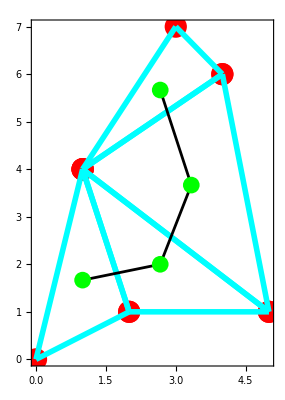

Graph of a set of simplices in 3D
:

-Graphics3D-

```mathematica
If [ testmode==1,
pointsize=0.04; 
pointcolor={1,0,0};
thickness=0.01;
linecolor={0,1,1};
pointsize1=0.03;
pointcolor1={0,1,0};
thickness1=0.005;
linecolor1={0,0,0};
points2d1={{0,0},{1,4},{2,1},{5,1},{4,6},{3,7}};simp2d1={{points2d1⟦1⟧,points2d1⟦2⟧,points2d1⟦3⟧},{points2d1⟦2⟧,points2d1⟦3⟧,points2d1⟦4⟧},{points2d1⟦2⟧,points2d1⟦4⟧,points2d1⟦5⟧},{points2d1⟦2⟧,points2d1⟦5⟧,points2d1⟦6⟧}};
simp2dcent=simplexcenters[simp2d1];

points3d1={{0,0,0},{1,4,0},{2,1,0},{1,2,3},{1,1,-1}};simp3d1={{points3d1⟦1⟧,points3d1⟦2⟧,points3d1⟦3⟧,points3d1⟦4⟧},
{points3d1⟦1⟧,points3d1⟦2⟧,points3d1⟦3⟧,points3d1⟦5⟧}};
simp3dcent=simplexcenters[simp3d1];

grsimp2d=simplexgraph[simp2d1,pointsize,thickness,pointcolor,linecolor];grsimpcent2d=pointsgraph[simp2dcent,pointsize1,thickness1,pointcolor1,Null];

grsimp3d=simplexgraph[simp3d1,pointsize,thickness,pointcolor,linecolor];
grsimpcent3d=pointsgraph[simp3dcent,pointsize1,thickness1,pointcolor1,Null];

];

If [testmode≠0,
Print["Graph of a set of simplices in 2D: \n"];
Show[grsimp2d,grsimpcent2d,PlotRange->All,Frame->True]
]
If [testmode≠0,
Print["\nGraph of a set of simplices in 3D\n:"];
Show[grsimp3d,grsimpcent3d
,PlotRange->All
,Axes->True
,FaceGrids->{{0,0,-1},{0,1,0},{-1,0,0}}
,AxesLabel->{"x","y","z  "}
,BoxRatios->{1,1,1}
,PlotRange->All
,ViewPoint->{3.892, -7.185, 3.771}]
]
```

# Additional utilities (unfinished or seldomly used)

## Data exchange through files

Format conversion for Input/output of data structures via strings

### Function outputform for outputting expressions to files or for sending them to C programs for parsing:

```mathematica
outputform[expr_]:=ToString[outputform1[expr]];

outputform1[expr_]:=Module[{i},
(* $A Igor mar06; *)

If[Depth[expr]==1,
Return[CForm[expr]]
];
Table[outputform1[ expr[[i]] ],{i,1,Length[expr]}]
];
```

### Function strmathform changes the numbers in e notation (e.g. 1.2e-10) to the Mathematica form (e.g. 1.2*10^-10) in a text string:

```mathematica
strmathform[strarg_]:=Module[{positions,str,i,pos,ch1,ch2},
(* $A Igor apr06; *)

str=strarg;
(* find potential exponents in e- notation for real numbers: *)
positions=StringPosition[str,{"e","E"}];
positions=Transpose[Reverse[positions]][[1]];
(*
Print["strmathform: str= <",str,">, exp. positions: ",positions];
*)
(* Eliminate those positions that do not belong to e-notations: *)
For[i=Length[positions],i≥1,i=i-1,
pos=positions[[i]];
If[pos>1,
ch1=StringTake[str,{pos-1,pos-1}],
ch1="!";  (* this will eliminate the current position *)
];
If[pos<StringLength[str],
ch2=StringTake[str,{pos+1,pos+1}],
ch2="!";   (* this will eliminate the current position *)
];

(*
Print["Deciding on elimination of position ",i," (",positions[[i]],"), ch1= ",ch1,", ch2= ",ch2];
*)

If[ (ch1!="." &&  ¬DigitQ[ch1] || ch2≠"+" && ch2!="-" && ¬DigitQ[ch2]),
positions=Delete[positions,i];
];
];

(*
Print["Exp. positions after elimination of false positions: ",positions];
*)

If[Length[positions]>0,

(*
str=StringReplacePart[str,"*10^",
Table[{positions[[i]],positions[[i]]},{i,1,Length[positions]}
];
];
*)

str=StringReplacePart[str,"*10^",
Table[{positions[[i]],positions[[i]]},{i,1,Length[positions]}
]
]

];
Return[str];
];
```

### Tests

#### strmathform

```mathematica
If[testmode≠0,
str="{1.2e-10, 15, 1e-20, \"teac\",1/3e25}"
,,]
```

```mathematica
If[testmode≠0,
mathstr=strmathform[str]
,,]
```

```mathematica
If[testmode≠0,
expr=ToExpression[mathstr]
,,]
```

```mathematica
If[testmode≠0,
FullForm[ expr[[4]] ]
,,]
```

#### outputform

```mathematica
If[testmode≠0,
expr={25,1/3,{1.2*10^-10, 15,1/10}, 1*10^-20, "teac"}
,,]
```

```mathematica
If[testmode≠0,
outputform[expr]
,,]
```

```mathematica
If[testmode≠0,
outputform[N[expr]]
,,]
```

#### Whole export/import cycle

```mathematica
If[testmode≠0,
(*
form="Lines";
form="Table";
form="List";
form="CSV";
*)
form="Text";

expr={{ {1.1,1.2},{2.1,2.2,2.3},3 } ,10^-16,5.5*10^22,"xy",bcd}
,,]
```

```mathematica
If[testmode≠0,
outstr= outputform[expr]
,,]
```

```mathematica
If[testmode≠0,
instr=ImportString[outstr,"Text"]
,,]
```

```mathematica
If[testmode≠0,
{Head[impstr],Length[impstr]}
,,]
```

```mathematica
If[testmode≠0,
expr1=ToExpression[strmathform[impstr]]
,,]
```

```mathematica
If[testmode≠0,
expr==expr1
,,]
```

```mathematica
If[testmode≠0,
CharacterRange["C","f"]
,,]
```

Output to files for reading in C

### Output & input of tables: - development stage

#### exporttable [ filename, tab ] importtable [ filename ] exporttable writes 1D or 2D table tab to file named filename (existing files are overwritten), numbers are separated by commas (lines of matrices by new lines), numbers are written in E notation. importtable imports a table in this format from the file names filename.

```mathematica
exporttable[filename_,tab_]:=Export[filename,N[tab],"CSV"];
importtable[filename_]:=Import[filename,"CSV"];
```

#### Test of exporting/importing a table:

2d table, 3x2

```mathematica
If[testmode≠0,
tab={{1.1,1.2},{2.1,2.2},{1/3,4.55*10^-26}}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

2d table, different lengths of lines

```mathematica
If[testmode≠0,
tab={{1.1,1.2,1.3,1.4},{2.1,2.2},{1/3,4.55*10^-26},{5.5}}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

1d table, different lengths of lines

```mathematica
If[testmode≠0,
tab={1,2,3,4,1/3,4.55*10^-26,5.5}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

```mathematica
If[testmode≠0,
Flatten[tab1]==tab
,,]
```

Deeper Tables

```mathematica
If[testmode≠0,
tab={{1.1,1.2},{2.1,2.2,{2.31,2.32},2.4},{3.1,3.2}}
,,]
```

```mathematica
If[testmode≠0,
exporttabletofile["test.out",tab];
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

```mathematica
If[testmode≠0,
tab1=importtable["test.out"]
,,]
```

```mathematica
If[testmode≠0,
tab1==tab
,,]
```

```mathematica
If[testmode≠0,
tab1[[2,3]]
,,]
```

```mathematica
If[testmode≠0,
FullForm[tab1[[2,3]]]
,,]
```

#### Experimentation for outputting tables (for development stage)

Write a table & check file contents -   Save

```mathematica
If[testmode≠0,
table={{1.1,1.2},{2.1,2.2},{3.1,3.1},{1/3,2.44*10^-20}}
,,]
```

```mathematica
If[testmode≠0,
Save["test.out",table];

Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

Write a table & check file contents -   Put

```mathematica
If[testmode≠0,
table={{1.1,1.2},{2.1,2.2},{3.1,3.1},{1/3,2.44*10^-20}}
,,]
```

```mathematica
If[testmode≠0,
table1={1,2}
,,]
```

```mathematica
If[testmode≠0,
Put[table1,table,"test.out"];
,,]


If[testmode≠0,
Import["test.out","Text"]  (* Show contents of the file *)
,,]
```

Write a table & check file contents -   Export

```mathematica
If[testmode≠0,
table={{1.1,1.2,111,222,{3,4}},{2.1,2.2},{3.1,3.1},{1/3,2.44*10^-20}}
,,]
```

```mathematica
If[testmode≠0,
table1={1,2}
,,]
```

```mathematica
If[testmode≠0,

tablenum=N[table]
,,]
```

```mathematica
If[testmode≠0,

form="Text";
form="List";
form="Lines";
form="Table";
form="CSV";

Export["test.out",table,form];

Import["test.out","Text"]  (* Show contents of the file *)

,,]
```

```mathematica
If[testmode≠0,

Export["test.out",tablenum,form];

Import["test.out","Text"]  (* Show contents of the file *)

,,]
```

```mathematica
If[testmode≠0,
tabin=Import["test.out","CSV"]
,,]
```

```mathematica
If[testmode≠0,
FullForm[tabin]
,,]
```

### Storing data for retrieval in Mathematica

#### This demonstrate how data from Mathematica can be stored in files such that it is easily read in another mathematica sessions.

```mathematica
(*
SetDirectory["C:/users/igor/doc/pr/enlub/work/SRT_identification_2006-01-20/StripReduction/"
];
*)
Directory[]
```

C:\Program Files\Wolfram Research\Mathematica\5.2

```mathematica
expr1={1.0,{2.1,2.3,{2.41}},3.1,1/3,"Text",6.02*10^-23,1/1000};
expr2={1,2,3};

expr1
```

{1.,{2.1,2.3,{2.41}},3.1,1/3,Text,6.02×10^-23,1/1000}

#### Writing expressions (& values) in standard form to a file: Warning: number notation is in Mathematica form. To convert to C form, import expression to Mathematica (assign to a variable), convert to suitable string form, and write back to a file. Note: Use of N[] for converting to approximate decimal numbers is not necessary since numbers will anyway be in Mathematica format

```mathematica
(* Write standard representation of expr1 to test.out, overwrite file *)
expr1>>"test.out";  
(* Append standard representation of expr1 to file test.out: *)
N[expr2]>>>"test.out" ;
!!"test.out"
```

{1., {2.1, 2.3, {2.41}}, 3.1, 1/3, "Text", 6.02*^-23, 1/1000}
{1., 2., 3.}

Use stdout for cell output:

```mathematica
(* Write standard representation of expr1 to test.out, overwrite file *)
expr1>>"stdout";  
(* Append standard representation of expr1 to file test.out: *)
expr2>>"stdout"
```

{1.,{2.1,2.3,{2.41}},3.1,1/3,Text,6.02×10^-23,1/1000}

{1,2,3}

#### Saving definitions of variable or function definitions in standard form in a file: Warning: Number notation is in Mathematica form. To convert to C form, import expression to Mathematica (assign to a variable), convert to suitable string form, and write back to a file. Notes Save appends to a file. For restoring definitions, simply read in the file by using << "filename"

```mathematica
"Definitions:">>test.out;  (* clears contents of the file *)
Save["test.out",{expr1,expr2}];
```

```mathematica
!!"test.out"
```

"Definitions:"
expr1 = {1., {2.1, 2.3, {2.41}}, 3.1, 1/3, "Text", 6.02*^-23, 1/1000}
 
expr2 = {1, 2, 3}

#### Restoring variable and function definitions saved to a file:

```mathematica
expr1={};
expr2={};
expr1
expr2
<< "test.out" ;
expr1
expr2
```

{}

{}

{1.,{2.1,2.3,{2.41}},3.1,1/3,Text,6.02×10^-23,1/1000}

{1,2,3}

#### Export from Mathematica:

```mathematica
exprvalue={{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,10^-16,5.5*10^22,"xy"}
```

{{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,5.5×10^22,xy}

```mathematica
N[exprvalue]
```

{{{1.1,1.2},{2.1,2.2,2.3},3.},1.×10^-16,5.5×10^22,xy}

```mathematica
CForm[exprvalue]  /.  List(x_)->{x}
```

List(List(List(1.1,1.2),List(2.1,2.2,2.3),3.),1.e-16,5.5e22,"xy")

#### Import to Mathematica:

```mathematica
exprstr="{{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,1e-16,\"xy\"}"
```

{{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,1e-16,"xy"}

```mathematica
exprstr="{1e-22}"
```

{1e-22}

ToExpression ne dela v redu:

```mathematica
expr=ToExpression[exprstr,InputForm]
```

{-22+e}

```mathematica
form="List";
expr=ImportString[exprstr,form,ConversionOptions->{"ListSeparators"->{","}}]
```

{{1e-22}}

```mathematica
expr[[0]]
```

List

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{1e-22},String}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{1e-22},String}

```mathematica
form="Table";
expr=ImportString[exprstr,form,ConversionOptions->{"ListSeparators"->{","}}]
```

{{{1e-22}}}

```mathematica
expr[[0]]
```

List

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{{1e-22}},List}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{{1e-22}},List}

```mathematica
form="Lines";
expr=ImportString[exprstr,form,ConversionOptions->{"ListSeparators"->{","}}]
```

{{1e-22}}

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{1e-22},String}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{1e-22},String}

```mathematica
exprstr="1.22e-25"
```

1.22e-25

```mathematica
form="CSV";
expr=ImportString[exprstr,form]
```

{{1.22×10^-25}}

```mathematica
{expr[[1]],expr[[1,0]]}
```

{{1.22×10^-25},List}

```mathematica
{expr[[-1]],expr[[-1,0]]}
```

{{1.22×10^-25},List}

```mathematica
{expr[[1,1]],expr[[1,1,0]]}
```

{1.22×10^-25,Real}

```mathematica
{expr[[-1,1]],expr[[-1,1,0]]}
```

{1.22×10^-25,Real}

```mathematica
FullForm[expr]
```

List[List[1.22×10^-25]]

#### Export/Import strings:

```mathematica
exprvalue={{ {1.1,1.2},{2.1,2.2,2.3},3.0 } ,10^-16,"xy"}
```

{{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}

```mathematica
form="Lines";
{exprstr=ExportString[exprvalue,form,ConversionOptions->{"ListSeparators"->{","}}],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.},1/10000000000000000,xy},  Check: ,{{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}=={{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}}

```mathematica
form="List";
{exprstr=ExportString[exprvalue,form,ConversionOptions->{"ListSeparators"->{","}}],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "1.2},". More…
                                                   ^

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "2.2, ". More…
                                                   ^

ToExpression::sntx: Syntax error in or before "2.3},". More…
                                                   ^

General::stop: 
   Further output of ToExpression::sntx
     will be suppressed during this calculation. More…

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{1.1,,1.2},,{2.1,,2.2,,2.3},,3.},1/10000000000000000,xy},  Check: ,False}

```mathematica
form="CSV";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}"
1/10000000000000000
xy,""{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}"
1/10000000000000000
xy",{{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}},{1/10000000000000000},{xy}},  Check: ,False}

```mathematica
form="Table";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "1.2},". More…
                                                   ^

Syntax::com: Warning: comma encountered with no adjacent expression; the expression will be treated as Null. "\n" More…

ToExpression::sntxi: 
   Incomplete expression; more input is needed. More…

ToExpression::sntx: Syntax error in or before "2.2, ". More…
                                                   ^

ToExpression::sntx: Syntax error in or before "2.3},". More…
                                                   ^

General::stop: 
   Further output of ToExpression::sntx
     will be suppressed during this calculation. More…

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{{1.1,,1.2},,{2.1,,2.2,,2.3},,3.}},{1/10000000000000000},{xy}},  Check: ,False}

```mathematica
form="Text";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

ToExpression::sntx: 
   Syntax error in or before 
    "{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                                           ^
     ". More…

{                                            1
{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                    10000000000000000,"                                            1
{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                    10000000000000000",                                            1
{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}, -----------------, xy}
                                    10000000000000000,  Check: ,$Failed=={{{1.1,1.2},{2.1,2.2,2.3},3.},1/10000000000000000,xy}}

```mathematica
form="TSV";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy,"{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}
1/10000000000000000
xy",{{{{1.1, 1.2}, {2.1, 2.2, 2.3}, 3.}},{1/10000000000000000},{xy}},  Check: ,False}

```mathematica
form="Words";
{exprstr=ExportString[exprvalue,form],
CForm[exprstr],
impstr=ImportString[exprstr,form],"  Check: ",ToExpression[impstr]==exprvalue}
```

{1.1
1.2
2.1
2.2
2.299999999999999
3.
1/10000000000000000
xy,"1.1
1.2
2.1
2.2
2.299999999999999
3.
1/10000000000000000
xy",{1.1,1.2,2.1,2.2,2.299999999999999,3.,1/10000000000000000,xy},  Check: ,False}

## Simulated & measurements smoothing

### Remark: In order to run this block, execute performmeasurementsmoothing=1;

```mathematica
(* $A Igor mar06; *)
```

Smooth down loaded measurements:

### Lists from which interpolation was formed:

```mathematica
If[performmeasurementsmoothing≠0,
listforceB01= Transpose[{timeB01,testB01//Transpose//Part[#,4]&}] ;
listtempB01p3= Transpose[{timeB01,testB01//Transpose//Part[#,2]&}] ;
listtempB01p1= Transpose[{timeB01,testB01//Transpose//Part[#,3]&}] ;
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
listforceC01= Transpose[{timeC01,testC01//Transpose//Part[#,4]&}] ;
listtempC01p2= Transpose[{timeC01,testC01//Transpose//Part[#,2]&}] ;
listtempC01p4= Transpose[{timeC01,testC01//Transpose//Part[#,3]&}] ;
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
{ {Length[listforceB01],Length[listtempB01p3],Length[listtempB01p1]},{Length[listforceC01], Length[listtempC01p2],Length[listtempC01p4] } }
,,]
```

### Calculate smoothed lists:

```mathematica
If[performmeasurementsmoothing≠0,
rportion=0.03;    (* relative effective radius *)
numsamp=400;    (* number of calculated (smoothed) samples *)
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
measlabel="forceB01";
measvar=ToExpression[StringJoin["list",measlabel]];

smoothedforceB01=smoothedvar=smoothmeasurements[measvar,rportion,numsamp,1];
Print[measlabel,": Num. meas. = ",Length[measvar],", num. meas. in effect. rad.: ",Length[measvar]*rportion];
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
measlabel="tempB01p3";
measvar=ToExpression[StringJoin["list",measlabel]];

smoothedtempB01p3=smoothedvar=smoothmeasurements[measvar,rportion,numsamp,1];
Print[measlabel,": Num. meas. = ",Length[measvar],", num. meas. in effect. rad.: ",Length[measvar]*rportion];

,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
measlabel="tempB01p1";
measvar=ToExpression[StringJoin["list",measlabel]];

smoothedtempB01p1=smoothedvar=smoothmeasurements[measvar,rportion,numsamp,1];
Print[measlabel,": Num. meas. = ",Length[measvar],", num. meas. in effect. rad.: ",Length[measvar]*rportion];

,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
measlabel="forceC01";
measvar=ToExpression[StringJoin["list",measlabel]];

smoothedforceC01=smoothedvar=smoothmeasurements[measvar,rportion,numsamp,1];
Print[measlabel,": Num. meas. = ",Length[measvar],", num. meas. in effect. rad.: ",Length[measvar]*rportion];

,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
measlabel="tempC01p2";
measvar=ToExpression[StringJoin["list",measlabel]];

smoothedtempC01p2=smoothedvar=smoothmeasurements[measvar,rportion,numsamp,1];
Print[measlabel,": Num. meas. = ",Length[measvar],", num. meas. in effect. rad.: ",Length[measvar]*rportion];

,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
measlabel="tempC01p4";
measvar=ToExpression[StringJoin["list",measlabel]];

smoothedtempC01p4=smoothedvar=smoothmeasurements[measvar,rportion,numsamp,1];
Print[measlabel,": Num. meas. = ",Length[measvar],", num. meas. in effect. rad.: ",Length[measvar]*rportion];

,,]
```

#### Quick test of data:

```mathematica
If[performmeasurementsmoothing≠0,
{ {Length[smoothedforceB01],Length[smoothedtempB01p3],Length[smoothedtempB01p1]},{Length[smoothedforceC01], Length[smoothedtempC01p2],Length[smoothedtempC01p4] } }
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
{ {smoothedforceB01[[15]],smoothedtempB01p3[[15]],smoothedtempB01p1[[15]]},{smoothedforceC01[[15]], smoothedtempC01p2[[15]],smoothedtempC01p4 [[15]]} } 
,,]
```

### Plots:

#### Plot of measurements (non-smoothed:)

```mathematica
If[performmeasurementsmoothing≠0,
pointsize=0;
colorhue=0.4;
colorhue1=0.6;
plotlistforceB01=ListPlot[listforceB01 ,PlotStyle->{PointSize[pointsize],Hue[colorhue]}, PlotRange->All,DisplayFunction->Identity];
plotlistlisttempB01p3=ListPlot[listtempB01p3, PlotStyle->{PointSize[pointsize],Hue[colorhue]}, PlotRange->All,DisplayFunction->Identity];
plotlistlisttempB01p1=ListPlot[listtempB01p1, PlotStyle->{PointSize[pointsize],Hue[colorhue]}, PlotRange->All,DisplayFunction->Identity];

plotlistlistforceC01=ListPlot[listforceC01, PlotStyle->{PointSize[pointsize],Hue[colorhue1]}, PlotRange->All,DisplayFunction->Identity];
plotlistlisttempC01p2=ListPlot[listtempC01p2, PlotStyle->{PointSize[pointsize],Hue[colorhue1]}, PlotRange->All,DisplayFunction->Identity];
plotlistlisttempC01p4=ListPlot[listtempC01p4, PlotStyle->{PointSize[pointsize],Hue[colorhue1]} ,PlotRange->All,DisplayFunction->Identity];
,,]
```

Show plots:

```mathematica
If[performmeasurementsmoothing≠0,Show[plotlistforceB01,DisplayFunction->$DisplayFunction];Show[plotlistlisttempB01p3,DisplayFunction->$DisplayFunction];Show[plotlistlisttempB01p1,DisplayFunction->$DisplayFunction];Show[plotlistlistforceC01,DisplayFunction->$DisplayFunction];Show[plotlistlisttempC01p2,DisplayFunction->$DisplayFunction];Show[plotlistlisttempC01p4,DisplayFunction->$DisplayFunction],Null,Null]
```

#### Plot of measurements (smoothed:)

```mathematica
If[performmeasurementsmoothing≠0,thick=0.002;plotsmoothedforceB01=ListPlot[smoothedforceB01,PlotRange->All,Joined->True,PlotStyle->{Hue[1],Thickness[thick]},DisplayFunction->Identity];plotsmoothedtempB01p3=ListPlot[smoothedtempB01p3,PlotRange->All,Joined->True,PlotStyle->{Hue[1],Thickness[thick]},DisplayFunction->Identity];plotsmoothedtempB01p1=ListPlot[smoothedtempB01p1,PlotRange->All,Joined->True,PlotStyle->{Hue[1],Thickness[thick]},DisplayFunction->Identity];plotsmoothedforceC01=ListPlot[smoothedforceC01,PlotRange->All,Joined->True,PlotStyle->{Hue[1],Thickness[thick]},DisplayFunction->Identity];plotsmoothedtempC01p2=ListPlot[smoothedtempC01p2,PlotRange->All,Joined->True,PlotStyle->{Hue[1],Thickness[thick]},DisplayFunction->Identity];plotsmoothedtempC01p4=ListPlot[smoothedtempC01p4,PlotRange->All,Joined->True,PlotStyle->{Hue[1],Thickness[thick]},DisplayFunction->Identity];,Null,Null]
```

Show plots:

```mathematica
If[performmeasurementsmoothing≠0,Show[plotsmoothedforceB01,DisplayFunction->$DisplayFunction];Show[plotsmoothedtempB01p3,DisplayFunction->$DisplayFunction];Show[plotsmoothedtempB01p1,DisplayFunction->$DisplayFunction];Show[plotsmoothedforceC01,DisplayFunction->$DisplayFunction];Show[plotsmoothedtempC01p2,DisplayFunction->$DisplayFunction];Show[plotsmoothedtempC01p4,DisplayFunction->$DisplayFunction],Null,Null]
```

#### Comparison of original and smoothed measurements:

```mathematica
If[performmeasurementsmoothing≠0,plotrangex=All;plotrangey=All;plotrangex={0.,1};plotrangey=Automatic;Print["forceB01:"] Show[plotsmoothedforceB01,plotlistforceB01,DisplayFunction->$DisplayFunction,PlotRange->{plotrangex,plotrangey}];Print["tempB01p3:"] Show[plotsmoothedtempB01p3,plotlistlisttempB01p3,DisplayFunction->$DisplayFunction,PlotRange->{plotrangex,plotrangey}];Print["tempB01p1:"] Show[plotsmoothedtempB01p1,plotlistlisttempB01p1,DisplayFunction->$DisplayFunction,PlotRange->{plotrangex,plotrangey}];Print["forceC01:"] Show[plotsmoothedforceC01,plotlistlistforceC01,DisplayFunction->$DisplayFunction,PlotRange->{plotrangex,plotrangey}];Print["tempC01p2:"] Show[plotsmoothedtempC01p2,plotlistlisttempC01p2,DisplayFunction->$DisplayFunction,PlotRange->{plotrangex,plotrangey}];Print["tempC01p4:"] Show[plotsmoothedtempC01p4,plotlistlisttempC01p4,DisplayFunction->$DisplayFunction,PlotRange->{plotrangex,plotrangey}],Null,Null]
```

Switch between original and smoothed measurements (replace measurement function)

```mathematica
If[performmeasurementsmoothing≠0,
usesmoothmeas=  1    ;      (* defines whether to use smoothed measurements *)

If[usesmoothmeas≠ 0|| usesmoothmeas,
forceB01=Interpolation[ smoothedforceB01 ];
tempB01p3=Interpolation[ smoothedtempB01p3 ];
tempB01p1=Interpolation[ smoothedtempB01p1 ];

forceC01=Interpolation[ smoothedforceC01 ];
tempC01p2=Interpolation[ smoothedtempC01p2 ];
tempC01p4=Interpolation[ smoothedtempC01p4 ];
colorhue=0.1;
,
forceB01=Interpolation[ listforceB01 ];
tempB01p3=Interpolation[ listtempB01p3 ];
tempB01p1=Interpolation[ listtempB01p1 ];

forceC01=Interpolation[ listforceC01 ];
tempC01p2=Interpolation[ listtempC01p2 ];
tempC01p4=Interpolation[ listtempC01p4 ];
colorhue=0.6;
,
forceB01=Interpolation[ listforceB01 ];
tempB01p3=Interpolation[ listtempB01p3 ];
tempB01p1=Interpolation[ listtempB01p1 ];

forceC01=Interpolation[ listforceC01 ];
tempC01p2=Interpolation[ listtempC01p2 ];
tempC01p4=Interpolation[ listtempC01p4 ];
colorhue=0.6;

];

,,]
```

#### Plots of actual measurements used:

```mathematica
If[performmeasurementsmoothing≠0,Plot[forceB01[x],{x,0,3},PlotStyle->Hue[colorhue],PlotRange->{0,2800}];Plot[tempB01p1[x],{x,0,3},PlotStyle->Hue[colorhue]];Plot[tempB01p3[x],{x,0,3},PlotStyle->Hue[colorhue]];Plot[forceC01[x],{x,0,3},PlotStyle->Hue[colorhue],PlotRange->{0,2800}];Plot[tempC01p2[x],{x,0,3},PlotStyle->Hue[colorhue]];Plot[tempC01p4[x],{x,0,3},PlotStyle->Hue[colorhue]],Null,Null]
```

#### Stored simulated forces and temperatures at optimal parameters

"{optsimforceB01,optsimtempB01p1,optsimtempC01p2,optsimtempB01p3,optsimtempC01p4}:"

```mathematica
If[performmeasurementsmoothing≠0,

{optsimforceB01,optsimtempB01p1,optsimtempC01p2,optsimtempB01p3,optsimtempC01p4}=   {{{0.000125,0.},{0.0003734567901234568,223.86655048852924},{0.0006740588324950465,334.30656367887826},{0.0011416620095175193,452.7690125611259},{0.0018690447293302549,534.8405125456261},{0.003000528960150066,704.0930450133347},{0.0038805722507876967,782.3849062568096},{0.005249528480668456,978.6902426488251},{0.006314272215020157,1072.0320101739708},{0.007799655449362654,1298.8817053734929},{0.00895495352051793,1479.749217680944},{0.010752083853426138,1685.2910381400295},{0.0125,1877.7746839327838},{0.013125000000000001,1837.0191828235456},{0.019375000000000007,1958.7550796270475},{0.02562500000000001,2116.373248749988},{0.03187500000000002,2211.797026961936},{0.03812500000000002,2176.933807612795},{0.04437500000000003,2297.8541742170673},{0.05062500000000003,2361.447390614208},{0.056875000000000044,2369.221862207327},{0.06312500000000004,2369.29987347552},{0.06937500000000006,2415.9241707080937},{0.07562500000000005,2400.8787223607715},{0.08187500000000006,2394.6180606252437},{0.08812500000000006,2380.388877723002},{0.09437500000000006,2367.8406756962263},{0.09750000000000006,2383.403097210239},{0.10185956790123463,2365.359178797978},{0.10810956790123463,2365.27413114466},{0.11435956790123464,2429.7578208217483},{0.12060956790123463,2344.8247922580467},{0.12685956790123462,2348.670289802645},{0.13310956790123465,2428.3610418197304},{0.1375,2342.146712251675},{0.14374999999999988,2340.159239896596},{0.18895080780368767,2436.6768008017734},{0.2514508078036877,2331.9777011875876},{0.3139508078036878,2339.615016838206},{0.3764508078036879,2424.081252960062},{0.43895080780368795,2339.070698890316},{0.501450807803688,2335.693814658842},{0.563950807803688,2383.325783250083},{0.5952008078036879,2333.9715005508115},{0.6264508078036878,2409.217586116626},{0.675061918914799,2340.215271375257},{0.7338753619875013,2431.2601675480805},{0.796375361987501,2324.1833665433796},{0.8588753619875007,2336.39338725193},{0.9213753619875006,2417.782431667972},{0.9838753619875004,2364.477792469483},{1.0463753619875,2332.9010826736944},{1.1088753619874998,2357.862223952319},{1.1401253619874998,2331.4684695981036},{1.1707503619875002,2415.9363995801973},{1.2183892508763892,2339.1373505750057},{1.276026425087637,2431.56814079242},{1.338526425087637,2323.6597745255294},{1.4010264250876368,2336.2206050887075},{1.4635264250876365,2419.6960861953094},{1.526026425087636,2368.342850112084},{1.588526425087636,2332.916634612608},{1.6510264250876359,2365.4110240230875},{1.6822764250876354,2331.561505372121},{1.7135264250876354,2418.878013142558},{1.7621375361987466,2339.033627666827},{1.8246375361987461,2421.0723773554428},{1.8871375361987461,2370.034995775607},{1.949637536198746,2334.2312806620776},{2.0121375361987455,2369.093104108862},{2.0433875361987455,2332.7701629046956},{2.0746375361987455,2419.739361008403},{2.123248647309856,2340.079052799858},{2.185748647309856,2423.9994714712916},{2.2482486473098557,2370.5837400941273},{2.3107486473098553,2335.238969558123},{2.3732486473098553,2379.0363563500637},{2.4044986473098557,2334.021755480535},{2.435123647309856,2419.169476998704},{2.4827625361987447,2341.8486220880604},{2.5452625361987447,2431.14021344731},{2.607762536198744,2359.0838770400987},{2.6702625361987438,2337.3153387937405},{2.7327625361987438,2402.0066744154},{2.7640125361987433,2336.2872073595886},{2.794637536198744,2415.6659124992752},{2.8422764250876327,2343.792602328155},{2.9047764250876327,2434.9176443360134},{2.9672764250876327,2344.9016116111334},{3.0297764250876322,2339.516215703075},{3.0922764250876322,2418.0256641823717},{3.154776425087632,2393.54868068883},{3.2172764250876313,2335.244968317991},{3.2797764250876313,2350.7303293376012},{3.3110264250876313,2334.074825815405},{3.3422764250876322,2429.878342590188},{3.390887536198743,2342.2510907247124},{3.3959999999999995,2340.6734825353788}},{{0.000125,20.},{0.0003734567901234568,20.033667357139162},{0.0006740588324950465,20.053814376146295},{0.0011416620095175193,20.074392382539862},{0.0018690447293302549,20.090375672803017},{0.003000528960150066,20.106973966775364},{0.0038805722507876967,20.124789045967844},{0.005249528480668456,20.147655366199693},{0.006314272215020157,20.167206183689796},{0.007799655449362654,20.197258642972198},{0.00895495352051793,20.219158453274954},{0.010752083853426138,20.24987408717444},{0.0125,20.28050043147134},{0.013125000000000001,20.30844830118734},{0.019375000000000007,20.425688787169033},{0.02562500000000001,20.591129083396666},{0.03187500000000002,20.7513971952012},{0.03812500000000002,20.970093634210937},{0.04437500000000003,21.20721624844463},{0.05062500000000003,21.434910719709166},{0.056875000000000044,21.678366024611094},{0.06312500000000004,21.92678826163334},{0.06937500000000006,22.168652393005498},{0.07562500000000005,22.394563559301215},{0.08187500000000006,22.659793747400148},{0.08812500000000006,22.87954764396039},{0.09437500000000006,23.1177522824178},{0.09750000000000006,23.247774056814393},{0.10185956790123463,23.422434964744586},{0.10810956790123463,23.663603524906442},{0.11435956790123464,23.8898614061283},{0.12060956790123463,24.155581842131966},{0.12685956790123462,24.40323736917489},{0.13310956790123465,24.629826081715144},{0.1375,24.823571533970984},{0.14374999999999988,24.958012038336904},{0.18895080780368767,25.868334374565578},{0.2514508078036877,27.17402764739976},{0.3139508078036878,28.369367413364678},{0.3764508078036879,29.327596155114158},{0.43895080780368795,30.282501616921323},{0.501450807803688,31.213659981148055},{0.563950807803688,31.966297265341332},{0.5952008078036879,32.43992342761614},{0.6264508078036878,32.78190918184566},{0.675061918914799,33.474085415960104},{0.7338753619875013,34.06040588300158},{0.796375361987501,34.7934026840863},{0.8588753619875007,35.47948710699209},{0.9213753619875006,35.982670040004635},{0.9838753619875004,36.52949781670573},{1.0463753619875,37.13158493954476},{1.1088753619874998,37.58540579345773},{1.1401253619874998,37.88359566658082},{1.1707503619875002,38.084462139695404},{1.2183892508763892,38.551004850274126},{1.276026425087637,38.90100132413016},{1.338526425087637,39.41293717536888},{1.4010264250876368,39.90511652014777},{1.4635264250876365,40.23065323664411},{1.526026425087636,40.61451731745249},{1.588526425087636,41.067893389244716},{1.6510264250876359,41.38570216849294},{1.6822764250876354,41.61903220255547},{1.7135264250876354,41.76717133951459},{1.7621375361987466,42.1424540153322},{1.8246375361987461,42.41523659180329},{1.8871375361987461,42.740489070335514},{1.949637536198746,43.139440705044976},{2.0121375361987455,43.405591947884744},{2.0433875361987455,43.61418917708646},{2.0746375361987455,43.73798590462807},{2.123248647309856,44.075597263346545},{2.185748647309856,44.302470616687685},{2.2482486473098557,44.58083552544612},{2.3107486473098553,44.93617128830405},{2.3732486473098553,45.159507228066474},{2.4044986473098557,45.351055759147584},{2.435123647309856,45.45254691215845},{2.4827625361987447,45.75627397257952},{2.5452625361987447,45.94546851387426},{2.607762536198744,46.18260979058536},{2.6702625361987438,46.483520123213154},{2.7327625361987438,46.6614763912569},{2.7640125361987433,46.85096792411143},{2.794637536198744,46.9337833040402},{2.8422764250876327,47.21781916353022},{2.9047764250876327,47.38152786791263},{2.9672764250876327,47.58485978306753},{3.0297764250876322,47.832927384187016},{3.0922764250876322,47.975000641265154},{3.154776425087632,48.193826340179626},{3.2172764250876313,48.51167685967341},{3.2797764250876313,48.7069402096569},{3.3110264250876313,48.845538148837036},{3.3422764250876322,48.93702877272304},{3.390887536198743,49.18341394707644},{3.3959999999999995,49.19652140085815}},{{0.000125,20.},{0.0003734567901234568,20.04866584288095},{0.0006740588324950465,20.079801849070705},{0.0011416620095175193,20.115703886840446},{0.0018690447293302549,20.15019205526163},{0.003000528960150066,20.196895679327866},{0.0038805722507876967,20.234886611376012},{0.005249528480668456,20.293915015024133},{0.006314272215020157,20.339395734799968},{0.007799655449362654,20.412412229317795},{0.00895495352051793,20.470129465144478},{0.010752083853426138,20.559816411846118},{0.0125,20.656241202371938},{0.013125000000000001,20.705638576275188},{0.019375000000000007,21.210701027866904},{0.02562500000000001,21.931580740422543},{0.03187500000000002,22.72503645664687},{0.03812500000000002,23.62460608750181},{0.04437500000000003,24.55871218567874},{0.05062500000000003,25.4509623203004},{0.056875000000000044,26.310013423094826},{0.06312500000000004,27.147862022625187},{0.06937500000000006,27.9470549623857},{0.07562500000000005,28.656083030423027},{0.08187500000000006,29.412493922409247},{0.08812500000000006,30.06597819251096},{0.09437500000000006,30.702071118321737},{0.09750000000000006,31.040074006458454},{0.10185956790123463,31.47475608376353},{0.10810956790123463,32.071429084517106},{0.11435956790123464,32.62209816287076},{0.12060956790123463,33.19445787172515},{0.12685956790123462,33.73443917220468},{0.13310956790123465,34.223803773975995},{0.1375,34.59614459466305},{0.14374999999999988,34.86322913365063},{0.18895080780368767,36.57545448324673},{0.2514508078036877,38.59859916978586},{0.3139508078036878,40.315383825212024},{0.3764508078036879,41.66402263026508},{0.43895080780368795,42.83864781084206},{0.501450807803688,43.97046453127601},{0.563950807803688,44.89616851001324},{0.5952008078036879,45.43975406397521},{0.6264508078036878,45.88401010348294},{0.675061918914799,46.63033401461023},{0.7338753619875013,47.311098739576096},{0.796375361987501,48.054822136829394},{0.8588753619875007,48.7488736613275},{0.9213753619875006,49.26779527393702},{0.9838753619875004,49.82684526273128},{1.0463753619875,50.41177116550462},{1.1088753619874998,50.856184221686895},{1.1401253619874998,51.12975836391365},{1.1707503619875002,51.36621486081201},{1.2183892508763892,51.80202895048099},{1.276026425087637,52.172892778809235},{1.338526425087637,52.63685337026247},{1.4010264250876368,53.09098267328745},{1.4635264250876365,53.395600774700284},{1.526026425087636,53.76889251584523},{1.588526425087636,54.17654649118719},{1.6510264250876359,54.46667962132776},{1.6822764250876354,54.667844891549876},{1.7135264250876354,54.846344756062116},{1.7621375361987466,55.1751241025088},{1.8246375361987461,55.43924581803567},{1.8871375361987461,55.74677054728473},{1.949637536198746,56.09131270763142},{2.0121375361987455,56.32370078984268},{2.0433875361987455,56.49794681341729},{2.0746375361987455,56.65096830420308},{2.123248647309856,56.93905306659827},{2.185748647309856,57.15467387106036},{2.2482486473098557,57.411732311929974},{2.3107486473098553,57.71260944935959},{2.3732486473098553,57.90336941417141},{2.4044986473098557,58.062866687341874},{2.435123647309856,58.1959126915651},{2.4827625361987447,58.450009492345956},{2.5452625361987447,58.63379167303984},{2.607762536198744,58.81478470734978},{2.6702625361987438,59.06499674535089},{2.7327625361987438,59.2274847550726},{2.7640125361987433,59.39919786309357},{2.794637536198744,59.51949482890651},{2.8422764250876327,59.754277771474875},{2.9047764250876327,59.91917360403613},{2.9672764250876327,60.020239747537914},{3.0297764250876322,60.22032447560137},{3.0922764250876322,60.365346745487976},{3.154776425087632,60.6262027665992},{3.2172764250876313,60.88993123455612},{3.2797764250876313,61.040440501867444},{3.3110264250876313,61.126130879500614},{3.3422764250876322,61.24197980297045},{3.390887536198743,61.43110619091301},{3.3959999999999995,61.43548674042226}},{{0.000125,20.},{0.0003734567901234568,20.01569452030598},{0.0006740588324950465,20.024864201026727},{0.0011416620095175193,20.035144894108424},{0.0018690447293302549,20.044540125822046},{0.003000528960150066,20.058927705169413},{0.0038805722507876967,20.0699326253359},{0.005249528480668456,20.089581767352264},{0.006314272215020157,20.104321929845117},{0.007799655449362654,20.13003549980955},{0.00895495352051793,20.151520483162663},{0.010752083853426138,20.18493767751019},{0.0125,20.220424684076978},{0.013125000000000001,20.22853556555451},{0.019375000000000007,20.361833159463973},{0.02562500000000001,20.516662714872734},{0.03187500000000002,20.66824604367751},{0.03812500000000002,20.838188745794582},{0.04437500000000003,21.05984768981546},{0.05062500000000003,21.298837285864735},{0.056875000000000044,21.541320934708505},{0.06312500000000004,21.77650477074099},{0.06937500000000006,22.09242854074498},{0.07562500000000005,22.364553551943004},{0.08187500000000006,22.721117587620242},{0.08812500000000006,23.033758610308663},{0.09437500000000006,23.425410982561715},{0.09750000000000006,23.58846312212759},{0.10185956790123463,23.895382789287797},{0.10810956790123463,24.285839794071148},{0.11435956790123464,24.710197161695504},{0.12060956790123463,25.148091770419075},{0.12685956790123462,25.55653022407941},{0.13310956790123465,25.986251297741283},{0.1375,26.29057773925137},{0.14374999999999988,26.550767670047154},{0.18895080780368767,28.158732942248392},{0.2514508078036877,30.344960934455457},{0.3139508078036878,32.08257905836128},{0.3764508078036879,33.662838482037806},{0.43895080780368795,35.249521831382516},{0.501450807803688,36.529299709529056},{0.563950807803688,37.54429212660254},{0.5952008078036879,38.21138955345734},{0.6264508078036878,38.76505568933197},{0.675061918914799,39.459341282953645},{0.7338753619875013,40.37681965103373},{0.796375361987501,41.37822000712351},{0.8588753619875007,42.133090361252385},{0.9213753619875006,42.85406893544557},{0.9838753619875004,43.73631795561367},{1.0463753619875,44.41004069163495},{1.1088753619874998,44.83134390048948},{1.1401253619874998,45.26835351733985},{1.1707503619875002,45.57114956817877},{1.2183892508763892,45.944773206996615},{1.276026425087637,46.508236817964},{1.338526425087637,47.18455789250446},{1.4010264250876368,47.65698775113317},{1.4635264250876365,48.132654314308},{1.526026425087636,48.78256190992836},{1.588526425087636,49.243414012219716},{1.6510264250876359,49.4964377209521},{1.6822764250876354,49.83605475071628},{1.7135264250876354,50.06164822702857},{1.7621375361987466,50.32922852924705},{1.8246375361987461,50.73446611109832},{1.8871375361987461,51.32088039366889},{1.949637536198746,51.71709663229342},{2.0121375361987455,51.91218793711956},{2.0433875361987455,52.21833311296538},{2.0746375361987455,52.41521795532534},{2.123248647309856,52.633093559911174},{2.185748647309856,52.98571938451285},{2.2482486473098557,53.51398167932687},{2.3107486473098553,53.85022901458357},{2.3732486473098553,54.015102490579416},{2.4044986473098557,54.28782214483974},{2.435123647309856,54.46420909355689},{2.4827625361987447,54.62029358382676},{2.5452625361987447,54.95903760274565},{2.607762536198744,55.42501698871962},{2.6702625361987438,55.70193937335717},{2.7327625361987438,55.888453990559825},{2.7640125361987433,56.117641684721356},{2.794637536198744,56.29036889487558},{2.8422764250876327,56.39220598544809},{2.9047764250876327,56.718726260887806},{2.9672764250876327,57.124924626425155},{3.0297764250876322,57.346270652950636},{3.0922764250876322,57.54595262041679},{3.154776425087632,57.96380163013469},{3.2172764250876313,58.19921968658467},{3.2797764250876313,58.18514440112575},{3.3110264250876313,58.42973500011151},{3.3422764250876322,58.539577583636955},{3.390887536198743,58.66912783942889},{3.3959999999999995,58.70533601536963}},{{0.000125,20.},{0.0003734567901234568,20.011659605895844},{0.0006740588324950465,20.01830443104635},{0.0011416620095175193,20.02558814200795},{0.0018690447293302549,20.03195962729955},{0.003000528960150066,20.041735640358656},{0.0038805722507876967,20.04915374766754},{0.005249528480668456,20.062378550029145},{0.006314272215020157,20.072106705037736},{0.007799655449362654,20.089215541130027},{0.00895495352051793,20.103290898187232},{0.010752083853426138,20.12455535642351},{0.0125,20.146742191609636},{0.013125000000000001,20.151297199477067},{0.019375000000000007,20.233014484562354},{0.02562500000000001,20.32564304866097},{0.03187500000000002,20.40840323222295},{0.03812500000000002,20.49035354975959},{0.04437500000000003,20.591840622126018},{0.05062500000000003,20.684170829761396},{0.056875000000000044,20.759042464651213},{0.06312500000000004,20.809587112017418},{0.06937500000000006,20.881007212243897},{0.07562500000000005,20.90907637901685},{0.08187500000000006,20.961931892890835},{0.08812500000000006,20.978521217652887},{0.09437500000000006,21.028468118059116},{0.09750000000000006,21.036075151458295},{0.10185956790123463,21.084417480913324},{0.10810956790123463,21.13133267518564},{0.11435956790123464,21.202667893481895},{0.12060956790123463,21.28110022102492},{0.12685956790123462,21.355339014848948},{0.13310956790123465,21.451481657321295},{0.1375,21.5192659055792},{0.14374999999999988,21.58300346481571},{0.18895080780368767,22.090009363865725},{0.2514508078036877,22.937503728795136},{0.3139508078036878,23.782542996966495},{0.3764508078036879,24.65290784887663},{0.43895080780368795,25.54661334127524},{0.501450807803688,26.38679792367533},{0.563950807803688,27.143836254635996},{0.5952008078036879,27.58442965671164},{0.6264508078036878,28.001073316115434},{0.675061918914799,28.54484212872638},{0.7338753619875013,29.258071847369514},{0.796375361987501,29.98231696240284},{0.8588753619875007,30.64467220113717},{0.9213753619875006,31.29059082736505},{0.9838753619875004,31.96444506245237},{1.0463753619875,32.56609138016146},{1.1088753619874998,33.06998415013108},{1.1401253619874998,33.417582282192555},{1.1707503619875002,33.716499119955294},{1.2183892508763892,34.087800232745415},{1.276026425087637,34.60320419895825},{1.338526425087637,35.13976482175819},{1.4010264250876368,35.62942688797601},{1.4635264250876365,36.119336276684095},{1.526026425087636,36.64251258396612},{1.588526425087636,37.10045608765378},{1.6510264250876359,37.482462095117654},{1.6822764250876354,37.7599545555199},{1.7135264250876354,38.00478162701815},{1.7621375361987466,38.29733181081015},{1.8246375361987461,38.7182926272157},{1.8871375361987461,39.17924878922551},{1.949637536198746,39.57734702314385},{2.0121375361987455,39.90588711823212},{2.0433875361987455,40.15431836326954},{2.0746375361987455,40.37367195948325},{2.123248647309856,40.62525301295392},{2.185748647309856,41.00013539942601},{2.2482486473098557,41.412355357951824},{2.3107486473098553,41.76214470389169},{2.3732486473098553,42.05555788455871},{2.4044986473098557,42.274406775491826},{2.435123647309856,42.471623983649906},{2.4827625361987447,42.678447332032775},{2.5452625361987447,43.02955595333338},{2.607762536198744,43.39235858563204},{2.6702625361987438,43.70207763967295},{2.7327625361987438,43.98706102159621},{2.7640125361987433,44.16774205029907},{2.794637536198744,44.352452488781154},{2.8422764250876327,44.52575868672075},{2.9047764250876327,44.859343940347614},{2.9672764250876327,45.17944960088109},{3.0297764250876322,45.45466344455613},{3.0922764250876322,45.73081802597717},{3.154776425087632,46.06791369918107},{3.2172764250876313,46.329465911291756},{3.2797764250876313,46.50671687815033},{3.3110264250876313,46.70740627695355},{3.3422764250876322,46.86148249322932},{3.390887536198743,47.02080186413044},{3.3959999999999995,47.049689412639275}}}  ;

,,]
```

### Definition of integrals for non-smoothed functions: (this is to overcome problems with NIntegrate; This cell can be run after the following cells where simulated measuerments are defined.)

#### Test integration with different number of points (to see how many ponts should be used):

```mathematica
If[performmeasurementsmoothing≠0,
numintpoints=100;
{objforceB01, objtempB01p1, objtempC01p2, objtempB01p3, objtempC01p4}
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
numintpoints=400;
{objforceB01, objtempB01p1, objtempC01p2, objtempB01p3, objtempC01p4}
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
numintpoints=1000;
{objforceB01, objtempB01p1, objtempC01p2, objtempB01p3, objtempC01p4}
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
numintpoints=2000;
{objforceB01, objtempB01p1, objtempC01p2, objtempB01p3, objtempC01p4}
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
numintpoints=4000;
{objforceB01, objtempB01p1, objtempC01p2, objtempB01p3, objtempC01p4}
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
numintpoints=8000;
{objforceB01, objtempB01p1, objtempC01p2, objtempB01p3, objtempC01p4}
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
numintpoints=20000;
{objforceB01, objtempB01p1, objtempC01p2, objtempB01p3, objtempC01p4}
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
numintpoints=4000;  (* this seems enough points for integration of non-smooth response *)

(* definition of numerical integral to avoid problems with NIntegrate: *)
numint[f_,xmin_,xmax_,npoints_]:=N[Sum[
f[xmin+(xmax-xmin)*(i-1)/(npoints-1)]
,{i,1,npoints}
] *(xmax-xmin)/(npoints-1)];

objforceB01:=numint[funcobjforceB01,forcefrom,forceto,numintpoints];
objtempB01p1:=numint[funcobjtempB01p1,tempfrom,tempto,numintpoints];
objtempC01p2:=numint[funcobjtempC01p2,tempfrom,tempto,numintpoints];
objtempB01p3:=numint[funcobjtempB01p3,tempfrom,tempto,numintpoints];
objtempC01p4:=numint[funcobjtempC01p4,tempfrom,tempto,numintpoints];

,,]
```

#### Test of numint:

```mathematica
If[performmeasurementsmoothing≠0,
{numint[Sin,0,Pi,400],NIntegrate[Sin[x],{x,0,Pi}]}
,,]
```

#### Stored objective terms at optimal parameters without smoothing:

```mathematica
If[performmeasurementsmoothing≠0,
"{objforceB01, objtempB01p1, objtempC01p2, objtempB01p3, objtempC01p4}: "
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
{10629.604324002696,70.55549578623118,17.827630144000032,6.771548409502178,67.90928117084766}
,,]
```

#### Stored objective terms at optimal parameters with smoothing:

```mathematica
If[performmeasurementsmoothing≠0,
"{objforceB01, objtempB01p1, objtempC01p2, objtempB01p3, objtempC01p4}: "
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
{10243.783521967516,70.35186956608747,17.32753489513989,6.370657315171072,67.71743794530236}
,,]
```

### Calculation of smoothed simulated measurements:

```mathematica
(* For remote calculation of smoothed data (via parallel request server), define:
calculatesmoothedobjterms:=calculatesmoothedobjterms0[linkname];
where linkname is the name of the link through which the server is accessed. *)

(* Local calculation of smoothed objective terms: *)
calculatesmoothedobjterms:=calculatesmoothedobjterms0[""];


(* calculation of smoothed simulated measurements that can be performed both locally (linkname=="") and globally: *)
calculatesmoothedobjterms0[linkname_]:=Module [{remote=0},
If[StringQ[linkname] ,
If[StringLength[linkname]>0,
remote=1;
];
];

If[debugmode≠0,
Print["calculatesmoothedobjterms: beginning"];
];

(* Extraction of simulated forces and temperatures after simulation: *)
simforceB01=Map[ {realTime[#⟦1⟧],StripWidth#⟦2⟧}&,forceHistory ];
{simtempB01p1,simtempC01p2,simtempB01p3,simtempC01p4}=Table[    Map[ {realTime[#⟦1⟧],20+#⟦2,iNode⟧}&,temperatureHistory],
{iNode,1,4} ];


If[debugmode≠0,
Print["calculatesmoothedobjterms: after extraction of simuated forces & temperatures"];
];


(* Calculation of smoothed simulated measurements: *)
rportion=0.06;    (* relative effective radius *)
numsamp=400;    (* number of calculated (smoothed) samples *)

If[debugmode≠0,
Print["calculatesmoothedobjterms: just before calculation of smooth fores - smoothedsimforceB01"];
];

If[remote≠0,
smoothedsimforceB01=smoothmeasurements[simforceB01,rportion,numsamp,1,linkname ];  
,    (* local calculation follows *)
smoothedsimforceB01=smoothmeasurements[simforceB01,rportion,numsamp,1];
];

If[debugmode≠0,
Print["calculatesmoothedobjterms: just before calculation of smooth temperatures - smoothedsimforceB01"];
];


rportion=0.06;    (* relative effective radius *)
numsamp=400;    (* number of calculated (smoothed) samples *)

If[remote≠0,
smoothedsimtempB01p1=smoothmeasurements[simtempB01p1,rportion,numsamp,1,linkname ];
smoothedsimtempC01p2=smoothmeasurements[simtempC01p2,rportion,numsamp,1,linkname ];
smoothedsimtempB01p3=smoothmeasurements[simtempB01p3,rportion,numsamp,1,linkname ];
smoothedsimtempC01p4=smoothmeasurements[simtempC01p4,rportion,numsamp,1,linkname ];  
,    (* local calculation follows *)
smoothedsimtempB01p1=smoothmeasurements[simtempB01p1,rportion,numsamp,1];
smoothedsimtempC01p2=smoothmeasurements[simtempC01p2,rportion,numsamp,1];
smoothedsimtempB01p3=smoothmeasurements[simtempB01p3,rportion,numsamp,1];
smoothedsimtempC01p4=smoothmeasurements[simtempC01p4,rportion,numsamp,1];  
];

(* Create interpolation functions from simulated measurements: *)
funcsimforceB01=Interpolation[smoothedsimforceB01];
funcsimtempB01p1=Interpolation[smoothedsimtempB01p1];
funcsimtempC01p2=Interpolation[smoothedsimtempC01p2];
funcsimtempB01p3=Interpolation[smoothedsimtempB01p3];
funcsimtempC01p4=Interpolation[smoothedsimtempC01p4];

(* Definition of objective function terms (integrals of squre function differences): *)
(* Integration limits: *)
forcefrom=0.5;
forceto=3.3;
tempfrom=0.01;
tempto=3.3;

(* square difference functions: *)
funcobjforceB01[x_]:=(forceB01[x]-funcsimforceB01[x])^2;
funcobjtempB01p1[x_]:=(tempB01p1[x]-funcsimtempB01p1[x])^2;
funcobjtempC01p2[x_]:=(tempC01p2[x]-funcsimtempC01p2[x])^2;funcobjtempB01p3[x_]:=(tempB01p3[x]-funcsimtempB01p3[x])^2;
funcobjtempC01p4[x_]:=(tempC01p4[x]-funcsimtempC01p4[x])^2;

Return[{objforceB01,objtempB01p1,objtempC01p2,objtempB01p3,objtempC01p4}];
];

(* Integrals (Inegral definitions can be chaged for those suitable for unsmoothed data - see above!): *)
objforceB01:=NIntegrate[funcobjforceB01[x],{x,forcefrom,forceto}];
objtempB01p1:=NIntegrate[funcobjtempB01p1[x],{x,tempfrom,tempto}];
objtempC01p2:=NIntegrate[funcobjtempC01p2[x],{x,tempfrom,tempto}];
objtempB01p3:=NIntegrate[funcobjtempB01p3[x],{x,tempfrom,tempto}];
objtempC01p4:=NIntegrate[funcobjtempC01p4[x],{x,tempfrom,tempto}];
```

```mathematica
usesmoothmeas
```

usesmoothmeas

```mathematica
If[performmeasurementsmoothing≠0,
If[0≠0,
calculatesmoothedobjterms
]
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,
{objforceB01,objtempB01p1,objtempC01p2,objtempB01p3,objtempC01p4}
,,]
```

#### Test plot: interpolation function of smoothed simulated force (small amplitude low frequency oscilations)

```mathematica
If[performmeasurementsmoothing≠0,
func=Interpolation[smoothedsimforceB01,InterpolationOrder -> 1];
,,]
```

```mathematica
If[performmeasurementsmoothing≠0,Print["Low Frequency, low amplitude oscillatinos seen with given plot range:"];Plot[func[x],{x,0.5,3}];Plot[func[x],{x,0,3},PlotRange->All],Null,Null]
```

#### Plots of functions to be integrated:

```mathematica
If[performmeasurementsmoothing≠0,Print["Square difference function: forceB01:"];plotobjforceB01=Plot[funcobjforceB01[x],{x,forcefrom,forceto},PlotRange->All,PlotStyle->{Hue[0.4]}];Print["Square difference function: tempB01p1:"];plotobjtempB01p1=Plot[funcobjtempB01p1[x],{x,forcefrom,forceto},PlotRange->All,PlotStyle->{Hue[0.4]}];Print["Square difference function: tempC01p2:"];plotobjtempC01p2=Plot[funcobjtempC01p2[x],{x,forcefrom,forceto},PlotRange->All,PlotStyle->{Hue[0.4]}];Print["Square difference function: tempB01p3:"];plotobjtempB01p3=Plot[funcobjtempB01p3[x],{x,forcefrom,forceto},PlotRange->All,PlotStyle->{Hue[0.4]}];Print["Square difference function: tempC01p4:"];plotobjtempC01p4=Plot[funcobjtempC01p4[x],{x,forcefrom,forceto},PlotRange->All,PlotStyle->{Hue[0.4]}],Null,Null]
```

```mathematica
If[performmeasurementsmoothing≠0,

Print["Comparison of measured data and smoothed simuated measuremets, term "];
{Plot[forceB01[x],{x,0,maxTimeB01C01},PlotRange->{{forcefrom,forceto},All},PlotStyle->Hue[0.1],DisplayFunction->Identity],
Plot[funcsimforceB01[x],{x,0,maxTimeB01C01},PlotRange->{{forcefrom,forceto},All},PlotStyle->Hue[0.4],DisplayFunction->Identity]
}//Show[#,DisplayFunction->$DisplayFunction]&;

Print["Comparison of measured data and smoothed simuated measuremets, term tempB01p1"];
{Plot[tempB01p1[x],{x,0,maxTimeB01C01},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.1],DisplayFunction->Identity],
Plot[funcsimtempB01p1[x],{x,0,maxTimeB01C01},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.4],DisplayFunction->Identity]
}//Show[#,DisplayFunction->$DisplayFunction]&;

Print["Comparison of measured data and smoothed simuated measuremets, term tempC01p2"];
{Plot[tempC01p2[x],{x,0,maxTimeB01C01},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.1],DisplayFunction->Identity],
Plot[funcsimtempC01p2[x],{x,0,maxTimeB01C01},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.4],DisplayFunction->Identity]
}//Show[#,DisplayFunction->$DisplayFunction]&;

Print["Comparison of measured data and smoothed simuated measuremets, term tempB01p3"];
{Plot[tempB01p3[x],{x,0,maxTimeB01C01},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.1],DisplayFunction->Identity],
Plot[funcsimtempB01p3[x],{x,0,maxTimeB01C01},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.4],DisplayFunction->Identity]
}//Show[#,DisplayFunction->$DisplayFunction]&;

Print["Comparison of measured data and smoothed simuated measuremets, term tempC01p4"];
{Plot[tempC01p4[x],{x,0,maxTimeB01C01},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.1],DisplayFunction->Identity],
Plot[funcsimtempC01p4[x],{x,0,maxTimeB01C01},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.4],DisplayFunction->Identity]
}//Show[#,DisplayFunction->$DisplayFunction]&;

,,]
```

#### Plots of experimental (red) & interpolated smoothed simulation data (green):

```mathematica
If[performmeasurementsmoothing≠0,

plotforcefrom=forcefrom;
plotforceto=forceto;
plottempfrom=tempfrom;
plottempto=tempto;

plotforcefrom=0.01;
plotforceto=forceto;
plottempfrom=0.01;
plottempto=tempto;

Print["Experimental (red) and simulated (green) measurement set: forceB01"]
{Plot[forceB01[x],{x,plotforcefrom,plotforceto},PlotRange->{{plotforcefrom,plotforceto},All},PlotStyle->Hue[0.1],DisplayFunction->Identity],
Plot[funcsimforceB01[x],{x,plotforcefrom,plotforceto},PlotRange->{{plotforcefrom,plotforceto},All},PlotStyle->Hue[0.4],DisplayFunction->Identity]
}//Show[#,DisplayFunction->$DisplayFunction]&;

Print["Experimental (red) and simulated (green) measurement set: "]
{Plot[tempB01p1[x],{x,plottempfrom,plottempto},PlotRange->{{plottempfrom,plottempto},All},PlotStyle->Hue[0.1],DisplayFunction->Identity],
Plot[funcsimtempB01p1[x],{x,plottempfrom,plottempto},PlotRange->{{plottempfrom,plottempto},All},PlotStyle->Hue[0.4],DisplayFunction->Identity]
}//Show[#,DisplayFunction->$DisplayFunction]&;

Print["Experimental (red) and simulated (green) measurement set: "]
{Plot[tempC01p2[x],{x,plottempfrom,plottempto},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.1],DisplayFunction->Identity],
Plot[funcsimtempC01p2[x],{x,plottempfrom,plottempto},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.4],DisplayFunction->Identity]
}//Show[#,DisplayFunction->$DisplayFunction]&;

Print["Experimental (red) and simulated (green) measurement set: "]
{Plot[tempB01p3[x],{x,plottempfrom,plottempto},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.1],DisplayFunction->Identity],
Plot[funcsimtempB01p3[x],{x,plottempfrom,plottempto},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.4],DisplayFunction->Identity]
}//Show[#,DisplayFunction->$DisplayFunction]&;

Print["Experimental (red) and simulated (green) measurement set: "]
{Plot[tempC01p4[x],{x,plottempfrom,plottempto},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.1],DisplayFunction->Identity],
Plot[funcsimtempC01p4[x],{x,plottempfrom,plottempto},PlotRange->{{tempfrom,tempto},All},PlotStyle->Hue[0.4],DisplayFunction->Identity]
}//Show[#,DisplayFunction->$DisplayFunction]&;

,,]
```

#### Plots of experimental & smoothed simulation data:

```mathematica
If[performmeasurementsmoothing≠0,(Show[#1,DisplayFunction->$DisplayFunction]&)[{ListPlot[smoothedsimforceB01,Joined->True,PlotStyle->Hue[0.1],PlotRange->All,Frame->True,FrameLabel->{"Real time [s]","Drawing force, Fx [N]"},DisplayFunction->Identity],Plot[forceB01[x],{x,0,maxTimeB01C01},PlotRange->{0,2800},PlotStyle->Hue[0.4],DisplayFunction->Identity]}];(Show[#1,DisplayFunction->$DisplayFunction]&)[{ListPlot[smoothedsimtempB01p1,Joined->True,PlotStyle->Hue[0.1],PlotRange->All,Frame->True,FrameLabel->{"Real time [s]","Drawing force, Fx [N]"},DisplayFunction->Identity],Plot[tempB01p1[x],{x,0,maxTimeB01C01},PlotRange->{0,2800},PlotStyle->Hue[0.4],DisplayFunction->Identity]}];(Show[#1,DisplayFunction->$DisplayFunction]&)[{ListPlot[smoothedsimtempC01p2,Joined->True,PlotStyle->Hue[0.1],PlotRange->All,Frame->True,FrameLabel->{"Real time [s]","Drawing force, Fx [N]"},DisplayFunction->Identity],Plot[tempC01p2[x],{x,0,maxTimeB01C01},PlotRange->{0,2800},PlotStyle->Hue[0.4],DisplayFunction->Identity]}];(Show[#1,DisplayFunction->$DisplayFunction]&)[{ListPlot[smoothedsimtempB01p3,Joined->True,PlotStyle->Hue[0.1],PlotRange->All,Frame->True,FrameLabel->{"Real time [s]","Drawing force, Fx [N]"},DisplayFunction->Identity],Plot[tempB01p3[x],{x,0,maxTimeB01C01},PlotRange->{0,2800},PlotStyle->Hue[0.4],DisplayFunction->Identity]}];(Show[#1,DisplayFunction->$DisplayFunction]&)[{ListPlot[smoothedsimtempC01p4,Joined->True,PlotStyle->Hue[0.1],PlotRange->All,Frame->True,FrameLabel->{"Real time [s]","Drawing force, Fx [N]"},DisplayFunction->Identity],Plot[tempC01p4[x],{x,0,maxTimeB01C01},PlotRange->{0,2800},PlotStyle->Hue[0.4],DisplayFunction->Identity]}];,Null,Null]
```

## Test of approximation of analysis: (anfuncsmoothapprox - leave this in the noteook, do not delete!)

### A random table of analyses:

```mathematica
(* random table arguments: *) 
testnuman=50;
testp1={-1.0,-1.0};
testp2={2.0,2.0};

If[0≠1,
testtabanpt=
tabanptrand[testnuman,anfuncsimpconstr,testp1,testp2,
1,1,1,1, (* calc. objective and its gradients *) "2", 0 (* print intermesiate results *)] ;
];
Length[testtabanpt]
```

tabanptrand: lower lim.: {-1.,-1.}, upper lim.: {2.,2.}

50

```mathematica
testtabanpt[[1]]
```

{{0.0927611,1.11401},{1.,1.24961,1.,{1.36086,-0.228012},1.,{0.185522,2.22801},1.,{{-1.5,0.},{0.,-2.}},0.},{1,1,1,1,2},{1},{0.364254,0.704669}}

#### Graphs of samples:

```mathematica
Length  [ testtabanpt ]
```

50

```mathematica
testtabanpt[[1]]
```

{{0.0927611,1.11401},{1.,1.24961,1.,{1.36086,-0.228012},1.,{0.185522,2.22801},1.,{{-1.5,0.},{0.,-2.}},0.},{1,1,1,1,2},{1},{0.364254,0.704669}}

```mathematica
Print["\n\n\nComplete table (all results) - sampling points: ",Length[testtabanpt]," points."];
testtabsamp=Table[testtabanpt⟦i,1⟧,{i,1,Length[testtabanpt]}];
testtabval=Table[testtabanpt⟦i,2,2⟧,{i,1,Length[testtabanpt]}];
testtabpoints=Table[Join[testtabanpt⟦i,1⟧,{testtabanpt⟦i,2,2⟧}],{i,1,Length[testtabanpt]}];
Print["Sampling points:"]
testplotsamp=Show[pointsgraph[testtabsamp,0.02,0.,1],Frame->True,PlotRange->All]
Print["Sampled values: "]
plotpoints=Show[pointsgraph[testtabpoints,0.02,0.,1],PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"p1","p2","f   "}]
```

Complete table (all results) - sampling points: 50 points.

Sampling points:

Sampled values:

### Approximated response (set-up directly from analysis table):

```mathematica
(* set up a new approximation: *)

approxname="approxanfuncsimp";
rweight={2.,2.};  
approxtype=4;

runinverse[];
setsmoothapproxan[approxname,approxtype,testtabanpt,rweight,10^-4];
```

#### Check of approximation settings & data:

```mathematica
getsmoothapproxrw[approxname]
```

{2.,2.}

```mathematica
{Length[getsmoothapproxsamp[approxname] ],Length[getsmoothapproxsamp[approxname] [[1]]]}
```

{50,5}

```mathematica
getsmoothapproxsamp[approxname] [[1]]
```

{0.0241757,1.57718,2.48809,1.46374,-1.15437}

```mathematica
getsmoothapproxtype[approxname]
```

4

```mathematica
getsmoothapproxnumparam[approxname]
```

2

```mathematica
getsmoothapproxnumsamp[approxname]
```

50

```mathematica
getsmoothapproxnumcol[approxname]
```

5

```mathematica
getsmoothapproxnumval[approxname]
```

3

```mathematica
getsmoothapproxgradstep[approxname]
```

0.0001

```mathematica
getsmoothapproxnumobj[approxname]
```

1

```mathematica
getsmoothapproxnumconstr[approxname]
```

2

```mathematica
(*
testtabanpt[[1]]
*)
```

```mathematica
smoothapprox[approxname,testtabanpt[[1,1]], 1  ]
```

2.48809

```mathematica
(*
For[i=1,i≤3,i=i+1,
Print["Point ",i," param.: ",testtabanpt[[i,1]],
", \n  val.: ", testtabanpt[[i,2,2]],
", approx.: ",    smoothapprox[approxname,testtabanpt[[i,1]], 1]   ,
", \n  grad.: " ,testtabanpt[[i,2,6]],  ", approx. grad.: " , 
smoothapproxgrad[approxname,testtabanpt[[i,1]], 1] [[2]]   ];
];
*)
```

```mathematica
setsmoothapproxgradstep[approxname,1]
getsmoothapproxgradstep[approxname]
```

InvSetVar - succesfully finished.

1.

```mathematica
For[i=1,i≤2,i=i+1,
Print["\nAnalysis point ",i,": param = ",testtabanpt[[i,1]],", results: \n  ",testtabanpt[[i,2]],"\nApproximation: \n  ",anfuncsmoothapprox[testtabanpt[[i,1]],1,1,1,1,approxname]];
];
```

Analysis point 1: param = {0.0241757,1.57718}, results: 
  {1.,2.48809,1.,{1.46374,-1.15437},1.,{0.0483514,3.15437},1.,{{-1.5,0.},{0.,-2.}},0.}
Approximation: 
  {1,2.48809,1,{1.46374,-1.15437},1,{1.04835,4.15437},1,{{-1.5,1.04361×10^-14},{-4.44089×10^-16,-2.}},0}

Analysis point 2: param = {0.665206,-0.415918}, results: 
  {1.,0.615487,1.,{0.502191,2.83184},1.,{1.33041,-0.831837},1.,{{-1.5,0.},{0.,-2.}},0.}
Approximation: 
  {1,0.615487,1,{0.502191,2.83184},1,{2.33041,0.168163},1,{{-1.5,-5.55112×10^-16},{-3.10862×10^-15,-2.}},0}

```mathematica
(*
i=10;
Print["Point ",i," param.: ",testtabanpt[[i,1]],", \n  val.: ", testtabanpt[[i,2,2]],", approx.: ",    smoothapprox[approxname,testtabanpt[[i,1]], 1]   ,  ", \n  grad.: " ,testtabanpt[[i,2,6]],  ", approx. grad.: " , smoothapproxgrad[approxname,testtabanpt[[i,1]], 1] [[2]]   ];

Print["\n\n  Analysis point: ",testtabanpt[[i]]  ];

Print["\nApproximation with gradient: ",
smoothapproxgrad[ approxname,testtabanpt[[i,1]], 1]
];
*)
```

```mathematica
Print["Test of anfuncsmoothapprox:"]
For[i=1,i≤5,i=i+1,
Print["Analysi point ",i,", param.: ",testtabanpt[[i,1]],", \n   result: ", testtabanpt[[i,2]],"\n 
approx.: ",   anfuncsmoothapprox[testtabanpt[[i,1]], 1,1,1,1, approxname]
];
];
```

Test of anfuncsmoothapprox:

Analysi point 1, param.: {0.0241757,1.57718}, 
   result: {1.,2.48809,1.,{1.46374,-1.15437},1.,{0.0483514,3.15437},1.,{{-1.5,0.},{0.,-2.}},0.}
  approx.: {1,2.48809,1,{1.46374,-1.15437},1,{0.0484514,3.15447},1,{{-1.5,0.},{0.,-2.}},0}

Analysi point 2, param.: {0.665206,-0.415918}, 
   result: {1.,0.615487,1.,{0.502191,2.83184},1.,{1.33041,-0.831837},1.,{{-1.5,0.},{0.,-2.}},0.}
  approx.: {1,0.615487,1,{0.502191,2.83184},1,{1.33051,-0.831737},1,{{-1.5,0.},{0.,-2.}},0}

Analysi point 3, param.: {-0.163555,-0.902722}, 
   result: {1.,0.841657,1.,{1.74533,3.80544},1.,{-0.32711,-1.80544},1.,{{-1.5,0.},{0.,-2.}},0.}
  approx.: {1,0.841657,1,{1.74533,3.80544},1,{-0.32701,-1.80534},1,{{-1.5,0.},{0.,-2.}},0}

Analysi point 4, param.: {-0.47255,-0.0988933}, 
   result: {1.,0.233084,1.,{2.20883,2.19779},1.,{-0.9451,-0.197787},1.,{{-1.5,0.},{0.,-2.}},0.}
  approx.: {1,0.233084,1,{2.20883,2.19779},1,{-0.945,-0.197687},1,{{-1.5,0.},{0.,-2.}},0}

Analysi point 5, param.: {0.710367,1.59628}, 
   result: {1.,3.05272,1.,{0.43445,-1.19255},1.,{1.42073,3.19255},1.,{{-1.5,0.},{0.,-2.}},0.}
  approx.: {1,3.05272,1,{0.43445,-1.19255},1,{1.42083,3.19265},1,{{-1.5,0.},{0.,-2.}},0}

```mathematica
{xmin,xmax}={testp1⟦1⟧,testp2⟦2⟧};
{ymin,ymax}={testp1⟦2⟧,testp2⟦2⟧};
contplot=ContourPlot[smoothapprox[approxname,{x,y},1],{x,xmin,xmax},{y,ymin,ymax},ContourShading->False,Contours->20]
Show[contplot,testplotsamp,PlotRange->{{xmin,xmax},{ymin,ymax}}] aa
```

aa (⁃Graphics⁃)

#### Create a grid of approximateion points:

```mathematica
numx=40; numy=30;

grid=Table[
Table[
N[
{xmin+(i-1)*(xmax-xmin)/(numx-1),ymin+(j-1)*(ymax-ymin)/(numy-1),
smoothapprox[ approxname,
{xmin+(i-1)*(xmax-xmin)/(numx-1),ymin+(j-1)*(ymax-ymin)/(numy-1)},
1]
}
],
{i,1,numx}],
{j,1,numy}]  ;
```

```mathematica
{{xmin,xmax},{ymin,ymax}}
```

{{-1.,2.},{-1.,2.}}

#### Graphs of approximated grid and sampled pints:

```mathematica
linethickness=0.0008;
linecolor={1,0,0};
linecolor=RGBColor[0,1,1];pointsize=0.00001;
pointcolor={0,1,0};
pointcolor=RGBColor[1,1,0];plotsolid=0;
solidcolor={0,0,1};
solidcolor=GrayLevel[0.8];
surfplot=gridgraph[grid,linethickness,linecolor,pointsize,pointcolor,plotsolid,solidcolor];
Show[surfplot,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"p1","p2","approx.   "},ViewPoint->{-0.927,-2.834,1.6}]
Show[plotpoints,surfplot,PlotRange->All,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"p1","p2","approx.   "},ViewPoint->{-0.927,-2.834,1.6}]
```

### Graphs of optimization performed on approximated response:

#### Save results - testanhistory

```mathematica
paramoptapprox={1.002777738634374,1.0020833039757808};
```

```mathematica
testanhistory =   anhistory =  {{{-1.,-0.5},{1,1.2499999999999993,1,{3.,2.999999999999997},1,{-1.0000000000000004,-8.881784197001252*^-16},1,{{-1.4999999999999996,8.881784197001252*^-16},{2.6645352591003757*^-15,-2.0000000000000004}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{-0.040000000000001146,0.2199999999999982},{1,0.04999999999999842,1,{1.5600000000000003,1.56},1,{0.9199999999999976,1.4399999999999955},1,{{-1.4999999999999996,1.1102230246251565*^-15},{1.3322676295501878*^-15,-1.9999999999999973}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{-0.0400000000000005,0.21999999999999856},{1,0.05000000000000161,1,{1.559999999999998,1.5599999999999994},1,{0.9199999999999978,1.4399999999999953},1,{{-1.4999999999999996,1.7763568394002505*^-15},{1.5543122344752192*^-15,-1.999999999999998}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{4.759999999999977,3.8199999999999856},{1,37.249999999999595,1,{-5.640000000000046,-5.639999999999937},1,{10.51999999999991,8.639999999999965},1,{{-1.5000000000000737,3.4638958368304884*^-14},{4.440892098500626*^-15,-1.9999999999999831}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{4.759999999999965,3.820000000000032},{1,37.24999999999986,1,{-5.639999999999953,-5.6400000000000166},1,{10.51999999999991,8.640000000000029},1,{{-1.500000000000023,2.7533531010703882*^-14},{2.3092638912203256*^-14,-2.0000000000000027}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{4.389416365407046,3.5420622740553065},{1,31.813181182189023,1,{-5.084124548110615,-5.084124548110671},1,{9.778832730814063,8.08412454811064},1,{{-1.500000000000008,-2.6645352591003757*^-14},{1.7763568394002505*^-14,-2.0000000000000773}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{4.023353857313564,3.2675153929851697},{1,26.864033104554977,1,{-4.53503078597032,-4.535030785970348},1,{9.04670771462711,7.535030785970378},1,{{-1.4999999999999858,7.105427357601002*^-15},{-1.687538997430238*^-14,-1.9999999999999796}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{3.661794480056558,2.996345860042404},{1,22.38682732716594,1,{-3.9926917200848377,-3.992691720084839},1,{8.323588960113149,6.992691720084771},1,{{-1.4999999999999893,-1.6431300764452317*^-14},{-1.3766765505351941*^-14,-2.0000000000000138}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{3.304524103828678,2.7283930778714973},{1,18.364008340161774,1,{-3.4567861557429893,-3.4567861557429826},1,{7.609048207657324,6.456786155742964},1,{{-1.4999999999999662,-8.881784197001252*^-15},{1.7763568394002505*^-14,-2.0000000000000075}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{2.9510011317599063,2.4632508488199245},{1,14.776012423860333,1,{-2.9265016976398304,-2.926501697639845},1,{6.902002263519819,5.9265016976398535},1,{{-1.4999999999999574,-7.105427357601002*^-15},{7.549516567451064*^-15,-2.000000000000011}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{2.6001530174551744,2.2001147630913747},{1,11.601300684953863,1,{-2.4002295261827613,-2.400229526182761},1,{6.200306034910341,5.400229526182752},1,{{-1.4999999999999951,-4.884981308350689*^-15},{-1.8207657603852567*^-14,-1.9999999999999947}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{2.2501158393027225,1.9375868794770383},{1,8.817264205802553,1,{-1.8751737589540847,-1.8751737589540813},1,{5.50023167860544,4.87517375895405},1,{{-1.4999999999999987,-6.661338147750939*^-15},{-8.881784197001252*^-16,-2.0000000000000098}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{1.898253787411356,1.673690340558516},{1,6.404606797500437,1,{-1.3473806811170335,-1.3473806811170315},1,{4.796507574822712,4.347380681117015},1,{{-1.499999999999995,4.440892098500626*^-16},{3.1086244689504383*^-15,-2.000000000000002}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{1.5440040566254205,1.408003042469066},{1,4.366421094477902,1,{-0.8160060849381318,-0.8160060849381325},1,{4.088008113250847,3.8160060849381257},1,{{-1.5000000000000075,6.217248937900877*^-15},{-6.5503158452884236*^-15,-1.9999999999999922}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{1.2106754205006063,1.1580065653754545},{1,2.806714179256976,1,{-0.3160131307509095,-0.3160131307509077},1,{3.4213508410012157,3.3160131307509104},1,{{-1.499999999999996,-2.220446049250313*^-15},{1.5543122344752192*^-15,-2.000000000000004}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}},{{1.002777738634374,1.0020833039757808},{1,2.0097341412076863,1,{-0.0041666079515602274,-0.004166607951558796},1,{3.0055554772687465,3.0041666079515617},1,{{-1.500000000000002,-5.204170427930421*^-17},{-3.834606243646732*^-15,-2.000000000000003}},0},{1,1,1,1,"{abc, anfuncsmoothapprox, Hold[approxname]}"}}} ;
```

```mathematica
saveantab[[1]]
```

{{-1.,-0.5},{1,1.25,1,{3.,3.},1,{-1.,-8.88178×10^-16},1,{{-1.5,8.88178×10^-16},{2.66454×10^-15,-2.}},0},{1,1,1,1,{abc, anfuncsmoothapprox, Hold[approxname]}}}

#### Graphs & data:

```mathematica
tabalg=testanhistory;
```

```mathematica
{Length[tabalg],Length[tabalg[[1]]]}
```

{16,3}

```mathematica
tabalg[[1]]
```

{{-1.,-0.5},{1,1.25,1,{3.,3.},1,{-1.,-8.88178×10^-16},1,{{-1.5,8.88178×10^-16},{2.66454×10^-15,-2.}},0},{1,1,1,1,{abc, anfuncsmoothapprox, Hold[approxname]}}}

```mathematica
tabalgsamp=Table[tabalg[[i,1]],{i,1,Length[tabalg]}];
```

```mathematica
tabalgval=Table[tabalg[[i,2,2]],{i,1,Length[tabalg]}];
```

```mathematica
tabalgconv=Table[{i,tabalgval[[i]]},{i,1,Length[tabalgval]}];
```

```mathematica
tabalgpoints=Table[
Join[tabalg[[i,1]],{tabalg[[i,2,2]]}],{i,1,Length[tabalg]}];
```

```mathematica
paropt
```

{1,1}

```mathematica
(*
Print["Algorithm convergence (objective values in the course of the algorithm):"];
Show[pointsgraph[tabalgconv,0.02,0.0001,1],Frame->True,PlotRange->All];
Show[pointsgraph[tabalgconv,0.02,0.0001,1],Frame->True,PlotRange->{All,{0,500}}];
Show[pointsgraph[tabalgconv,0.02,0.0001,1],Frame->True,PlotRange->{All,{50,70}}];
*)
```

```mathematica
(*
Print["Algorithm path:"];
plotsamp=Show[pointsgraph[tabalgsamp,0.02,0.0001,1],Frame->True,PlotRange->All]
*)
```

```mathematica
pointsgraph[tabalgpoints,0.02,0.0001,1]
```

⁃Graphics3D⁃

```mathematica
plotalgprog=Show[pointsgraph[tabalgpoints,0.02,0.0001,RGBColor[0,0,1]],PlotRange->All,Axes->True,BoxRatios->{1,1,1},AxesLabel->{"p1","p2","obj.  "}]
```

## Bug search: blocking of analysis that runs Inverse commands

Analysis function: anfuncsimptest[...], anfuncsimp with added problematic calls.

#### Problem description:

This particular function is set up for the problem
min f(x1,x1,...)=x1^2+x2^2+... . 
Solution is {1, 1, 1, ..., 1}
The number of parameters must be specified by the definition data (the last argument).

```mathematica
anfuncsimptest[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=
 N[
anfuncbassimptest[p,calcobj,calcconstr,calcgradobj,calcgradconstr,cd]
];

anfuncbassimptest[p_,calcobj_,calcconstr_,calcgradobj_,calcgradconstr_,cd_]:=Module[{retcalcobj=calcobj,retcalcconstr=calcconstr,retcalcgradobj=calcgradobj,retcalcgradconstr=calcgradconstr,    obj=0,constr={},gradobj={},gradconstr={},ret=0,result},

If[debugmode!0,
Print["anfuncsimp : analysis at parameters ",p];
];

If[calcobj≠ 0,
obj=Sum[p[[i]]^2,{i,1,Length[p]}];
];

If[calcgradobj≠0,
gradobj=Table[2*p[[i]],{i,1,Length[p]}];
];

If[calcconstr≠0,
ret=-1;
retcalcconstr=0;
];

If[calcgradconstr≠0,
ret=-1;
retcalcgradconstr=0;
];

result={retcalcobj,obj,
retcalcconstr,constr,
retcalcgradobj,gradobj,
retcalcgradconstr,gradconstr,
ret};



(* Addition of problematic calls: *)
If[runproblematic≠0,

If[debugmode≠0,
Print["Running a problematic function..."];
];

problematicfunction[];

];



(* Record results in analysis history, if recording is on: *)
appendanhistory["anfuncsimp",{p,result,{calcobj,calcconstr,calcgradobj,calcgradconstr,cd}}];

(* Return the result: *)
result
];
```

#### Checks (anfuncsimp):

```mathematica
anfuncsimp[{2,2,1,3},1,0,1,0,"4"]
```

anfuncsimp[{2,2,1,3},1,0,1,0,4]

```mathematica
If[0≠0,
testangrad[anfuncsimp,"3",{2,2,1},10^-5]
]
```

### Problematic function called from analysis fuction:

```mathematica
(* A function that shoud cause problems - similar to calculatesmoothedobjterms[]. *)

problematicfunction[]:=Module[{val,com},

If[debugmode≠0,
Print["problematicfunction: beginning"];
];


If[debugmode≠0,
Print["problematicfunction: before setting variables in Inverse"];
];


InvSetVar["scalar","sss",{},N[1/3]];
val=InvGetVar["scalar","sss",{}];

Print["After setting and getting an interpreter variable - value: ",val];


command="printvector { parammom }";
Print["Before execution of a command in Inverse: ",command];
InvExecute[command];
Print["After execution of a command in Inverse."];


];
```

#### Scratch testing

```mathematica
anfuncbassimptest[{1.,2.,3.},1,1,1,1,"3"]
```

Running a problematic function...

problematicfunction: beginning

Before execution of a command in Inverse: printvector { parammom }

After execution of a command in Inverse.

problematicfunction: before setting variables in Inverse

After setting and getting an interpreter variable - value: 0.333333

{1,14.,0,{},1,{2.,4.,6.},0,{},-1}

```mathematica
InvSetVar["vector","parammom",{},{1.1,2.2,3.3}]
```

InvSetVar - succesfully finished.

```mathematica
invgetvar["parammom"]
```

Error! Variable with this name does not exist!

```mathematica
invanalyse [  initial  ]
```

invintcom: command = 
  " analyse {   }  "

Running a problematic function...

problematicfunction: beginning

problematicfunction: before setting variables in Inverse

LinkObject::linkd: LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 7, 2] is closed; the connection is dead. More…

LinkObject::linkn: Argument LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 7, 2] in LinkWrite[LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 7, 2], CallPacket[« 1 »]] has an invalid LinkObject number; the link may be dead. More…

General::stop: Further output of LinkObject :: "linkn" will be suppressed during this calculation. More…

Analysis defined in Inverse:
 Parameters: {45.,100.,6.}

{InvGetVar[$Failed,calcobj,{}],0,InvGetVar[$Failed,calcconstr,{}],{},InvGetVar[$Failed,calcgradobj,{}],{},InvGetVar[$Failed,calcgradconstr,{}],{},0}

```mathematica
invgetvar["parammom"]
```

Error! Variable with this name does not exist!

### Settings:

```mathematica
debugmode=1;
runproblematic=1;
```

### Set the analysis function:

```mathematica
invsetanfunc["anfuncbassimptest",ancd];
```

LinkObject::linkn: Argument LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 7, 2] in LinkWrite[LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 7, 2], CallPacket[« 1 »]] has an invalid LinkObject number; the link may be dead. More…

Running Inverse 3.12 DEMO.

invintcom: command = 
  " Smathanalyse {  "anfuncbassimptest" ,  "3"  }  "

invintcom: command = 
  " printvector {   parammom[]  }  "

invintcom: command = 
  " analysis {  
   Smathanalyse {  "anfuncbassimptest" ,  "3"  }  

   printvector {   parammom[]  }  
 }  "

Analysis function set to "anfuncbassimptest", definition data: 3

```mathematica
(*
runinverse["invmath","opt.cm",0];
*)

runinverse[];

pars={45.,100.,24./4};
paropt={69.94942503844752,470.01957346373854,12.217344844222628};

ancd="3"; (* fine analysis *)
numconstr=0;
tol=0.0001;
maxit=40;
initial=pars;
lowbound={10,20,2};
upbound={500,2000,100};
(*
Print["Setting analysis function to ",anfunc," and analysis data to ",ancd];
*)
invsetanfunc["anfuncbassimptest",ancd];
```

runinverse: Inverse is already running. 
Kill the program first if you want to re-run it!

invintcom: command = 
  " Smathanalyse {  "anfuncbassimptest" ,  "3"  }  "

invintcom: command = 
  " printvector {   parammom[]  }  "

invintcom: command = 
  " analysis {  
   Smathanalyse {  "anfuncbassimptest" ,  "3"  }  

   printvector {   parammom[]  }  
 }  "

Analysis function set to "anfuncbassimptest", definition data: 3

### Simplex

```mathematica
If[0≠1,
debugmode=1;
numconstr=0;
tol=0.01;
maxit=200;
initial={1.,2.,3.};
step={10.,40.,2.};

Print["Analyses at initial parameters:"];
invanalyse[initial];


(*
invanalyse[initial];
invanalyse[initial];
invoptsimplex[tol,maxit,initial,step]
*)

]
```

Analyses at initial parameters:

invintcom: command = 
  " analyse {   }  "

Running a problematic function...

problematicfunction: beginning

problematicfunction: before setting variables in Inverse

LinkObject::linkd: LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 3, 2] is closed; the connection is dead. More…

LinkObject::linkn: Argument LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 3, 2] in LinkWrite[LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 3, 2], CallPacket[« 1 »]] has an invalid LinkObject number; the link may be dead. More…

General::stop: Further output of LinkObject :: "linkn" will be suppressed during this calculation. More…

Analysis defined in Inverse:
 Parameters: {1.,2.,3.}

Analyses at initial parameters:

invintcom: command = 
  " analyse {   }  "

Running a problematic function...

problematicfunction: beginning

problematicfunction: before setting variables in Inverse

LinkObject::linkd: LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 2, 2] is closed; the connection is dead. More…

LinkObject::linkn: Argument LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 2, 2] in LinkWrite[LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 2, 2], CallPacket[« 1 »]] has an invalid LinkObject number; the link may be dead. More…

After setting and getting an interpreter variable - value: $Failed

Before execution of a command in Inverse:

LinkObject::linkn: Argument LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 2, 2] in LinkWrite[LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 2, 2], CallPacket[« 1 »]] has an invalid LinkObject number; the link may be dead. More…

After execution of a command in Inverse.

LinkObject::linkn: Argument LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 2, 2] in LinkWrite[LinkObject["invmath.exe c:\\users\\igor\\ighome\\inverse\\default.cm", 2, 2], « 1 »] has an invalid LinkObject number; the link may be dead. More…

General::stop: Further output of LinkObject :: "linkn" will be suppressed during this calculation. More…

Analysis defined in Inverse:
 Parameters: {45.,100.,6.}

invintcom: command = 
  " analyse {   }  "

Analysis defined in Inverse:
 Parameters: {45.,100.,6.}

invintcom: command = 
  " analyse {   }  "

Analysis defined in Inverse:
 Parameters: {45.,100.,6.}

# Testing area

## Testing a request server:

```mathematica
linkname="fhasiiii"
```

fhasiiii

```mathematica
link=remoteserverlink[linkname]
```

LinkObject[fhasiiii,63,16]

```mathematica
remoteping[link,0.3]
```

1

```mathematica
remoteeval[link,Hold[a+b+1]]
```

4+b

```mathematica
remotefunc[link,Sin,0.01]
```

0.00999983

```mathematica
{remoteget[link,"a"],remoteget[link,"b"]}
```

{a,b}

```mathematica
remotefuncsafe[linkname,Sin,{0.33}]
```

0.324043

```mathematica
For[i=1,i≤10,i=i+1,
ret=remotefuncsafe[linkname,Sin,{0.33}];
];
ret
```

0.324043

```mathematica
remoteset[link,"debugmode",1]
```

1

```mathematica
LinkWrite[link,"This is a string that has been written to the server."]
```

```mathematica
remoteset[link,"a",3];
For[i=0,i<10,i=i+1,
Pause[0.0];
(*
remoteeval[link,Hold[a]^i]
*)
Print["Result from the server: ",
remoteeval[link,Hold[a]^i]
];
]
```

Result from the server: 1

Result from the server: 3

Result from the server: 9

Result from the server: 27

Result from the server: 81

Result from the server: 243

Result from the server: 729

Result from the server: 2187

Result from the server: 6561

Result from the server: 19683

```mathematica
remotequit[link]
```

```mathematica
link
```

LinkObject[ax,7,7]

```mathematica
link1=LinkConnect[linkname]
```

LinkOpen::linke: MathLink error: "the linkname was already in use" More…

$Failed

```mathematica
Links[linkname][[1]]
```

LinkObject[ax,7,7]

### Establishing a link

#### To establish a link between two Mathematica kernels, one of them must call LinkCreate with a pre-agreed name, and another must Call LinkConnect with the same name. After LnkConnect has been called with a given name, the link object can always be obtained by Links[linkname] [[1]] (this command should give exactly the right link).

```mathematica
linkname="fala"
```

fala

```mathematica
(*
link=LinkCreate[linkname]
*)
```

```mathematica
link=Links[linkname]
```

{LinkObject[fala,2,2]}

```mathematica
LinkWrite[link,12]
```

```mathematica
LinkRead[link]
```

2

#### Closing links:

Close all:

```mathematica
Table[LinkClose[Links[][[i]]],{i,1,Length[Links[]]}]
```

{LinkObject[efc_shm,1,1],LinkObject[b2,2,2],LinkObject[b6,4,3],LinkObject[b10,5,4],LinkObject[b10,6,5],LinkObject[b11,7,6]}

```mathematica
Links["b*"]
```

{LinkObject[b2,2,2],LinkObject[b5,3,3]}

```mathematica
LinkClose[Links["b12"][[1]]]
```

```mathematica
Links[]
```

{LinkObject[h6s_shm,1,1]}

```mathematica
LinkClose[Links["b"][[1]]]
```

### Reading& writing on link

```mathematica
res==LinkWrite[link,345];

FullForm[res]
```

LinkObject::linkv: Argument link in LinkWrite[link, 345] is not a valid LinkObject. More…

res

```mathematica
res=LinkRead[link];

FullForm[res]
```

$Aborted

"Pong"

```mathematica
remoteclean[link]
```

remoteclean: all pending remote requests and data will be ignored for LinkObject[xx1,15,5]

{}

### Test of Remote smoothing:

Smoothing procedure

### Test of smoothing procedure

#### Initialization of test data

```mathematica
jump=-4;
measexact[x_]:=Sin[4 x]+0.5 ⅇ^(x/2);
measexact[x_]:=Sin[4 x]+0.5 ⅇ^(x/2)+If[x>4.7,jump,0];
xmin=0;
xmax=6;
noiselevel=0.2;
outlierfactor=1;
rportion=0.02;
nummeas=100;
numsamp=200;
meas=N[Table[{((xmax-xmin) (i-1))/(nummeas-1),measexact[((xmax-xmin) (i-1))/(nummeas-1)]+2 noiselevel (RandomReal[]-0.5)},{i,1,nummeas}]];
exactmeas=N[Table[{((xmax-xmin) (i-1))/(numsamp-1),measexact[((xmax-xmin) (i-1))/(numsamp-1)]},{i,1,numsamp}]];
```

Visualization of test data:

```mathematica
Print["Measurement function:"]
Plot[measexact[x],{x,xmin,xmax}]
```

Measurement function:

⁃Graphics⁃

```mathematica
Print["Measurements (with noise):"]
ListPlot[meas,PlotStyle->{Hue[0.3],PointSize[0.006]},PlotRange->All,Joined->True]
```

Measurements (with noise):

```mathematica
Print["Exact measurements (connected):"]
ListPlot[exactmeas,PlotStyle->{Hue[0.3],PointSize[0.006]},PlotRange->All,Joined->True]
```

Exact measurements (connected):

#### Calculate Smoothed Measurements:

```mathematica
smoothmeas=smoothmeasurements[meas,rportion,numsamp,1];
Length[smoothmeas]
```

runinverse: Inverse is already running. 
Kill the program first if you want to re-run it!

200

#### Calculate Smoothed Measurements REMOTELY::

```mathematica
smoothmeas=smoothmeasurements[meas,rportion,numsamp,1,"Inverse"];
```

$Aborted

```mathematica
Length[smoothmeas]
```

200

#### Test communication with request server:

```mathematica
LinkClose[Links["fala"][[1]]]
```

```mathematica
Links[]
```

{LinkObject[h6s_shm,1,1],LinkObject[invmath.exe c:\users\igor\ighome\inverse\default.cm,17,3],LinkObject[Inverse,8,4],LinkObject[Test,9,5]}

```mathematica
InvExecute["printscalar{s}"]
```

InvExecute Successful.

```mathematica
remotestop[remoteserverlink["Test"]]
```

```mathematica
link=Links["Inverse"]
```

{}

```mathematica
remoteserverlink["Test"]
```

LinkObject[Test,9,5]

```mathematica
link
```

LinkObject[invmath.exe c:\users\igor\ighome\inverse\default.cm,17,3]

```mathematica
remoteping[link]
```

LinkObject::linkv: Argument {LinkObject["Inverse", 8, 4]} in LinkReadyQ[{LinkObject["Inverse", 8, 4]}] is not a valid LinkObject. More…

LinkObject::linkv: Argument {LinkObject["Inverse", 8, 4]} in LinkWrite[{LinkObject["Inverse", 8, 4]}, "Ping"] is not a valid LinkObject. More…

LinkObject::linkv: Argument {LinkObject["Inverse", 8, 4]} in LinkReadyQ[{LinkObject["Inverse", 8, 4]}] is not a valid LinkObject. More…

General::stop: Further output of LinkObject :: "linkv" will be suppressed during this calculation. More…

0

```mathematica
remotestop[link]
```

```mathematica
Links["Test"]
```

{LinkObject[Test,9,5]}

#### Plots of original & smoothed data:

```mathematica
grmeas=ListPlot[meas,PlotStyle->{Hue[0.3],PointSize[0.006]},PlotRange->All,DisplayFunction->Identity];
grmeas1=ListPlot[meas,Joined->True,PlotStyle->{Hue[0.3],Thickness[0.003]},PlotRange->All,DisplayFunction->Identity];
ListPlot[meas,Joined->True,PlotStyle->{Hue[0.3],Thickness[0.]},PlotRange->All,DisplayFunction->Identity];
grexact=ListPlot[exactmeas,Joined->True,PlotStyle->{Hue[0.],Thickness[0.003]},PlotRange->All,DisplayFunction->Identity];
grsmoothed=ListPlot[smoothmeas,Joined->True,PlotStyle->{Hue[0.6],Thickness[0.003]},PlotRange->All,DisplayFunction->Identity];
Print["\nMeasurement range: ",{xmin,xmax},", nummeas = ",nummeas,", rel. effect. rad.: ",rportion,", effect. radius: ",rportion (xmax-xmin)];
Print[rportion nummeas," measurements falls within effective radius."];
Print[numsamp," samples calculated."];
Print["exact measurements in red."];
Show[grmeas,grexact,grsmoothed,PlotRange->{All,All},DisplayFunction->$DisplayFunction]
Print["smoothmeas: length = ",Length[smoothmeas]];
```

Measurement range: {0,6}, nummeas = 100, rel. effect. rad.: 0.02, effect. radius: 0.12

2. measurements falls within effective radius.

200 samples calculated.

exact measurements in red.

smoothmeas: length = 200

```mathematica
(* Show[grmeas,grexact,DisplayFunction->$DisplayFunction] *)
```